```mathematica
TableForm[Table[{i,IntegerDigits[2^i,3]},{i,0,20}],TableDepth->1]
```

{0,{1}}
{1,{2}}
{2,{1,1}}
{3,{2,2}}
{4,{1,2,1}}
{5,{1,0,1,2}}
{6,{2,1,0,1}}
{7,{1,1,2,0,2}}
{8,{1,0,0,1,1,1}}
{9,{2,0,0,2,2,2}}
{10,{1,1,0,1,2,2,1}}
{11,{2,2,1,0,2,1,2}}
{12,{1,2,1,2,1,2,0,1}}
{13,{1,0,2,0,2,0,1,0,2}}
{14,{2,1,1,1,1,0,2,1,1}}
{15,{1,1,2,2,2,2,1,1,2,2}}
{16,{1,0,0,2,2,2,2,0,0,2,1}}
{17,{2,0,1,2,2,2,1,0,1,1,2}}
{18,{1,1,1,0,2,2,1,2,1,0,0,1}}
{19,{2,2,2,1,2,2,0,1,2,0,0,2}}
{20,{1,2,2,2,0,2,1,1,0,1,0,1,1}}

```mathematica
N[Solve[x^2+x+1==2^4]]
```

{{x→-4.40512},{x→3.40512}}

```mathematica
N[Solve[x^12+x^11+x^10+x^9+x^7+x^6+x^5+x^3+x+1==2^20]]
```

{{x→-3.2498},{x→3.07436},{x→-2.82185-1.58923 ⅈ},{x→-2.82185+1.58923 ⅈ},{x→-1.65982-2.75936 ⅈ},{x→-1.65982+2.75936 ⅈ},{x→-0.0806732-3.19078 ⅈ},{x→-0.0806732+3.19078 ⅈ},{x→1.49742-2.76393 ⅈ},{x→1.49742+2.76393 ⅈ},{x→2.65264-1.59672 ⅈ},{x→2.65264+1.59672 ⅈ}}

```mathematica
Eq[digits_]:=Module[{rep},
rep=Map[If[#>0,1,0]&,digits];
Sum[j,{j,Table[rep[[i]]x^(Length[rep]-i),{i,1,Length[rep]}]}]
]
```

```mathematica
Eq2[digits_]:=Module[{rep={}, current},
current=1;
While[current≤Length[digits],
If[digits[[current]]≤1, 
AppendTo[rep,digits[[current]]],
While[current≤Length[digits], 
AppendTo[rep,1];
current++
];
Break[]
];
current++
];
Sum[j,{j,Table[rep[[i]]x^(Length[rep]-i),{i,1,Length[rep]}]}]
]
```

```mathematica
Solutions[reps_]:= Map[#[[2]]&,reps]
```

```mathematica
Solutions[{x->2}]
```

{2}

```mathematica
Eq2[{1,2,2,2,0,2,1,1,0,1,0,1,1}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1}

1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+x^11+x^12

{3.,7.,3.40512,3.03531,3.59541,3.04824,3.,3.23448,3.00629}

```mathematica
Table[Out[273][[i]],{i,2,Length[Out[273]],2}]
```

{15.,3.8953,3.71285,3.98357,3.81071,3.32394,3.29386,3.44337,3.41725,3.19886,3.21152,3.26577,3.12573,3.12037,3.14968,3.19193,3.1022,3.09364,3.12432,3.15702,3.07897,3.07938,3.14506,3.14203,3.07047,3.07219,3.11985,3.11948,3.06515,3.07346,3.10763,3.0516,3.05035,3.06407,3.08661,3.0466,3.04666,3.06115,3.07653,3.04153,3.04069,3.05645,3.07185,3.03837,3.04106,3.07277,3.06979,3.03936,3.03906,3.06463,3.06559,3.03745,3.04234,3.05599,3.0299,3.02958,3.03803,3.05066,3.02932,3.02764,3.0376,3.04931,3.02625,3.0269,3.05056,3.05025,3.02619,3.02708,3.04595,3.04642,3.02636,3.03073,3.04517,3.02236,3.02204,3.02834,3.03867,3.02147,3.02184,3.0288,3.03636,3.02022,3.02008,3.02798,3.03593,3.01953,3.02106,3.0376,3.03629,3.02092,3.02093,3.03488,3.03547,3.02064,3.02345,3.03462,3.01736,3.01694,3.02179}

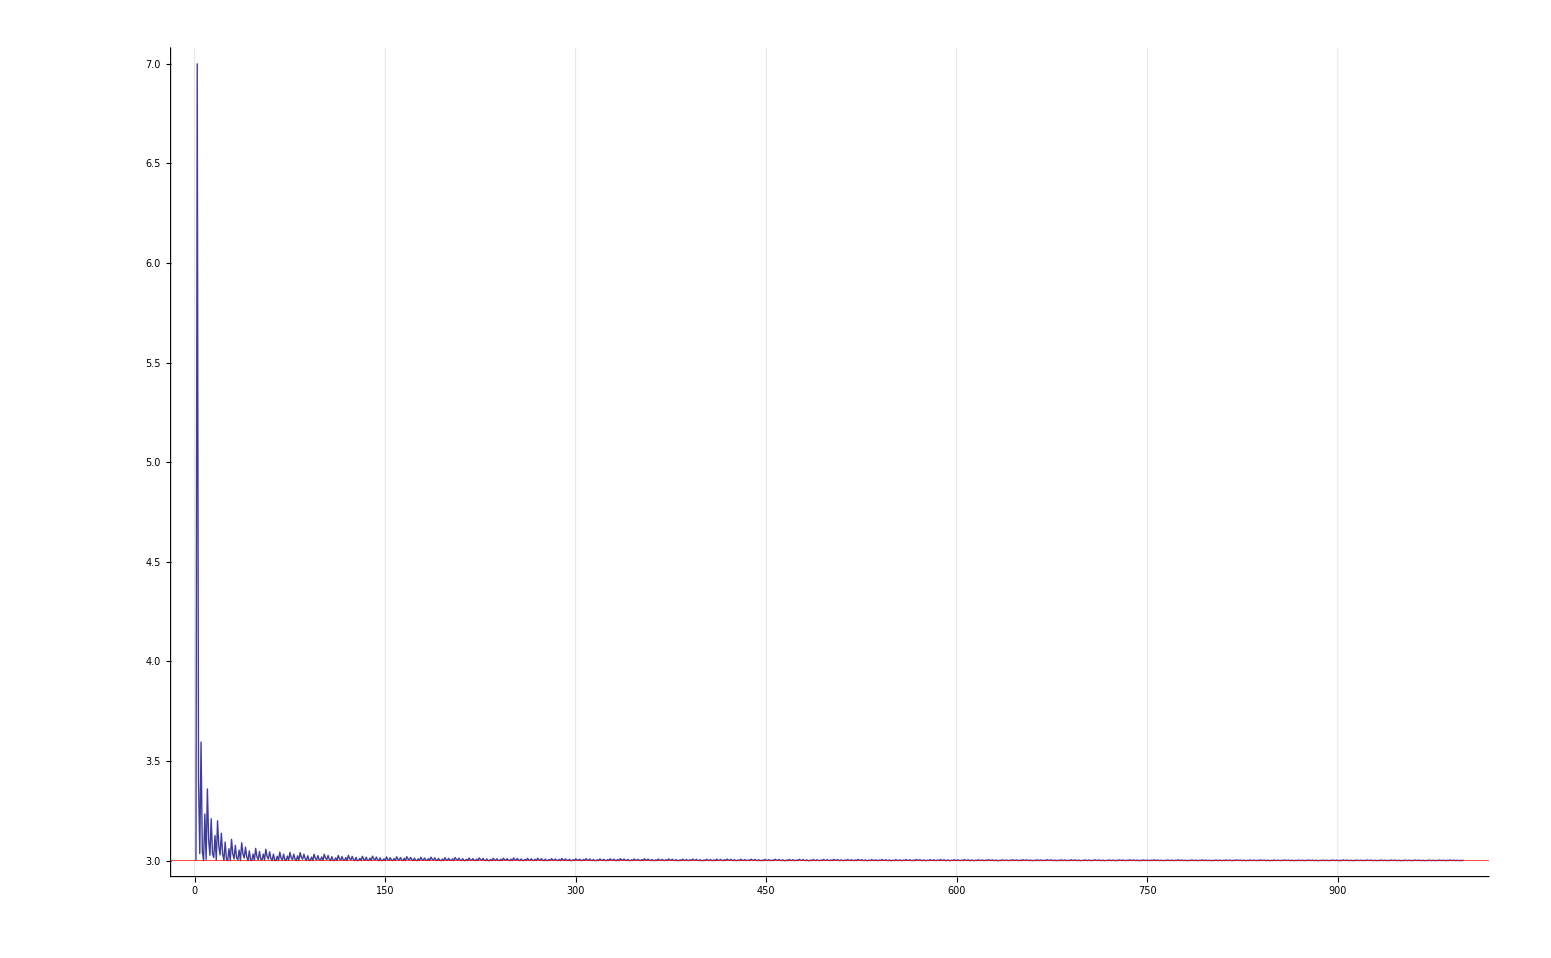

```mathematica
ListPlot[
Module[
{probes=Table[IntegerDigits[2^i,3],{i,0,1000}], eqs},
eqs=Map[Eq2,probes];
Monitor[
Flatten[
Table[
Select[
Flatten[
Map[Solutions,
N[Solve[eqs[[i]]==2^(i-1)]]
]
],
Im[#]==0&&#>0&],{i,1,Length[eqs]}]
],
{i}
]
],GridLines->{Automatic,{{3,Directive[Red,Thick]}}},PlotRange->Automatic,Joined->True]
```

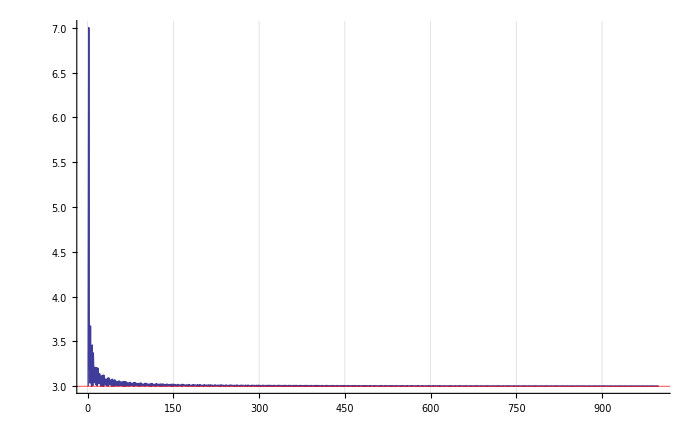

```mathematica
ListPlot[
Module[
{probes=Table[IntegerDigits[2^i,3],{i,0,1000}], eqs},
eqs=Map[Eq,probes];
Monitor[
Flatten[
Table[
Select[
Flatten[
Map[Solutions,
N[Solve[eqs[[i]]==2^(i-1)]]
]
],
Im[#]==0&&#>0&],{i,1,Length[eqs]}]
],
{i}
]
],GridLines->{Automatic,{{3,Directive[Red,Thick]}}},PlotRange->Automatic,Joined->True]
```

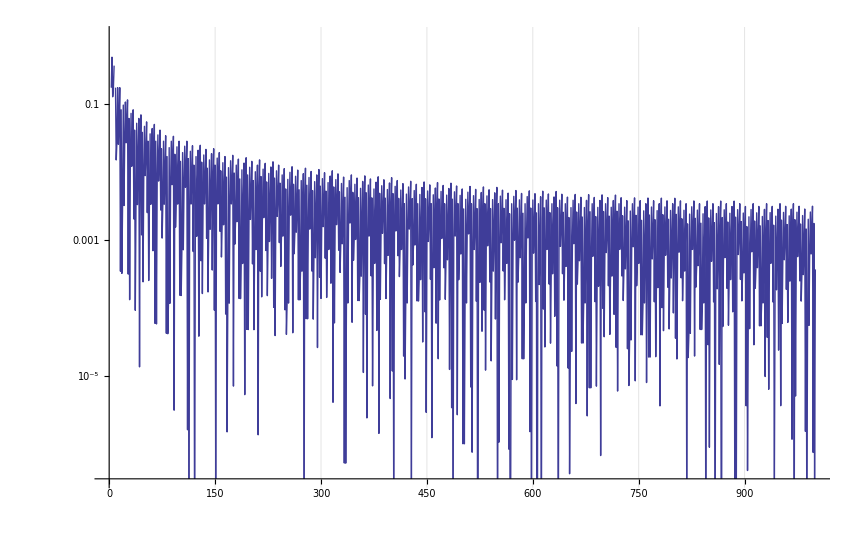

```mathematica
ListLogPlot[
Module[
{probes=Table[IntegerDigits[2^i+Distance[2^i,3],3],{i,0,1000}], eqs},
eqs=Map[Eq,probes];
Monitor[
3-Flatten[
Table[
Select[
Flatten[
Map[Solutions,
N[Solve[eqs[[i]]==2^(i-1)]]
]
],
Im[#]==0&&#>0&],{i,1,Length[eqs]}]
],
{i}
]
],GridLines->{Automatic,{{3,Directive[Red,Thick]}}},PlotRange->Automatic,Joined->True]
```

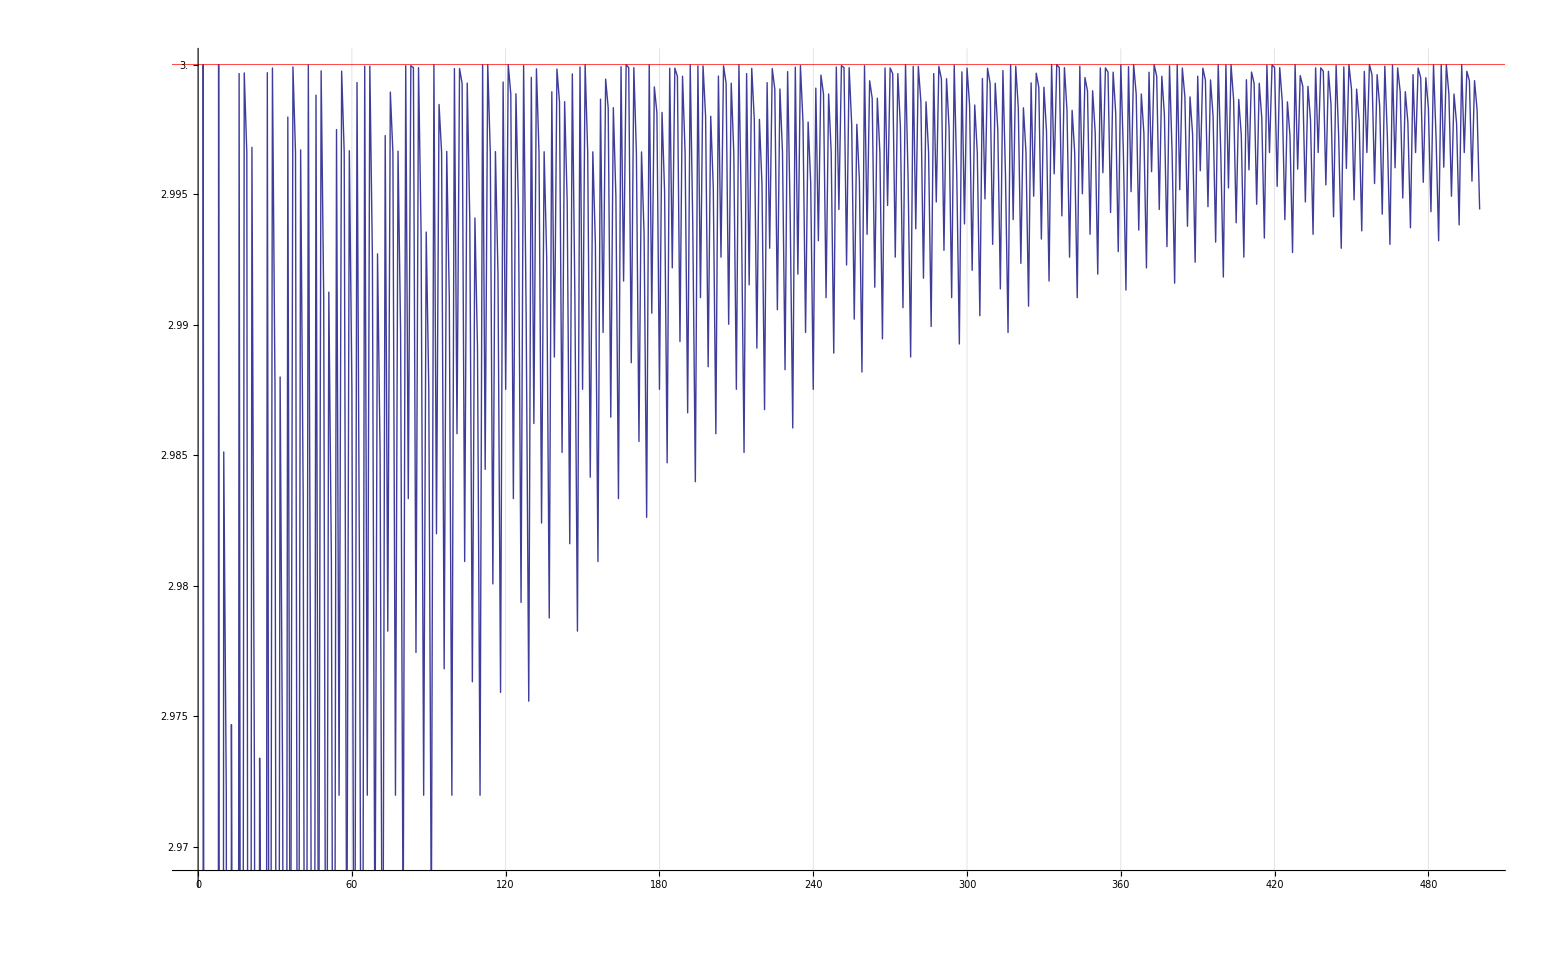

```mathematica
ListLogPlot[
Module[
{probes=Table[IntegerDigits[2^i+Distance[2^i,3],3],{i,0,500,1}], eqs},
eqs=Map[Eq,probes];
Monitor[
Flatten[
Table[
Select[
Flatten[
Map[Solutions,
N[Solve[eqs[[i]]==2^(i-1)]]
]
],
Im[#]==0&&#>0&],{i,1,Length[eqs]}]
],
{i}
]
],GridLines->{Automatic,{{3,Directive[Red,Thick]}}},PlotRange->Automatic,Joined->True]
```

```mathematica
sols=Framed[TableForm[Module[
{probes=Table[IntegerDigits[2^i+Distance[2^i,3],3],{i,0,80,1}], eqs},
eqs=Map[Eq,probes];
Monitor[
Table[
{i-1,Length[N[Solve[eqs[[i]]==2^(i-1)]]],Factor[eqs[[i]]==2^(i-1)]},{i,1,Length[eqs]}],
{i}
]
]]
]
```

0 | 1 | True
1 | 1 | x==2
2 | 1 | 1+x==4
3 | 2 | x^2==8
4 | 3 | x^3==16
5 | 3 | x^2 (1+x)==32
6 | 4 | x^4==64
7 | 5 | x^5==128
8 | 5 | (1+x) (1+x^2-x^3+x^4)==256
9 | 6 | x^6==512
10 | 6 | x^4 (1+x+x^2)==1024
11 | 7 | x^7==2048
12 | 8 | x^8==4096
13 | 8 | x^7 (1+x)==8192
14 | 9 | x^9==16384
15 | 10 | x^10==32768
16 | 10 | x^8 (1+x^2)==65536
17 | 11 | x^11==131072
18 | 11 | x^8 (1+x) (1+x^2)==262144
19 | 12 | x^12==524288
20 | 13 | x^13==1048576
21 | 13 | x^12 (1+x)==2097152
22 | 14 | x^14==4194304
23 | 15 | x^15==8388608
24 | 15 | x^14 (1+x)==16777216
25 | 16 | x^16==33554432
26 | 17 | x^17==67108864
27 | 17 | x^12 (1+x^2+x^5)==134217728
28 | 18 | x^18==268435456
29 | 18 | x^13 (1+x+x^2+x^4+x^5)==536870912
30 | 19 | x^19==1073741824
31 | 20 | x^20==2147483648
32 | 20 | x^19 (1+x)==4294967296
33 | 21 | x^21==8589934592
34 | 22 | x^22==17179869184
35 | 22 | x^20 (1+x^2)==34359738368
36 | 23 | x^23==68719476736
37 | 23 | x^18 (1+x+x^3+x^4+x^5)==137438953472
38 | 24 | x^24==274877906944
39 | 25 | x^25==549755813888
40 | 25 | x^24 (1+x)==1099511627776
41 | 26 | x^26==2199023255552
42 | 27 | x^27==4398046511104
43 | 27 | x^21 (1+x+x^3+x^4+x^6)==8796093022208
44 | 28 | x^28==17592186044416
45 | 29 | x^29==35184372088832
46 | 29 | x^26 (1+x) (1-x+x^2)==70368744177664
47 | 30 | x^30==140737488355328
48 | 30 | x^27 (1+x^2+x^3)==281474976710656
49 | 31 | x^31==562949953421312
50 | 32 | x^32==1125899906842624
51 | 32 | x^31 (1+x)==2251799813685248
52 | 33 | x^33==4503599627370496
53 | 34 | x^34==9007199254740992
54 | 34 | x^32 (1+x^2)==18014398509481984
55 | 35 | x^35==36028797018963968
56 | 35 | x^33 (1+x+x^2)==72057594037927936
57 | 36 | x^36==144115188075855872
58 | 37 | x^37==288230376151711744
59 | 37 | x^36 (1+x)==576460752303423488
60 | 38 | x^38==1152921504606846976
61 | 39 | x^39==2305843009213693952
62 | 39 | x^36 (1+x+x^3)==4611686018427387904
63 | 40 | x^40==9223372036854775808
64 | 41 | x^41==18446744073709551616
65 | 41 | x^37 (1+x^4)==36893488147419103232
66 | 42 | x^42==73786976294838206464
67 | 42 | x^37 (1+x) (1+x^4)==147573952589676412928
68 | 43 | x^43==295147905179352825856
69 | 44 | x^44==590295810358705651712
70 | 44 | x^43 (1+x)==1180591620717411303424
71 | 45 | x^45==2361183241434822606848
72 | 46 | x^46==4722366482869645213696
73 | 46 | x^44 (1+x^2)==9444732965739290427392
74 | 47 | x^47==18889465931478580854784
75 | 47 | x^45 (1+x+x^2)==37778931862957161709568
76 | 48 | x^48==75557863725914323419136
77 | 49 | x^49==151115727451828646838272
78 | 49 | x^48 (1+x)==302231454903657293676544
79 | 50 | x^50==604462909807314587353088
80 | 51 | x^51==1208925819614629174706176

```mathematica
Module[
{values, index,f},
With[
{min=1,max=2000},
values=Module[
{probes=Table[IntegerDigits[2^i+Distance[2^i,3],3],{i,min,max,1}], eqs},
eqs=Map[Eq,probes];
Monitor[
Table[
{i-1+min,RealSol[NSolve[eqs[[i]]==2^(i-1+min)]],Factor[eqs[[i]]==2^(i-1+min)][[1]]},{i,1,Length[eqs]}],
{i-1+min}
]
];
f=OpenWrite["c:\\temp\\roots.txt"];
For[index=1,index≤Length[values],index++,
Write[f,values[[index]]];
];
Close[f];
TableForm[
values, TableDepth->2]
]
]
```

1 | 2. | x
2 | 3. | 1+x
3 | 2.82843 | x^2
4 | 2.51984 | x^3
5 | 2.87404 | x^2 (1+x)
6 | 2.82843 | x^4
7 | 2.63902 | x^5
8 | 3. | (1+x) (1+x^2-x^3+x^4)
9 | 2.82843 | x^6
10 | 2.98511 | x^4 (1+x+x^2)
11 | 2.97199 | x^7
12 | 2.82843 | x^8
13 | 2.97469 | x^7 (1+x)
14 | 2.93947 | x^9
15 | 2.82843 | x^10
16 | 2.99965 | x^8 (1+x^2)
17 | 2.91896 | x^11
18 | 2.99968 | x^8 (1+x) (1+x^2)
19 | 2.99661 | x^12
20 | 2.90485 | x^13
21 | 2.99681 | x^12 (1+x)
22 | 2.97199 | x^14
23 | 2.89454 | x^15
24 | 2.97341 | x^14 (1+x)
25 | 2.95365 | x^16
26 | 2.88668 | x^17
27 | 2.99969 | x^12 (1+x^2+x^5)
28 | 2.93947 | x^18
29 | 2.99987 | x^13 (1+x+x^2+x^4+x^5)
30 | 2.98752 | x^19
31 | 2.92817 | x^20
32 | 2.98799 | x^19 (1+x)
33 | 2.97199 | x^21
34 | 2.91896 | x^22
35 | 2.99798 | x^20 (1+x^2)
36 | 2.95922 | x^23
37 | 2.99991 | x^18 (1+x+x^3+x^4+x^5)
38 | 2.99661 | x^24
39 | 2.94854 | x^25
40 | 2.99672 | x^24 (1+x)
41 | 2.98333 | x^26
42 | 2.93947 | x^27
43 | 2.99999 | x^21 (1+x+x^3+x^4+x^6)
44 | 2.97199 | x^28
45 | 2.93167 | x^29
46 | 2.99882 | x^26 (1+x) (1-x+x^2)
47 | 2.9622 | x^30
48 | 2.99976 | x^27 (1+x^2+x^3)
49 | 2.99104 | x^31
50 | 2.95365 | x^32
51 | 2.99125 | x^31 (1+x)
52 | 2.98092 | x^33
53 | 2.94613 | x^34
54 | 2.9975 | x^32 (1+x^2)
55 | 2.97199 | x^35
56 | 2.99975 | x^33 (1+x+x^2)
57 | 2.99661 | x^36
58 | 2.96405 | x^37
59 | 2.99668 | x^36 (1+x)
60 | 2.98752 | x^38
61 | 2.95694 | x^39
62 | 2.99931 | x^36 (1+x+x^3)
63 | 2.97935 | x^40
64 | 2.95053 | x^41
65 | 2.99994 | x^37 (1+x^4)
66 | 2.97199 | x^42
67 | 2.99994 | x^37 (1+x) (1+x^4)
68 | 2.99259 | x^43
69 | 2.96531 | x^44
70 | 2.99272 | x^43 (1+x)
71 | 2.9851 | x^45
72 | 2.95922 | x^46
73 | 2.99726 | x^44 (1+x^2)
74 | 2.97826 | x^47
75 | 2.99894 | x^45 (1+x+x^2)
76 | 2.99661 | x^48
77 | 2.97199 | x^49
78 | 2.99667 | x^48 (1+x)
79 | 2.9897 | x^50
80 | 2.96622 | x^51
81 | 2.99996 | x^47 (1-x+x^2) (1+x+x^2)
82 | 2.98333 | x^52
83 | 2.99996 | x^47 (1+x) (1-x+x^2) (1+x+x^2)
84 | 2.99988 | x^53
85 | 2.97744 | x^54
86 | 2.99988 | x^53 (1+x)
87 | 2.99347 | x^55
88 | 2.97199 | x^56
89 | 2.99356 | x^55 (1+x)
90 | 2.98752 | x^57
91 | 2.96692 | x^58
92 | 3. | x^50 (1+x+x^2+x^4+x^5+x^8)
93 | 2.98198 | x^59
94 | 2.99846 | x^57 (1+x+x^2)
95 | 2.99661 | x^60
96 | 2.97682 | x^61
97 | 2.99666 | x^60 (1+x)
98 | 2.99104 | x^62
99 | 2.97199 | x^63
100 | 2.99985 | x^61 (1+x^2)
101 | 2.98582 | x^64
102 | 2.99985 | x^61 (1+x) (1+x^2)
103 | 2.99928 | x^65
104 | 2.98092 | x^66
105 | 2.99929 | x^65 (1+x)
106 | 2.99403 | x^67
107 | 2.97632 | x^68
108 | 2.9941 | x^67 (1+x)
109 | 2.9891 | x^69
110 | 2.97199 | x^70
111 | 3. | x^62 (1+x^5+x^8)
112 | 2.98445 | x^71
113 | 3. | x^63 (1+x^4+x^5+x^7+x^8)
114 | 2.99661 | x^72
115 | 2.98006 | x^73
116 | 2.99665 | x^72 (1+x)
117 | 2.99194 | x^74
118 | 2.97592 | x^75
119 | 2.99933 | x^73 (1+x^2)
120 | 2.98752 | x^76
121 | 3. | x^64 (1+x+x^3+x^8+x^10+x^11+x^12)
122 | 2.99886 | x^77
123 | 2.98333 | x^78
124 | 2.99887 | x^77 (1+x)
125 | 2.99442 | x^79
126 | 2.97935 | x^80
127 | 2.99996 | x^75 (1+x) (1+x^2) (1-x+x^2)
128 | 2.99021 | x^81
129 | 2.97558 | x^82
130 | 2.99951 | x^79 (1+x) (1-x+x^2)
131 | 2.98621 | x^83
132 | 2.99984 | x^80 (1+x^2+x^3)
133 | 2.99661 | x^84
134 | 2.98239 | x^85
135 | 2.99664 | x^84 (1+x)
136 | 2.99259 | x^86
137 | 2.97876 | x^87
138 | 2.99895 | x^85 (1+x^2)
139 | 2.98876 | x^88
140 | 2.99983 | x^86 (1+x+x^2)
141 | 2.99856 | x^89
142 | 2.9851 | x^90
143 | 2.99857 | x^89 (1+x)
144 | 2.99471 | x^91
145 | 2.9816 | x^92
146 | 2.99964 | x^89 (1+x+x^3)
147 | 2.99104 | x^93
148 | 2.97826 | x^94
149 | 2.99991 | x^90 (1+x^4)
150 | 2.98752 | x^95
151 | 3. | x^85 (1+x+x^2+x^6+x^9+x^10)
152 | 2.99661 | x^96
153 | 2.98415 | x^97
154 | 2.99664 | x^96 (1+x)
155 | 2.99308 | x^98
156 | 2.98092 | x^99
157 | 2.99867 | x^97 (1+x^2)
158 | 2.9897 | x^100
159 | 2.99944 | x^98 (1+x+x^2)
160 | 2.99833 | x^101
161 | 2.98645 | x^102
162 | 2.99834 | x^101 (1+x)
163 | 2.99493 | x^103
164 | 2.98333 | x^104
165 | 2.99992 | x^100 (1-x+x^2) (1+x+x^2)
166 | 2.99167 | x^105
167 | 3. | x^101 (1+x+x^2+x^3+x^4)
168 | 2.99988 | x^106
169 | 2.98854 | x^107
170 | 2.99988 | x^106 (1+x)
171 | 2.99661 | x^108
172 | 2.98552 | x^109
173 | 2.99664 | x^108 (1+x)
174 | 2.99347 | x^110
175 | 2.98261 | x^111
176 | 2.99999 | x^107 (1+x+x^4)
177 | 2.99044 | x^112
178 | 2.99914 | x^110 (1+x+x^2)
179 | 2.99815 | x^113
180 | 2.98752 | x^114
181 | 2.99816 | x^113 (1+x)
182 | 2.99511 | x^115
183 | 2.9847 | x^116
184 | 2.99986 | x^114 (1+x^2)
185 | 2.99218 | x^117
186 | 2.99986 | x^114 (1+x) (1+x^2)
187 | 2.99955 | x^118
188 | 2.98935 | x^119
189 | 2.99955 | x^118 (1+x)
190 | 2.99661 | x^120
191 | 2.98662 | x^121
192 | 2.99999 | x^116 (1+x+x^2+x^3+x^5)
193 | 2.99378 | x^122
194 | 2.98398 | x^123
195 | 2.99995 | x^120 (1+x) (1-x+x^2)
196 | 2.99104 | x^124
197 | 2.99995 | x^120 (1+x)^2 (1-x+x^2)
198 | 2.998 | x^125
199 | 2.98838 | x^126
200 | 2.99801 | x^125 (1+x)
201 | 2.99525 | x^127
202 | 2.98582 | x^128
203 | 2.99956 | x^126 (1+x^2)
204 | 2.99259 | x^129
205 | 2.99995 | x^125 (1+x^2+x^3+x^4)
206 | 2.99928 | x^130
207 | 2.99001 | x^131
208 | 2.99928 | x^130 (1+x)
209 | 2.99661 | x^132
210 | 2.98752 | x^133
211 | 3. | x^125 (1+x+x^5+x^6+x^8)
212 | 2.99403 | x^134
213 | 2.9851 | x^135
214 | 2.99965 | x^132 (1+x) (1-x+x^2)
215 | 2.99153 | x^136
216 | 2.99985 | x^133 (1+x^2+x^3)
217 | 2.99788 | x^137
218 | 2.9891 | x^138
219 | 2.99789 | x^137 (1+x)
220 | 2.99537 | x^139
221 | 2.98674 | x^140
222 | 2.9993 | x^138 (1+x^2)
223 | 2.99293 | x^141
224 | 2.99985 | x^139 (1+x+x^2)
225 | 2.99905 | x^142
226 | 2.99057 | x^143
227 | 2.99906 | x^142 (1+x)
228 | 2.99661 | x^144
229 | 2.98827 | x^145
230 | 2.99973 | x^142 (1+x+x^3)
231 | 2.99424 | x^146
232 | 2.98604 | x^147
233 | 2.9999 | x^143 (1+x^4)
234 | 2.99194 | x^148
235 | 2.99996 | x^144 (1+x^3+x^4)
236 | 2.99778 | x^149
237 | 2.9897 | x^150
238 | 2.99779 | x^149 (1+x)
239 | 2.99547 | x^151
240 | 2.98752 | x^152
241 | 2.99909 | x^150 (1+x^2)
242 | 2.99322 | x^153
243 | 2.99959 | x^151 (1+x+x^2)
244 | 2.99886 | x^154
245 | 2.99104 | x^155
246 | 2.99887 | x^154 (1+x)
247 | 2.99661 | x^156
248 | 2.98891 | x^157
249 | 2.99991 | x^153 (1-x+x^2) (1+x+x^2)
250 | 2.99442 | x^158
251 | 2.99996 | x^154 (1+x+x^2+x^3+x^4)
252 | 2.99988 | x^159
253 | 2.99229 | x^160
254 | 2.99988 | x^159 (1+x)
255 | 2.99769 | x^161
256 | 2.99021 | x^162
257 | 2.9977 | x^161 (1+x)
258 | 2.99555 | x^163
259 | 2.98818 | x^164
260 | 2.99996 | x^160 (1+x+x^4)
261 | 2.99347 | x^165
262 | 2.99938 | x^163 (1+x+x^2)
263 | 2.9987 | x^166
264 | 2.99144 | x^167
265 | 2.99871 | x^166 (1+x)
266 | 2.99661 | x^168
267 | 2.98945 | x^169
268 | 2.99987 | x^167 (1+x^2)
269 | 2.99458 | x^170
270 | 2.99987 | x^167 (1+x) (1+x^2)
271 | 2.99965 | x^171
272 | 2.99259 | x^172
273 | 2.99965 | x^171 (1+x)
274 | 2.99761 | x^173
275 | 2.99065 | x^174
276 | 3. | x^164 (1+x+x^4+x^6+x^7+x^8+x^10)
277 | 2.99563 | x^175
278 | 2.98876 | x^176
279 | 2.99993 | x^173 (1+x) (1-x+x^2)
280 | 2.99368 | x^177
281 | 2.99993 | x^173 (1+x)^2 (1-x+x^2)
282 | 2.99856 | x^178
283 | 2.99178 | x^179
284 | 2.99857 | x^178 (1+x)
285 | 2.99661 | x^180
286 | 2.98993 | x^181
287 | 2.99965 | x^179 (1+x^2)
288 | 2.99471 | x^182
289 | 2.99993 | x^178 (1+x^2+x^3+x^4)
290 | 2.99945 | x^183
291 | 2.99285 | x^184
292 | 2.99946 | x^183 (1+x)
293 | 2.99755 | x^185
294 | 2.99104 | x^186
295 | 2.99997 | x^183 (1+x+x^3)
296 | 2.99569 | x^187
297 | 2.98926 | x^188
298 | 2.99972 | x^185 (1+x) (1-x+x^2)
299 | 2.99387 | x^189
300 | 2.99986 | x^186 (1+x^2+x^3)
301 | 2.99844 | x^190
302 | 2.99209 | x^191
303 | 2.99844 | x^190 (1+x)
304 | 2.99661 | x^192
305 | 2.99034 | x^193
306 | 2.99946 | x^191 (1+x^2)
307 | 2.99483 | x^194
308 | 2.99986 | x^192 (1+x+x^2)
309 | 2.99928 | x^195
310 | 2.99308 | x^196
311 | 2.99928 | x^195 (1+x)
312 | 2.99749 | x^197
313 | 2.99137 | x^198
314 | 2.99977 | x^195 (1+x+x^3)
315 | 2.99574 | x^199
316 | 2.9897 | x^200
317 | 3. | x^194 (1+x+x^6)
318 | 2.99403 | x^201
319 | 2.99994 | x^197 (1+x^3+x^4)
320 | 2.99833 | x^202
321 | 2.99235 | x^203
322 | 2.99833 | x^202 (1+x)
323 | 2.99661 | x^204
324 | 2.99071 | x^205
325 | 2.9993 | x^203 (1+x^2)
326 | 2.99493 | x^206
327 | 2.99967 | x^204 (1+x+x^2)
328 | 2.99912 | x^207
329 | 2.99329 | x^208
330 | 2.99913 | x^207 (1+x)
331 | 2.99744 | x^209
332 | 2.99167 | x^210
333 | 3. | x^203 (1+x) (1+x^2) (1-x+x^2-x^3+x^4)
334 | 2.99579 | x^211
335 | 3. | x^203 (1+x)^2 (1+x^2) (1-x+x^2-x^3+x^4)
336 | 2.99988 | x^212
337 | 2.99418 | x^213
338 | 2.99988 | x^212 (1+x)
339 | 2.99823 | x^214
340 | 2.99259 | x^215
341 | 2.99824 | x^214 (1+x)
342 | 2.99661 | x^216
343 | 2.99104 | x^217
344 | 2.99994 | x^213 (1+x+x^4)
345 | 2.99503 | x^218
346 | 2.9995 | x^216 (1+x+x^2)
347 | 2.99899 | x^219
348 | 2.99347 | x^220
349 | 2.99899 | x^219 (1+x)
350 | 2.9974 | x^221
351 | 2.99194 | x^222
352 | 2.99987 | x^220 (1+x^2)
353 | 2.99584 | x^223
354 | 2.99987 | x^220 (1+x) (1+x^2)
355 | 2.99971 | x^224
356 | 2.99431 | x^225
357 | 2.99971 | x^224 (1+x)
358 | 2.99815 | x^226
359 | 2.9928 | x^227
360 | 2.99999 | x^223 (1+x+x^2+x^4)
361 | 2.99661 | x^228
362 | 2.99133 | x^229
363 | 2.99992 | x^226 (1+x) (1-x+x^2)
364 | 2.99511 | x^230
365 | 3. | x^225 (1+x^2+x^4+x^5)
366 | 2.99886 | x^231
367 | 2.99363 | x^232
368 | 2.99887 | x^231 (1+x)
369 | 2.99736 | x^233
370 | 2.99218 | x^234
371 | 2.9997 | x^232 (1+x^2)
372 | 2.99588 | x^235
373 | 2.99999 | x^230 (1+x) (1-x+x^2+x^4)
374 | 2.99955 | x^236
375 | 2.99442 | x^237
376 | 2.99955 | x^236 (1+x)
377 | 2.99807 | x^238
378 | 2.993 | x^239
379 | 2.99995 | x^236 (1+x+x^3)
380 | 2.99661 | x^240
381 | 2.99159 | x^241
382 | 3. | x^234 (1+x) (1-x+2 x^2-x^3+x^4-x^5+x^6)
383 | 2.99518 | x^242
384 | 2.99987 | x^239 (1+x^2+x^3)
385 | 2.99875 | x^243
386 | 2.99378 | x^244
387 | 2.99876 | x^243 (1+x)
388 | 2.99732 | x^245
389 | 2.9924 | x^246
390 | 2.99955 | x^244 (1+x^2)
391 | 2.99591 | x^247
392 | 2.99986 | x^245 (1+x+x^2)
393 | 2.99941 | x^248
394 | 2.99453 | x^249
395 | 2.99941 | x^248 (1+x)
396 | 2.998 | x^250
397 | 2.99317 | x^251
398 | 3. | x^245 (1+x+x^2+x^4+x^6)
399 | 2.99661 | x^252
400 | 2.99183 | x^253
401 | 2.99999 | x^248 (1+x) (1-x+x^2-x^3+x^4)
402 | 2.99525 | x^254
403 | 3. | x^245 (1+x^4+x^8+x^9)
404 | 2.99865 | x^255
405 | 2.99391 | x^256
406 | 2.99866 | x^255 (1+x)
407 | 2.99729 | x^257
408 | 2.99259 | x^258
409 | 2.99942 | x^256 (1+x^2)
410 | 2.99595 | x^259
411 | 2.99971 | x^257 (1+x+x^2)
412 | 2.99928 | x^260
413 | 2.99463 | x^261
414 | 2.99928 | x^260 (1+x)
415 | 2.99794 | x^262
416 | 2.99333 | x^263
417 | 2.99998 | x^258 (1+x^3+x^5)
418 | 2.99661 | x^264
419 | 2.99999 | x^259 (1+x^2+x^3+x^4+x^5)
420 | 2.99988 | x^265
421 | 2.99531 | x^266
422 | 2.99988 | x^265 (1+x)
423 | 2.99856 | x^267
424 | 2.99403 | x^268
425 | 2.99856 | x^267 (1+x)
426 | 2.99726 | x^269
427 | 2.99277 | x^270
428 | 3. | x^261 (1+x^3+x^4+x^6+x^9)
429 | 2.99598 | x^271
430 | 2.99957 | x^269 (1+x+x^2)
431 | 2.99916 | x^272
432 | 2.99471 | x^273
433 | 2.99916 | x^272 (1+x)
434 | 2.99788 | x^274
435 | 2.99347 | x^275
436 | 2.99987 | x^273 (1+x^2)
437 | 2.99661 | x^276
438 | 2.99987 | x^273 (1+x) (1+x^2)
439 | 2.99974 | x^277
440 | 2.99537 | x^278
441 | 2.99974 | x^277 (1+x)
442 | 2.99848 | x^279
443 | 2.99414 | x^280
444 | 2.99997 | x^276 (1+x+x^2+x^4)
445 | 2.99723 | x^281
446 | 2.99293 | x^282
447 | 2.99991 | x^279 (1+x) (1-x+x^2)
448 | 2.996 | x^283
449 | 3. | x^277 (1+x) (1+x^2) (1-x+x^3)
450 | 2.99905 | x^284
451 | 2.99479 | x^285
452 | 2.99906 | x^284 (1+x)
453 | 2.99782 | x^286
454 | 2.9936 | x^287
455 | 2.99974 | x^285 (1+x^2)
456 | 2.99661 | x^288
457 | 3. | x^281 (1+x) (1+x^2) (1-x+x^4)
458 | 2.99961 | x^289
459 | 2.99542 | x^290
460 | 2.99961 | x^289 (1+x)
461 | 2.9984 | x^291
462 | 2.99424 | x^292
463 | 2.99994 | x^289 (1+x+x^3)
464 | 2.9972 | x^293
465 | 2.99308 | x^294
466 | 2.99998 | x^289 (1+x+x^2) (1-x^2+x^3)
467 | 2.99603 | x^295
468 | 2.99987 | x^292 (1+x^2+x^3)
469 | 2.99895 | x^296
470 | 2.99487 | x^297
471 | 2.99896 | x^296 (1+x)
472 | 2.99778 | x^298
473 | 2.99372 | x^299
474 | 2.99961 | x^297 (1+x^2)
475 | 2.99661 | x^300
476 | 2.99987 | x^298 (1+x+x^2)
477 | 2.99949 | x^301
478 | 2.99547 | x^302
479 | 2.99949 | x^301 (1+x)
480 | 2.99833 | x^303
481 | 2.99434 | x^304
482 | 2.99999 | x^299 (1+x+x^3+x^5)
483 | 2.99718 | x^305
484 | 2.99322 | x^306
485 | 3. | x^300 (1+x^2) (1-x^2+x^4)
486 | 2.99605 | x^307
487 | 3. | x^301 (1+x^5+x^6)
488 | 2.99886 | x^308
489 | 2.99493 | x^309
490 | 2.99887 | x^308 (1+x)
491 | 2.99773 | x^310
492 | 2.99383 | x^311
493 | 3. | x^305 (1+x+x^2+x^3+x^6)
494 | 2.99661 | x^312
495 | 2.99974 | x^310 (1+x+x^2)
496 | 2.99938 | x^313
497 | 2.99551 | x^314
498 | 2.99938 | x^313 (1+x)
499 | 2.99826 | x^315
500 | 2.99442 | x^316
501 | 3. | x^314 (1+x^2)
502 | 2.99716 | x^317
503 | 3. | x^314 (1+x) (1+x^2)
504 | 2.99988 | x^318
505 | 2.99607 | x^319
506 | 2.99988 | x^318 (1+x)
507 | 2.99878 | x^320
508 | 2.995 | x^321
509 | 2.99878 | x^320 (1+x)
510 | 2.99769 | x^322
511 | 2.99394 | x^323
512 | 2.99999 | x^318 (1+x^2+x^5)
513 | 2.99661 | x^324
514 | 3. | x^317 (1+x^2+x^3) (1+x^4)
515 | 2.99928 | x^325
516 | 2.99555 | x^326
517 | 2.99928 | x^325 (1+x)
518 | 2.9982 | x^327
519 | 2.9945 | x^328
520 | 2.99988 | x^326 (1+x^2)
521 | 2.99714 | x^329
522 | 3. | x^315 (1+x) (1+x^3+x^7-x^8+2 x^9-x^10+x^11+x^13)
523 | 2.99976 | x^330
524 | 2.99609 | x^331
525 | 2.99976 | x^330 (1+x)
526 | 2.9987 | x^332
527 | 2.99506 | x^333
528 | 2.99995 | x^329 (1+x+x^2+x^4)
529 | 2.99765 | x^334
530 | 2.99403 | x^335
531 | 2.99991 | x^332 (1+x) (1-x+x^2)
532 | 2.99661 | x^336
533 | 2.99999 | x^333 (1+x^2+x^3)
534 | 2.99918 | x^337
535 | 2.99559 | x^338
536 | 2.99919 | x^337 (1+x)
537 | 2.99815 | x^339
538 | 2.99458 | x^340
539 | 2.99976 | x^338 (1+x^2)
540 | 2.99712 | x^341
541 | 2.99998 | x^339 (1+x+x^2)
542 | 2.99965 | x^342
543 | 2.99611 | x^343
544 | 2.99965 | x^342 (1+x)
545 | 2.99863 | x^344
546 | 2.99511 | x^345
547 | 2.99993 | x^342 (1+x+x^3)
548 | 2.99761 | x^346
549 | 2.99412 | x^347
550 | 3. | x^337 (1+x+x^2+x^6+x^10)
551 | 2.99661 | x^348
552 | 3. | x^341 (1+x^2+x^3+x^6+x^7)
553 | 2.99909 | x^349
554 | 2.99563 | x^350
555 | 2.9991 | x^349 (1+x)
556 | 2.99809 | x^351
557 | 2.99465 | x^352
558 | 2.99965 | x^350 (1+x^2)
559 | 2.9971 | x^353
560 | 2.99987 | x^351 (1+x+x^2)
561 | 2.99955 | x^354
562 | 2.99613 | x^355
563 | 2.99955 | x^354 (1+x)
564 | 2.99856 | x^356
565 | 2.99516 | x^357
566 | 3. | x^350 (1+x^3+x^5+x^7)
567 | 2.99758 | x^358
568 | 3. | x^345 (1+x+x^6+x^8+x^9+x^10+x^11+x^12+x^13)
569 | 2.99999 | x^359
570 | 2.99661 | x^360
571 | 2.99999 | x^359 (1+x)
572 | 2.99901 | x^361
573 | 2.99566 | x^362
574 | 2.99901 | x^361 (1+x)
575 | 2.99805 | x^363
576 | 2.99471 | x^364
577 | 2.99999 | x^359 (1+x) (1+x^2-x^3+x^4)
578 | 2.99709 | x^365
579 | 2.99976 | x^363 (1+x+x^2)
580 | 2.99945 | x^366
581 | 2.99614 | x^367
582 | 2.99945 | x^366 (1+x)
583 | 2.9985 | x^368
584 | 2.99521 | x^369
585 | 2.99998 | x^367 (1+x^2)
586 | 2.99755 | x^370
587 | 2.99998 | x^367 (1+x) (1+x^2)
588 | 2.99988 | x^371
589 | 2.99661 | x^372
590 | 2.99988 | x^371 (1+x)
591 | 2.99894 | x^373
592 | 2.99569 | x^374
593 | 2.99894 | x^373 (1+x)
594 | 2.998 | x^375
595 | 2.99477 | x^376
596 | 3. | x^370 (1+x^3+x^6)
597 | 2.99707 | x^377
598 | 3. | x^368 (1+x+x^3+x^5+x^6+x^8+x^9)
599 | 2.99936 | x^378
600 | 2.99616 | x^379
601 | 2.99936 | x^378 (1+x)
602 | 2.99844 | x^380
603 | 2.99525 | x^381
604 | 2.99988 | x^379 (1+x^2)
605 | 2.99752 | x^382
606 | 3. | x^365 (1+x+x^2+x^4+x^6+x^7+x^9+x^11+x^13+x^15+x^16+x^17)
607 | 2.99978 | x^383
608 | 2.99661 | x^384
609 | 2.99978 | x^383 (1+x)
610 | 2.99886 | x^385
611 | 2.99572 | x^386
612 | 3. | x^375 (1+x^6+x^8+x^9+x^11)
613 | 2.99796 | x^387
614 | 2.99483 | x^388
615 | 2.9999 | x^385 (1+x) (1-x+x^2)
616 | 2.99706 | x^389
617 | 2.99997 | x^386 (1+x^2+x^3)
618 | 2.99928 | x^390
619 | 2.99617 | x^391
620 | 2.99928 | x^390 (1+x)
621 | 2.99838 | x^392
622 | 2.99529 | x^393
623 | 2.99978 | x^391 (1+x^2)
624 | 2.99749 | x^394
625 | 2.99997 | x^392 (1+x+x^2)
626 | 2.99968 | x^395
627 | 2.99661 | x^396
628 | 2.99968 | x^395 (1+x)
629 | 2.99879 | x^397
630 | 2.99574 | x^398
631 | 2.99992 | x^395 (1+x+x^3)
632 | 2.99792 | x^399
633 | 2.99488 | x^400
634 | 2.99999 | x^396 (1+x^4)
635 | 2.99705 | x^401
636 | 3. | x^391 (1-x+x^2) (1+2 x+2 x^2-x^4-x^5+x^6+2 x^7+x^8)
637 | 2.9992 | x^402
638 | 2.99618 | x^403
639 | 2.9992 | x^402 (1+x)
640 | 2.99833 | x^404
641 | 2.99533 | x^405
642 | 2.99968 | x^403 (1+x^2)
643 | 2.99747 | x^406
644 | 2.99987 | x^404 (1+x+x^2)
645 | 2.99959 | x^407
646 | 2.99661 | x^408
647 | 2.99959 | x^407 (1+x)
648 | 2.99873 | x^409
649 | 2.99577 | x^410
650 | 2.99999 | x^406 (1-x+x^2) (1+x+x^2)
651 | 2.99788 | x^411
652 | 3. | x^403 (1+x^2+x^4+x^5+x^6+x^7+x^8)
653 | 2.99998 | x^412
654 | 2.99703 | x^413
655 | 2.99998 | x^412 (1+x)
656 | 2.99912 | x^414
657 | 2.9962 | x^415
658 | 2.99913 | x^414 (1+x)
659 | 2.99828 | x^416
660 | 2.99537 | x^417
661 | 3. | x^411 (1+x^2+x^3+x^6)
662 | 2.99744 | x^418
663 | 2.99978 | x^416 (1+x+x^2)
664 | 2.99951 | x^419
665 | 2.99661 | x^420
666 | 2.99951 | x^419 (1+x)
667 | 2.99867 | x^421
668 | 2.99579 | x^422
669 | 2.99997 | x^420 (1+x^2)
670 | 2.99784 | x^423
671 | 2.99997 | x^420 (1+x) (1+x^2)
672 | 2.99988 | x^424
673 | 2.99702 | x^425
674 | 2.99988 | x^424 (1+x)
675 | 2.99905 | x^426
676 | 2.99621 | x^427
677 | 3. | x^421 (1+x^2) (1+x+x^4)
678 | 2.99823 | x^428
679 | 2.9954 | x^429
680 | 2.99999 | x^426 (1+x) (1-x+x^2)
681 | 2.99742 | x^430
682 | 2.99999 | x^426 (1+x)^2 (1-x+x^2)
683 | 2.99943 | x^431
684 | 2.99661 | x^432
685 | 2.99943 | x^431 (1+x)
686 | 2.99861 | x^433
687 | 2.99582 | x^434
688 | 2.99988 | x^432 (1+x^2)
689 | 2.99781 | x^435
690 | 2.99999 | x^431 (1+x^2+x^3+x^4)
691 | 2.99979 | x^436
692 | 2.99701 | x^437
693 | 2.99979 | x^436 (1+x)
694 | 2.99899 | x^438
695 | 2.99622 | x^439
696 | 3. | x^432 (1+x+x^4+x^5+x^7)
697 | 2.99819 | x^440
698 | 2.99544 | x^441
699 | 2.9999 | x^438 (1+x) (1-x+x^2)
700 | 2.9974 | x^442
701 | 2.99996 | x^439 (1+x^2+x^3)
702 | 2.99935 | x^443
703 | 2.99661 | x^444
704 | 2.99935 | x^443 (1+x)
705 | 2.99856 | x^445
706 | 2.99584 | x^446
707 | 2.99979 | x^444 (1+x^2)
708 | 2.99778 | x^447
709 | 2.99996 | x^445 (1+x+x^2)
710 | 2.99971 | x^448
711 | 2.997 | x^449
712 | 2.99971 | x^448 (1+x)
713 | 2.99892 | x^450
714 | 2.99623 | x^451
715 | 2.99992 | x^448 (1+x+x^3)
716 | 2.99815 | x^452
717 | 2.99547 | x^453
718 | 2.99997 | x^449 (1+x^4)
719 | 2.99738 | x^454
720 | 2.99999 | x^450 (1+x^3+x^4)
721 | 2.99928 | x^455
722 | 2.99661 | x^456
723 | 2.99928 | x^455 (1+x)
724 | 2.99851 | x^457
725 | 2.99586 | x^458
726 | 2.99971 | x^456 (1+x^2)
727 | 2.99775 | x^459
728 | 2.99987 | x^457 (1+x+x^2)
729 | 2.99963 | x^460
730 | 2.99699 | x^461
731 | 2.99963 | x^460 (1+x)
732 | 2.99886 | x^462
733 | 2.99624 | x^463
734 | 2.99997 | x^459 (1-x+x^2) (1+x+x^2)
735 | 2.99811 | x^464
736 | 2.99999 | x^460 (1+x+x^2+x^3+x^4)
737 | 2.99997 | x^465
738 | 2.99736 | x^466
739 | 2.99997 | x^465 (1+x)
740 | 2.99921 | x^467
741 | 2.99661 | x^468
742 | 2.99921 | x^467 (1+x)
743 | 2.99846 | x^469
744 | 2.99588 | x^470
745 | 2.99999 | x^466 (1+x+x^4)
746 | 2.99772 | x^471
747 | 2.99979 | x^469 (1+x+x^2)
748 | 2.99955 | x^472
749 | 2.99698 | x^473
750 | 2.99955 | x^472 (1+x)
751 | 2.99881 | x^474
752 | 2.99625 | x^475
753 | 2.99996 | x^473 (1+x^2)
754 | 2.99807 | x^476
755 | 2.99996 | x^473 (1+x) (1+x^2)
756 | 2.99988 | x^477
757 | 2.99734 | x^478
758 | 2.99988 | x^477 (1+x)
759 | 2.99914 | x^479
760 | 2.99661 | x^480
761 | 2.99999 | x^475 (1+x+x^2+x^3+x^5)
762 | 2.99841 | x^481
763 | 2.9959 | x^482
764 | 2.99998 | x^479 (1+x) (1-x+x^2)
765 | 2.99769 | x^483
766 | 2.99998 | x^479 (1+x)^2 (1-x+x^2)
767 | 2.99948 | x^484
768 | 2.99697 | x^485
769 | 2.99948 | x^484 (1+x)
770 | 2.99875 | x^486
771 | 2.99626 | x^487
772 | 2.99988 | x^485 (1+x^2)
773 | 2.99803 | x^488
774 | 2.99998 | x^484 (1+x^2+x^3+x^4)
775 | 2.9998 | x^489
776 | 2.99732 | x^490
777 | 2.9998 | x^489 (1+x)
778 | 2.99908 | x^491
779 | 2.99661 | x^492
780 | 3. | x^489 (1+x+x^3)
781 | 2.99837 | x^493
782 | 2.99591 | x^494
783 | 2.9999 | x^491 (1+x) (1-x+x^2)
784 | 2.99766 | x^495
785 | 2.99995 | x^492 (1+x^2+x^3)
786 | 2.99941 | x^496
787 | 2.99696 | x^497
788 | 2.99941 | x^496 (1+x)
789 | 2.9987 | x^498
790 | 2.99627 | x^499
791 | 2.9998 | x^497 (1+x^2)
792 | 2.998 | x^500
793 | 2.99995 | x^498 (1+x+x^2)
794 | 2.99973 | x^501
795 | 2.9973 | x^502
796 | 2.99973 | x^501 (1+x)
797 | 2.99902 | x^503
798 | 2.99661 | x^504
799 | 2.99992 | x^501 (1+x+x^3)
800 | 2.99833 | x^505
801 | 2.99593 | x^506
802 | 2.99996 | x^502 (1+x^4)
803 | 2.99764 | x^507
804 | 2.99998 | x^503 (1+x^3+x^4)
805 | 2.99934 | x^508
806 | 2.99695 | x^509
807 | 2.99934 | x^508 (1+x)
808 | 2.99865 | x^510
809 | 2.99628 | x^511
810 | 2.99972 | x^509 (1+x^2)
811 | 2.99797 | x^512
812 | 2.99987 | x^510 (1+x+x^2)
813 | 2.99965 | x^513
814 | 2.99729 | x^514
815 | 2.99965 | x^513 (1+x)
816 | 2.99897 | x^515
817 | 2.99661 | x^516
818 | 3. | x^507 (1+x+x^3+x^4+x^7+x^9)
819 | 2.99829 | x^517
820 | 2.99998 | x^513 (1+x+x^2+x^3+x^4)
821 | 2.99996 | x^518
822 | 2.99761 | x^519
823 | 2.99996 | x^518 (1+x)
824 | 2.99928 | x^520
825 | 2.99695 | x^521
826 | 2.99928 | x^520 (1+x)
827 | 2.9986 | x^522
828 | 2.99628 | x^523
829 | 2.99998 | x^519 (1+x+x^4)
830 | 2.99794 | x^524
831 | 2.9998 | x^522 (1+x+x^2)
832 | 2.99958 | x^525
833 | 2.99727 | x^526
834 | 2.99958 | x^525 (1+x)
835 | 2.99891 | x^527
836 | 2.99661 | x^528
837 | 2.99995 | x^526 (1+x^2)
838 | 2.99825 | x^529
839 | 2.99995 | x^526 (1+x) (1+x^2)
840 | 2.99988 | x^530
841 | 2.99759 | x^531
842 | 2.99988 | x^530 (1+x)
843 | 2.99922 | x^532
844 | 2.99694 | x^533
845 | 3. | x^524 (1+x+x^5+x^6+x^7+x^9)
846 | 2.99856 | x^534
847 | 2.99629 | x^535
848 | 2.99997 | x^532 (1+x) (1-x+x^2)
849 | 2.99791 | x^536
850 | 3. | x^530 (1+x+x^3+x^5+x^6)
851 | 2.99952 | x^537
852 | 2.99726 | x^538
853 | 2.99952 | x^537 (1+x)
854 | 2.99886 | x^539
855 | 2.99661 | x^540
856 | 2.99988 | x^538 (1+x^2)
857 | 2.99821 | x^541
858 | 3. | x^531 (1+x) (1+x^2+x^5-x^6+x^7+x^9)
859 | 2.99981 | x^542
860 | 2.99757 | x^543
861 | 2.99981 | x^542 (1+x)
862 | 2.99916 | x^544
863 | 2.99693 | x^545
864 | 2.99999 | x^542 (1+x+x^3)
865 | 2.99852 | x^546
866 | 2.9963 | x^547
867 | 3. | x^533 (1+x+x^2+x^3+x^8+x^9+x^10+x^14)
868 | 2.99788 | x^548
869 | 2.99995 | x^545 (1+x^2+x^3)
870 | 2.99945 | x^549
871 | 2.99724 | x^550
872 | 2.99945 | x^549 (1+x)
873 | 2.99881 | x^551
874 | 2.99661 | x^552
875 | 2.99981 | x^550 (1+x^2)
876 | 2.99818 | x^553
877 | 2.99994 | x^551 (1+x+x^2)
878 | 2.99974 | x^554
879 | 2.99755 | x^555
880 | 2.99974 | x^554 (1+x)
881 | 2.99911 | x^556
882 | 2.99692 | x^557
883 | 2.99991 | x^554 (1+x+x^3)
884 | 2.99848 | x^558
885 | 2.9963 | x^559
886 | 3. | x^550 (1+x^4+x^9)
887 | 2.99785 | x^560
888 | 3. | x^551 (1-x^2+x^4) (1+x^2+x^3+x^4+x^5)
889 | 2.99939 | x^561
890 | 2.99723 | x^562
891 | 2.99939 | x^561 (1+x)
892 | 2.99877 | x^563
893 | 2.99661 | x^564
894 | 2.99974 | x^562 (1+x^2)
895 | 2.99815 | x^565
896 | 2.99987 | x^563 (1+x+x^2)
897 | 2.99967 | x^566
898 | 2.99753 | x^567
899 | 2.99967 | x^566 (1+x)
900 | 2.99905 | x^568
901 | 2.99692 | x^569
902 | 3. | x^564 (1+x^3+x^5)
903 | 2.99844 | x^570
904 | 3. | x^563 (1+x^2) (1+x+x^2) (1-x+x^3)
905 | 2.99995 | x^571
906 | 2.99782 | x^572
907 | 2.99995 | x^571 (1+x)
908 | 2.99933 | x^573
909 | 2.99722 | x^574
910 | 2.99933 | x^573 (1+x)
911 | 2.99872 | x^575
912 | 2.99661 | x^576
913 | 2.99997 | x^572 (1+x+x^4)
914 | 2.99811 | x^577
915 | 2.99981 | x^575 (1+x+x^2)
916 | 2.99961 | x^578
917 | 2.99751 | x^579
918 | 2.99961 | x^578 (1+x)
919 | 2.999 | x^580
920 | 2.99691 | x^581
921 | 2.99995 | x^579 (1+x^2)
922 | 2.9984 | x^582
923 | 2.99995 | x^579 (1+x) (1+x^2)
924 | 2.99988 | x^583
925 | 2.9978 | x^584
926 | 2.99988 | x^583 (1+x)
927 | 2.99928 | x^585
928 | 2.9972 | x^586
929 | 2.99999 | x^582 (1+x+x^2+x^4)
930 | 2.99868 | x^587
931 | 2.99661 | x^588
932 | 2.99996 | x^585 (1+x) (1-x+x^2)
933 | 2.99808 | x^589
934 | 2.99999 | x^584 (1+x^2+x^4+x^5)
935 | 2.99955 | x^590
936 | 2.99749 | x^591
937 | 2.99955 | x^590 (1+x)
938 | 2.99895 | x^592
939 | 2.99691 | x^593
940 | 2.99988 | x^591 (1+x^2)
941 | 2.99836 | x^594
942 | 3. | x^587 (1+x+x^5+x^6+x^7)
943 | 2.99982 | x^595
944 | 2.99778 | x^596
945 | 2.99982 | x^595 (1+x)
946 | 2.99922 | x^597
947 | 2.99719 | x^598
948 | 2.99998 | x^595 (1+x+x^3)
949 | 2.99864 | x^599
950 | 2.99661 | x^600
951 | 3. | x^595 (1+x+x^2) (1-x^2+x^3)
952 | 2.99805 | x^601
953 | 2.99994 | x^598 (1+x^2+x^3)
954 | 2.99949 | x^602
955 | 2.99748 | x^603
956 | 2.99949 | x^602 (1+x)
957 | 2.99891 | x^604
958 | 2.9969 | x^605
959 | 2.99981 | x^603 (1+x^2)
960 | 2.99833 | x^606
961 | 2.99994 | x^604 (1+x+x^2)
962 | 2.99975 | x^607
963 | 2.99775 | x^608
964 | 2.99975 | x^607 (1+x)
965 | 2.99917 | x^609
966 | 2.99718 | x^610
967 | 3. | x^605 (1+x+x^3+x^5)
968 | 2.9986 | x^611
969 | 2.99661 | x^612
970 | 3. | x^602 (1+x^2) (1+x+x^4-x^6+x^8)
971 | 2.99803 | x^613
972 | 2.99999 | x^608 (1+x+x^2) (1-x+x^3)
973 | 2.99943 | x^614
974 | 2.99746 | x^615
975 | 2.99944 | x^614 (1+x)
976 | 2.99886 | x^616
977 | 2.99689 | x^617
978 | 2.99975 | x^615 (1+x^2)
979 | 2.9983 | x^618
980 | 2.99987 | x^616 (1+x+x^2)
981 | 2.99969 | x^619
982 | 2.99773 | x^620
983 | 2.99969 | x^619 (1+x)
984 | 2.99912 | x^621
985 | 2.99717 | x^622
986 | 3. | x^616 (1+x^4+x^6)
987 | 2.99856 | x^623
988 | 3. | x^617 (1+x^3+x^4+x^5+x^6)
989 | 2.99994 | x^624
990 | 2.998 | x^625
991 | 2.99994 | x^624 (1+x)
992 | 2.99938 | x^626
993 | 2.99744 | x^627
994 | 2.99938 | x^626 (1+x)
995 | 2.99882 | x^628
996 | 2.99689 | x^629
997 | 3. | x^622 (1+x^2+x^4+x^7)
998 | 2.99826 | x^630
999 | 3. | x^623 (1+x+x^2+x^3+x^4+x^6+x^7)
1000 | 2.99963 | x^631
1001 | 2.99771 | x^632
1002 | 2.99963 | x^631 (1+x)
1003 | 2.99908 | x^633
1004 | 2.99716 | x^634
1005 | 2.99994 | x^632 (1+x^2)
1006 | 2.99852 | x^635
1007 | 3. | x^627 (1+x+x^2+x^3+x^4+x^6+x^7+x^8)
1008 | 2.99988 | x^636
1009 | 2.99797 | x^637
1010 | 2.99988 | x^636 (1+x)
1011 | 2.99933 | x^638
1012 | 2.99743 | x^639
1013 | 2.99998 | x^635 (1+x+x^2+x^4)
1014 | 2.99878 | x^640
1015 | 2.99688 | x^641
1016 | 2.99996 | x^638 (1+x) (1-x+x^2)
1017 | 2.99823 | x^642
1018 | 3. | x^639 (1+x^2+x^3)
1019 | 2.99958 | x^643
1020 | 2.99769 | x^644
1021 | 2.99958 | x^643 (1+x)
1022 | 2.99903 | x^645
1023 | 2.99715 | x^646
1024 | 2.99988 | x^644 (1+x^2)
1025 | 2.99849 | x^647
1026 | 3. | x^645 (1+x+x^2)
1027 | 2.99982 | x^648
1028 | 2.99795 | x^649
1029 | 2.99982 | x^648 (1+x)
1030 | 2.99928 | x^650
1031 | 2.99741 | x^651
1032 | 2.99997 | x^648 (1+x+x^3)
1033 | 2.99874 | x^652
1034 | 2.99688 | x^653
1035 | 3. | x^647 (1+x^2+x^6)
1036 | 2.9982 | x^654
1037 | 3. | x^647 (1+x) (1+x^2+x^6)
1038 | 2.99952 | x^655
1039 | 2.99767 | x^656
1040 | 2.99952 | x^655 (1+x)
1041 | 2.99899 | x^657
1042 | 2.99714 | x^658
1043 | 2.99982 | x^656 (1+x^2)
1044 | 2.99845 | x^659
1045 | 2.99993 | x^657 (1+x+x^2)
1046 | 2.99976 | x^660
1047 | 2.99792 | x^661
1048 | 2.99976 | x^660 (1+x)
1049 | 2.99923 | x^662
1050 | 2.9974 | x^663
1051 | 3. | x^655 (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)
1052 | 2.9987 | x^664
1053 | 3. | x^654 (1+x^2) (1+x^3+x^4+x^7+x^8)
1054 | 3. | x^665
1055 | 2.99817 | x^666
1056 | 3. | x^665 (1+x)
1057 | 2.99947 | x^667
1058 | 2.99765 | x^668
1059 | 2.99947 | x^667 (1+x)
1060 | 2.99894 | x^669
1061 | 2.99713 | x^670
1062 | 3. | x^665 (1+x) (1+x^2-x^3+x^4)
1063 | 2.99842 | x^671
1064 | 2.99987 | x^669 (1+x+x^2)
1065 | 2.99971 | x^672
1066 | 2.9979 | x^673
1067 | 2.99971 | x^672 (1+x)
1068 | 2.99918 | x^674
1069 | 2.99738 | x^675
1070 | 2.99999 | x^673 (1+x^2)
1071 | 2.99866 | x^676
1072 | 2.99999 | x^673 (1+x) (1+x^2)
1073 | 2.99994 | x^677
1074 | 2.99815 | x^678
1075 | 2.99994 | x^677 (1+x)
1076 | 2.99942 | x^679
1077 | 2.99763 | x^680
1078 | 2.99942 | x^679 (1+x)
1079 | 2.9989 | x^681
1080 | 2.99712 | x^682
1081 | 2.99999 | x^677 (1+x^2+x^5)
1082 | 2.99839 | x^683
1083 | 3. | x^678 (1+x+x^2+x^4+x^5)
1084 | 2.99965 | x^684
1085 | 2.99788 | x^685
1086 | 2.99965 | x^684 (1+x)
1087 | 2.99914 | x^686
1088 | 2.99737 | x^687
1089 | 2.99994 | x^685 (1+x^2)
1090 | 2.99863 | x^688
1091 | 3. | x^683 (1+x+x^3+x^4+x^5)
1092 | 2.99988 | x^689
1093 | 2.99812 | x^690
1094 | 2.99988 | x^689 (1+x)
1095 | 2.99937 | x^691
1096 | 2.99761 | x^692
1097 | 3. | x^686 (1+x+x^3+x^4+x^6)
1098 | 2.99886 | x^693
1099 | 2.99711 | x^694
1100 | 2.99995 | x^691 (1+x) (1-x+x^2)
1101 | 2.99836 | x^695
1102 | 2.99999 | x^692 (1+x^2+x^3)
1103 | 2.9996 | x^696
1104 | 2.99786 | x^697
1105 | 2.9996 | x^696 (1+x)
1106 | 2.99909 | x^698
1107 | 2.99736 | x^699
1108 | 2.99988 | x^697 (1+x^2)
1109 | 2.99859 | x^700
1110 | 2.99999 | x^698 (1+x+x^2)
1111 | 2.99983 | x^701
1112 | 2.99809 | x^702
1113 | 2.99983 | x^701 (1+x)
1114 | 2.99932 | x^703
1115 | 2.9976 | x^704
1116 | 2.99996 | x^701 (1+x+x^3)
1117 | 2.99882 | x^705
1118 | 2.9971 | x^706
1119 | 3. | x^702 (1+x^4)
1120 | 2.99833 | x^707
1121 | 3. | x^702 (1+x) (1+x^4)
1122 | 2.99955 | x^708
1123 | 2.99784 | x^709
1124 | 2.99955 | x^708 (1+x)
1125 | 2.99905 | x^710
1126 | 2.99734 | x^711
1127 | 2.99982 | x^709 (1+x^2)
1128 | 2.99856 | x^712
1129 | 2.99993 | x^710 (1+x+x^2)
1130 | 2.99977 | x^713
1131 | 2.99807 | x^714
1132 | 2.99977 | x^713 (1+x)
1133 | 2.99928 | x^715
1134 | 2.99758 | x^716
1135 | 3. | x^712 (1-x+x^2) (1+x+x^2)
1136 | 2.99879 | x^717
1137 | 3. | x^712 (1+x) (1-x+x^2) (1+x+x^2)
1138 | 2.99999 | x^718
1139 | 2.9983 | x^719
1140 | 2.99999 | x^718 (1+x)
1141 | 2.9995 | x^720
1142 | 2.99781 | x^721
1143 | 2.9995 | x^720 (1+x)
1144 | 2.99901 | x^722
1145 | 2.99733 | x^723
1146 | 3. | x^714 (1+x) (1-x+x^2) (1+x^2+x^6)
1147 | 2.99853 | x^724
1148 | 2.99988 | x^722 (1+x+x^2)
1149 | 2.99972 | x^725
1150 | 2.99805 | x^726
1151 | 2.99972 | x^725 (1+x)
1152 | 2.99923 | x^727
1153 | 2.99757 | x^728
1154 | 2.99999 | x^726 (1+x^2)
1155 | 2.99875 | x^729
1156 | 2.99999 | x^726 (1+x) (1+x^2)
1157 | 2.99994 | x^730
1158 | 2.99827 | x^731
1159 | 2.99994 | x^730 (1+x)
1160 | 2.99945 | x^732
1161 | 2.9978 | x^733
1162 | 2.99945 | x^732 (1+x)
1163 | 2.99897 | x^734
1164 | 2.99732 | x^735
1165 | 3. | x^719 (1+x^2) (1+x^6+x^7-x^8-x^9+x^10+x^11-x^12+x^14)
1166 | 2.9985 | x^736
1167 | 3. | x^728 (1+x^4+x^5+x^7+x^8)
1168 | 2.99967 | x^737
1169 | 2.99802 | x^738
1170 | 2.99967 | x^737 (1+x)
1171 | 2.99919 | x^739
1172 | 2.99755 | x^740
1173 | 2.99993 | x^738 (1+x^2)
1174 | 2.99872 | x^741
1175 | 3. | x^737 (1+x^2+x^3+x^4)
1176 | 2.99988 | x^742
1177 | 2.99825 | x^743
1178 | 2.99988 | x^742 (1+x)
1179 | 2.99941 | x^744
1180 | 2.99778 | x^745
1181 | 3. | x^740 (1+x) (1+x^2) (1-x+x^2)
1182 | 2.99894 | x^746
1183 | 2.99731 | x^747
1184 | 2.99995 | x^744 (1+x) (1-x+x^2)
1185 | 2.99847 | x^748
1186 | 2.99998 | x^745 (1+x^2+x^3)
1187 | 2.99962 | x^749
1188 | 2.998 | x^750
1189 | 2.99962 | x^749 (1+x)
1190 | 2.99915 | x^751
1191 | 2.99753 | x^752
1192 | 2.99988 | x^750 (1+x^2)
1193 | 2.99868 | x^753
1194 | 2.99998 | x^751 (1+x+x^2)
1195 | 2.99983 | x^754
1196 | 2.99822 | x^755
1197 | 2.99983 | x^754 (1+x)
1198 | 2.99936 | x^756
1199 | 2.99776 | x^757
1200 | 2.99996 | x^754 (1+x+x^3)
1201 | 2.9989 | x^758
1202 | 2.9973 | x^759
1203 | 2.99999 | x^755 (1+x^4)
1204 | 2.99844 | x^760
1205 | 3. | x^748 (1+x+x^2+x^3+x^4) (1-x+x^4-x^6+x^8)
1206 | 2.99957 | x^761
1207 | 2.99798 | x^762
1208 | 2.99957 | x^761 (1+x)
1209 | 2.99911 | x^763
1210 | 2.99752 | x^764
1211 | 2.99983 | x^762 (1+x^2)
1212 | 2.99865 | x^765
1213 | 2.99993 | x^763 (1+x+x^2)
1214 | 2.99978 | x^766
1215 | 2.99819 | x^767
1216 | 2.99978 | x^766 (1+x)
1217 | 2.99932 | x^768
1218 | 2.99774 | x^769
1219 | 2.99999 | x^765 (1-x+x^2) (1+x+x^2)
1220 | 2.99886 | x^770
1221 | 3. | x^766 (1+x+x^2+x^3+x^4)
1222 | 2.99998 | x^771
1223 | 2.99841 | x^772
1224 | 2.99998 | x^771 (1+x)
1225 | 2.99953 | x^773
1226 | 2.99796 | x^774
1227 | 2.99953 | x^773 (1+x)
1228 | 2.99907 | x^775
1229 | 2.99751 | x^776
1230 | 3. | x^772 (1+x+x^4)
1231 | 2.99862 | x^777
1232 | 2.99988 | x^775 (1+x+x^2)
1233 | 2.99973 | x^778
1234 | 2.99817 | x^779
1235 | 2.99973 | x^778 (1+x)
1236 | 2.99928 | x^780
1237 | 2.99772 | x^781
1238 | 2.99998 | x^779 (1+x^2)
1239 | 2.99883 | x^782
1240 | 2.99998 | x^779 (1+x) (1+x^2)
1241 | 2.99993 | x^783
1242 | 2.99838 | x^784
1243 | 2.99993 | x^783 (1+x)
1244 | 2.99948 | x^785
1245 | 2.99794 | x^786
1246 | 3. | x^781 (1+x+x^2+x^3+x^5)
1247 | 2.99903 | x^787
1248 | 2.99749 | x^788
1249 | 2.99999 | x^785 (1+x) (1-x+x^2)
1250 | 2.99859 | x^789
1251 | 2.99999 | x^785 (1+x)^2 (1-x+x^2)
1252 | 2.99968 | x^790
1253 | 2.99815 | x^791
1254 | 2.99968 | x^790 (1+x)
1255 | 2.99924 | x^792
1256 | 2.99771 | x^793
1257 | 2.99993 | x^791 (1+x^2)
1258 | 2.99879 | x^794
1259 | 2.99999 | x^790 (1+x^2+x^3+x^4)
1260 | 2.99988 | x^795
1261 | 2.99835 | x^796
1262 | 2.99988 | x^795 (1+x)
1263 | 2.99944 | x^797
1264 | 2.99792 | x^798
1265 | 3. | x^789 (1+x^2+x^6+x^7+x^9)
1266 | 2.999 | x^799
1267 | 2.99748 | x^800
1268 | 2.99994 | x^797 (1+x) (1-x+x^2)
1269 | 2.99856 | x^801
1270 | 2.99998 | x^798 (1+x^2+x^3)
1271 | 2.99964 | x^802
1272 | 2.99812 | x^803
1273 | 2.99964 | x^802 (1+x)
1274 | 2.9992 | x^804
1275 | 2.99769 | x^805
1276 | 2.99988 | x^803 (1+x^2)
1277 | 2.99876 | x^806
1278 | 2.99997 | x^804 (1+x+x^2)
1279 | 2.99983 | x^807
1280 | 2.99833 | x^808
1281 | 2.99983 | x^807 (1+x)
1282 | 2.9994 | x^809
1283 | 2.9979 | x^810
1284 | 2.99995 | x^807 (1+x+x^3)
1285 | 2.99896 | x^811
1286 | 2.99747 | x^812
1287 | 2.99998 | x^808 (1+x^4)
1288 | 2.99853 | x^813
1289 | 2.99999 | x^809 (1+x^3+x^4)
1290 | 2.99959 | x^814
1291 | 2.9981 | x^815
1292 | 2.99959 | x^814 (1+x)
1293 | 2.99916 | x^816
1294 | 2.99767 | x^817
1295 | 2.99983 | x^815 (1+x^2)
1296 | 2.99873 | x^818
1297 | 2.99992 | x^816 (1+x+x^2)
1298 | 2.99979 | x^819
1299 | 2.9983 | x^820
1300 | 2.99979 | x^819 (1+x)
1301 | 2.99936 | x^821
1302 | 2.99788 | x^822
1303 | 2.99998 | x^818 (1-x+x^2) (1+x+x^2)
1304 | 2.99893 | x^823
1305 | 2.99999 | x^819 (1+x+x^2+x^3+x^4)
1306 | 2.99998 | x^824
1307 | 2.9985 | x^825
1308 | 2.99998 | x^824 (1+x)
1309 | 2.99955 | x^826
1310 | 2.99808 | x^827
1311 | 2.99955 | x^826 (1+x)
1312 | 2.99912 | x^828
1313 | 2.99766 | x^829
1314 | 2.99999 | x^825 (1+x+x^4)
1315 | 2.9987 | x^830
1316 | 2.99988 | x^828 (1+x+x^2)
1317 | 2.99974 | x^831
1318 | 2.99828 | x^832
1319 | 2.99974 | x^831 (1+x)
1320 | 2.99932 | x^833
1321 | 2.99786 | x^834
1322 | 2.99997 | x^832 (1+x^2)
1323 | 2.9989 | x^835
1324 | 2.99997 | x^832 (1+x) (1+x^2)
1325 | 2.99993 | x^836
1326 | 2.99848 | x^837
1327 | 2.99993 | x^836 (1+x)
1328 | 2.99951 | x^838
1329 | 2.99806 | x^839
1330 | 3. | x^829 (1+x^4+x^6+x^7+x^8+x^10)
1331 | 2.99909 | x^840
1332 | 2.99764 | x^841
1333 | 2.99999 | x^838 (1+x) (1-x+x^2)
1334 | 2.99867 | x^842
1335 | 2.99999 | x^838 (1+x)^2 (1-x+x^2)
1336 | 2.9997 | x^843
1337 | 2.99826 | x^844
1338 | 2.9997 | x^843 (1+x)
1339 | 2.99928 | x^845
1340 | 2.99784 | x^846
1341 | 2.99993 | x^844 (1+x^2)
1342 | 2.99886 | x^847
1343 | 2.99999 | x^843 (1+x^2+x^3+x^4)
1344 | 2.99988 | x^848
1345 | 2.99845 | x^849
1346 | 2.99988 | x^848 (1+x)
1347 | 2.99947 | x^850
1348 | 2.99804 | x^851
1349 | 2.99999 | x^848 (1+x+x^3)
1350 | 2.99905 | x^852
1351 | 2.99763 | x^853
1352 | 2.99994 | x^850 (1+x) (1-x+x^2)
1353 | 2.99864 | x^854
1354 | 2.99997 | x^851 (1+x^2+x^3)
1355 | 2.99965 | x^855
1356 | 2.99823 | x^856
1357 | 2.99965 | x^855 (1+x)
1358 | 2.99924 | x^857
1359 | 2.99782 | x^858
1360 | 2.99988 | x^856 (1+x^2)
1361 | 2.99883 | x^859
1362 | 2.99997 | x^857 (1+x+x^2)
1363 | 2.99984 | x^860
1364 | 2.99842 | x^861
1365 | 2.99984 | x^860 (1+x)
1366 | 2.99943 | x^862
1367 | 2.99802 | x^863
1368 | 2.99995 | x^860 (1+x+x^3)
1369 | 2.99902 | x^864
1370 | 2.99761 | x^865
1371 | 3. | x^859 (1+x+x^6)
1372 | 2.99861 | x^866
1373 | 2.99999 | x^862 (1+x^3+x^4)
1374 | 2.99961 | x^867
1375 | 2.99821 | x^868
1376 | 2.99961 | x^867 (1+x)
1377 | 2.9992 | x^869
1378 | 2.99781 | x^870
1379 | 2.99983 | x^868 (1+x^2)
1380 | 2.9988 | x^871
1381 | 2.99992 | x^869 (1+x+x^2)
1382 | 2.99979 | x^872
1383 | 2.9984 | x^873
1384 | 2.99979 | x^872 (1+x)
1385 | 2.99939 | x^874
1386 | 2.998 | x^875
1387 | 3. | x^868 (1+x) (1+x^2) (1-x+x^2-x^3+x^4)
1388 | 2.99899 | x^876
1389 | 3. | x^867 (1+x^2+x^3+x^4+x^6+x^7+x^8+x^9)
1390 | 2.99997 | x^877
1391 | 2.99859 | x^878
1392 | 2.99997 | x^877 (1+x)
1393 | 2.99957 | x^879
1394 | 2.99819 | x^880
1395 | 2.99957 | x^879 (1+x)
1396 | 2.99917 | x^881
1397 | 2.99779 | x^882
1398 | 2.99998 | x^878 (1+x+x^4)
1399 | 2.99877 | x^883
1400 | 2.99988 | x^881 (1+x+x^2)
1401 | 2.99975 | x^884
1402 | 2.99837 | x^885
1403 | 2.99975 | x^884 (1+x)
1404 | 2.99935 | x^886
1405 | 2.99798 | x^887
1406 | 2.99997 | x^885 (1+x^2)
1407 | 2.99895 | x^888
1408 | 2.99997 | x^885 (1+x) (1+x^2)
1409 | 2.99993 | x^889
1410 | 2.99856 | x^890
1411 | 2.99993 | x^889 (1+x)
1412 | 2.99953 | x^891
1413 | 2.99817 | x^892
1414 | 3. | x^888 (1+x+x^2+x^4)
1415 | 2.99914 | x^893
1416 | 2.99778 | x^894
1417 | 2.99998 | x^891 (1+x) (1-x+x^2)
1418 | 2.99874 | x^895
1419 | 3. | x^890 (1+x^2+x^4+x^5)
1420 | 2.99971 | x^896
1421 | 2.99835 | x^897
1422 | 2.99971 | x^896 (1+x)
1423 | 2.99931 | x^898
1424 | 2.99796 | x^899
1425 | 2.99992 | x^897 (1+x^2)
1426 | 2.99892 | x^900
1427 | 3. | x^895 (1+x) (1-x+x^2+x^4)
1428 | 2.99988 | x^901
1429 | 2.99853 | x^902
1430 | 2.99988 | x^901 (1+x)
1431 | 2.99949 | x^903
1432 | 2.99815 | x^904
1433 | 2.99999 | x^901 (1+x+x^3)
1434 | 2.9991 | x^905
1435 | 2.99776 | x^906
1436 | 3. | x^899 (1+x) (1-x+2 x^2-x^3+x^4-x^5+x^6)
1437 | 2.99871 | x^907
1438 | 2.99996 | x^904 (1+x^2+x^3)
1439 | 2.99967 | x^908
1440 | 2.99833 | x^909
1441 | 2.99967 | x^908 (1+x)
1442 | 2.99928 | x^910
1443 | 2.99794 | x^911
1444 | 2.99988 | x^909 (1+x^2)
1445 | 2.99889 | x^912
1446 | 2.99996 | x^910 (1+x+x^2)
1447 | 2.99984 | x^913
1448 | 2.99851 | x^914
1449 | 2.99984 | x^913 (1+x)
1450 | 2.99945 | x^915
1451 | 2.99813 | x^916
1452 | 3. | x^910 (1+x+x^2+x^4+x^6)
1453 | 2.99907 | x^917
1454 | 2.99775 | x^918
1455 | 3. | x^913 (1+x) (1-x+x^2-x^3+x^4)
1456 | 2.99869 | x^919
1457 | 3. | x^914 (1+x+x^2) (1-x+x^3)
1458 | 2.99963 | x^920
1459 | 2.99831 | x^921
1460 | 2.99963 | x^920 (1+x)
1461 | 2.99924 | x^922
1462 | 2.99793 | x^923
1463 | 2.99984 | x^921 (1+x^2)
1464 | 2.99886 | x^924
1465 | 2.99992 | x^922 (1+x+x^2)
1466 | 2.9998 | x^925
1467 | 2.99848 | x^926
1468 | 2.9998 | x^925 (1+x)
1469 | 2.99942 | x^927
1470 | 2.99811 | x^928
1471 | 2.99999 | x^923 (1+x^3+x^5)
1472 | 2.99904 | x^929
1473 | 3. | x^924 (1+x^2+x^3+x^4+x^5)
1474 | 2.99997 | x^930
1475 | 2.99866 | x^931
1476 | 2.99997 | x^930 (1+x)
1477 | 2.99959 | x^932
1478 | 2.99828 | x^933
1479 | 2.99959 | x^932 (1+x)
1480 | 2.99921 | x^934
1481 | 2.99791 | x^935
1482 | 3. | x^929 (1+x) (1+x^2) (1-x^2+x^3)
1483 | 2.99883 | x^936
1484 | 2.99988 | x^934 (1+x+x^2)
1485 | 2.99976 | x^937
1486 | 2.99846 | x^938
1487 | 2.99976 | x^937 (1+x)
1488 | 2.99938 | x^939
1489 | 2.99809 | x^940
1490 | 2.99996 | x^938 (1+x^2)
1491 | 2.99901 | x^941
1492 | 2.99996 | x^938 (1+x) (1+x^2)
1493 | 2.99992 | x^942
1494 | 2.99863 | x^943
1495 | 2.99992 | x^942 (1+x)
1496 | 2.99955 | x^944
1497 | 2.99826 | x^945
1498 | 2.99999 | x^941 (1+x+x^2+x^4)
1499 | 2.99918 | x^946
1500 | 2.99789 | x^947
1501 | 2.99997 | x^944 (1+x) (1-x+x^2)
1502 | 2.99881 | x^948
1503 | 3. | x^942 (1+x) (1+x^2) (1-x+x^3)
1504 | 2.99972 | x^949
1505 | 2.99844 | x^950
1506 | 2.99972 | x^949 (1+x)
1507 | 2.99935 | x^951
1508 | 2.99807 | x^952
1509 | 2.99992 | x^950 (1+x^2)
1510 | 2.99898 | x^953
1511 | 3. | x^940 (1+x+x^3+x^4+x^5+x^11+x^12+x^13)
1512 | 2.99988 | x^954
1513 | 2.99861 | x^955
1514 | 2.99988 | x^954 (1+x)
1515 | 2.99951 | x^956
1516 | 2.99824 | x^957
1517 | 2.99998 | x^954 (1+x+x^3)
1518 | 2.99914 | x^958
1519 | 2.99788 | x^959
1520 | 2.99999 | x^954 (1+x+x^2) (1-x^2+x^3)
1521 | 2.99878 | x^960
1522 | 2.99996 | x^957 (1+x^2+x^3)
1523 | 2.99968 | x^961
1524 | 2.99841 | x^962
1525 | 2.99968 | x^961 (1+x)
1526 | 2.99931 | x^963
1527 | 2.99805 | x^964
1528 | 2.99988 | x^962 (1+x^2)
1529 | 2.99895 | x^965
1530 | 2.99996 | x^963 (1+x+x^2)
1531 | 2.99984 | x^966
1532 | 2.99858 | x^967
1533 | 2.99984 | x^966 (1+x)
1534 | 2.99948 | x^968
1535 | 2.99822 | x^969
1536 | 3. | x^964 (1+x+x^3+x^5)
1537 | 2.99911 | x^970
1538 | 2.99786 | x^971
1539 | 3. | x^965 (1+x^2) (1-x^2+x^4)
1540 | 2.99875 | x^972
1541 | 3. | x^966 (1+x^5+x^6)
1542 | 2.99964 | x^973
1543 | 2.99839 | x^974
1544 | 2.99964 | x^973 (1+x)
1545 | 2.99928 | x^975
1546 | 2.99803 | x^976
1547 | 3. | x^970 (1+x+x^2+x^3+x^6)
1548 | 2.99892 | x^977
1549 | 2.99992 | x^975 (1+x+x^2)
1550 | 2.9998 | x^978
1551 | 2.99856 | x^979
1552 | 2.9998 | x^978 (1+x)
1553 | 2.99944 | x^980
1554 | 2.9982 | x^981
1555 | 3. | x^979 (1+x^2)
1556 | 2.99908 | x^982
1557 | 3. | x^979 (1+x) (1+x^2)
1558 | 2.99996 | x^983
1559 | 2.99873 | x^984
1560 | 2.99996 | x^983 (1+x)
1561 | 2.9996 | x^985
1562 | 2.99837 | x^986
1563 | 2.9996 | x^985 (1+x)
1564 | 2.99925 | x^987
1565 | 2.99802 | x^988
1566 | 3. | x^983 (1+x^2+x^5)
1567 | 2.99889 | x^989
1568 | 3. | x^982 (1+x^2+x^3) (1+x^4)
1569 | 2.99976 | x^990
1570 | 2.99854 | x^991
1571 | 2.99976 | x^990 (1+x)
1572 | 2.99941 | x^992
1573 | 2.99818 | x^993
1574 | 2.99996 | x^991 (1+x^2)
1575 | 2.99905 | x^994
1576 | 3. | x^987 (1+x) (1-x+2 x^2-x^3+x^4+x^6)
1577 | 2.99992 | x^995
1578 | 2.9987 | x^996
1579 | 2.99992 | x^995 (1+x)
1580 | 2.99957 | x^997
1581 | 2.99835 | x^998
1582 | 2.99998 | x^994 (1+x+x^2+x^4)
1583 | 2.99921 | x^999
1584 | 2.998 | x^1000
1585 | 2.99997 | x^997 (1+x) (1-x+x^2)
1586 | 2.99886 | x^1001
1587 | 3. | x^998 (1+x^2+x^3)
1588 | 2.99973 | x^1002
1589 | 2.99851 | x^1003
1590 | 2.99973 | x^1002 (1+x)
1591 | 2.99937 | x^1004
1592 | 2.99816 | x^1005
1593 | 2.99992 | x^1003 (1+x^2)
1594 | 2.99902 | x^1006
1595 | 2.99999 | x^1004 (1+x+x^2)
1596 | 2.99988 | x^1007
1597 | 2.99868 | x^1008
1598 | 2.99988 | x^1007 (1+x)
1599 | 2.99953 | x^1009
1600 | 2.99833 | x^1010
1601 | 2.99998 | x^1007 (1+x+x^3)
1602 | 2.99918 | x^1011
1603 | 2.99798 | x^1012
1604 | 3. | x^1001 (1+x+x^3+x^7+x^11)
1605 | 2.99884 | x^1013
1606 | 3. | x^1006 (1+x^2+x^3+x^6+x^7)
1607 | 2.99969 | x^1014
1608 | 2.99849 | x^1015
1609 | 2.99969 | x^1014 (1+x)
1610 | 2.99934 | x^1016
1611 | 2.99815 | x^1017
1612 | 2.99988 | x^1015 (1+x^2)
1613 | 2.999 | x^1018
1614 | 2.99995 | x^1016 (1+x+x^2)
1615 | 2.99984 | x^1019
1616 | 2.99865 | x^1020
1617 | 2.99984 | x^1019 (1+x)
1618 | 2.9995 | x^1021
1619 | 2.99831 | x^1022
1620 | 3. | x^1015 (1+x^3+x^5+x^7)
1621 | 2.99915 | x^1023
1622 | 3. | x^1016 (1+x^2+x^3+x^4+x^5+x^6+x^7)
1623 | 3. | x^1024
1624 | 2.99881 | x^1025
1625 | 3. | x^1024 (1+x)
1626 | 2.99965 | x^1026
1627 | 2.99847 | x^1027
1628 | 2.99965 | x^1026 (1+x)
1629 | 2.99931 | x^1028
1630 | 2.99813 | x^1029
1631 | 3. | x^1024 (1+x) (1+x^2-x^3+x^4)
1632 | 2.99897 | x^1030
1633 | 2.99992 | x^1028 (1+x+x^2)
1634 | 2.99981 | x^1031
1635 | 2.99863 | x^1032
1636 | 2.99981 | x^1031 (1+x)
1637 | 2.99946 | x^1033
1638 | 2.99829 | x^1034
1639 | 2.99999 | x^1032 (1+x^2)
1640 | 2.99912 | x^1035
1641 | 2.99999 | x^1032 (1+x) (1+x^2)
1642 | 2.99996 | x^1036
1643 | 2.99878 | x^1037
1644 | 2.99996 | x^1036 (1+x)
1645 | 2.99962 | x^1038
1646 | 2.99845 | x^1039
1647 | 2.99962 | x^1038 (1+x)
1648 | 2.99928 | x^1040
1649 | 2.99811 | x^1041
1650 | 3. | x^1035 (1+x^3+x^6)
1651 | 2.99894 | x^1042
1652 | 3. | x^1034 (1+x^2+x^4+x^5+x^7+x^8)
1653 | 2.99977 | x^1043
1654 | 2.9986 | x^1044
1655 | 2.99977 | x^1043 (1+x)
1656 | 2.99943 | x^1045
1657 | 2.99827 | x^1046
1658 | 2.99995 | x^1044 (1+x^2)
1659 | 2.99909 | x^1047
1660 | 3. | x^1039 (1+x+x^2) (1-x+x^2+x^6)
1661 | 2.99992 | x^1048
1662 | 2.99876 | x^1049
1663 | 2.99992 | x^1048 (1+x)
1664 | 2.99958 | x^1050
1665 | 2.99843 | x^1051
1666 | 3. | x^1046 (1+x) (1+x^2) (1-x+x^2)
1667 | 2.99925 | x^1052
1668 | 2.99809 | x^1053
1669 | 2.99996 | x^1050 (1+x) (1-x+x^2)
1670 | 2.99891 | x^1054
1671 | 2.99999 | x^1051 (1+x^2+x^3)
1672 | 2.99973 | x^1055
1673 | 2.99858 | x^1056
1674 | 2.99973 | x^1055 (1+x)
1675 | 2.9994 | x^1057
1676 | 2.99825 | x^1058
1677 | 2.99992 | x^1056 (1+x^2)
1678 | 2.99907 | x^1059
1679 | 2.99999 | x^1057 (1+x+x^2)
1680 | 2.99988 | x^1060
1681 | 2.99874 | x^1061
1682 | 2.99988 | x^1060 (1+x)
1683 | 2.99955 | x^1062
1684 | 2.99841 | x^1063
1685 | 2.99997 | x^1060 (1+x+x^3)
1686 | 2.99922 | x^1064
1687 | 2.99808 | x^1065
1688 | 2.99999 | x^1061 (1+x^4)
1689 | 2.99889 | x^1066
1690 | 3. | x^1045 (1+x+x^2+x^6+x^8+x^10+x^13+x^15+x^17+x^20+x^21)
1691 | 2.9997 | x^1067
1692 | 2.99856 | x^1068
1693 | 2.9997 | x^1067 (1+x)
1694 | 2.99937 | x^1069
1695 | 2.99823 | x^1070
1696 | 2.99988 | x^1068 (1+x^2)
1697 | 2.99904 | x^1071
1698 | 2.99995 | x^1069 (1+x+x^2)
1699 | 2.99985 | x^1072
1700 | 2.99871 | x^1073
1701 | 2.99985 | x^1072 (1+x)
1702 | 2.99952 | x^1074
1703 | 2.99839 | x^1075
1704 | 2.99999 | x^1071 (1-x+x^2) (1+x+x^2)
1705 | 2.99919 | x^1076
1706 | 3. | x^1066 (1-x+x^2) (1+x-x^3+x^5+2 x^6+2 x^7+x^8)
1707 | 2.99999 | x^1077
1708 | 2.99886 | x^1078
1709 | 2.99999 | x^1077 (1+x)
1710 | 2.99966 | x^1079
1711 | 2.99854 | x^1080
1712 | 2.99966 | x^1079 (1+x)
1713 | 2.99934 | x^1081
1714 | 2.99821 | x^1082
1715 | 3. | x^1076 (1+x^2+x^3+x^6)
1716 | 2.99901 | x^1083
1717 | 2.99991 | x^1081 (1+x+x^2)
1718 | 2.99981 | x^1084
1719 | 2.99869 | x^1085
1720 | 2.99981 | x^1084 (1+x)
1721 | 2.99948 | x^1086
1722 | 2.99837 | x^1087
1723 | 2.99999 | x^1085 (1+x^2)
1724 | 2.99916 | x^1088
1725 | 2.99999 | x^1085 (1+x) (1+x^2)
1726 | 2.99995 | x^1089
1727 | 2.99884 | x^1090
1728 | 2.99995 | x^1089 (1+x)
1729 | 2.99963 | x^1091
1730 | 2.99852 | x^1092
1731 | 3. | x^1086 (1+x^2) (1+x+x^4)
1732 | 2.99931 | x^1093
1733 | 2.9982 | x^1094
1734 | 3. | x^1091 (1+x) (1-x+x^2)
1735 | 2.99899 | x^1095
1736 | 3. | x^1091 (1+x)^2 (1-x+x^2)
1737 | 2.99977 | x^1096
1738 | 2.99867 | x^1097
1739 | 2.99977 | x^1096 (1+x)
1740 | 2.99945 | x^1098
1741 | 2.99835 | x^1099
1742 | 2.99995 | x^1097 (1+x^2)
1743 | 2.99913 | x^1100
1744 | 3. | x^1096 (1+x^2+x^3+x^4)
1745 | 2.99992 | x^1101
1746 | 2.99881 | x^1102
1747 | 2.99992 | x^1101 (1+x)
1748 | 2.9996 | x^1103
1749 | 2.9985 | x^1104
1750 | 3. | x^1097 (1+x+x^4+x^5+x^7)
1751 | 2.99928 | x^1105
1752 | 2.99818 | x^1106
1753 | 2.99996 | x^1103 (1+x) (1-x+x^2)
1754 | 2.99896 | x^1107
1755 | 2.99998 | x^1104 (1+x^2+x^3)
1756 | 2.99974 | x^1108
1757 | 2.99864 | x^1109
1758 | 2.99974 | x^1108 (1+x)
1759 | 2.99942 | x^1110
1760 | 2.99833 | x^1111
1761 | 2.99992 | x^1109 (1+x^2)
1762 | 2.99911 | x^1112
1763 | 2.99998 | x^1110 (1+x+x^2)
1764 | 2.99988 | x^1113
1765 | 2.99879 | x^1114
1766 | 2.99988 | x^1113 (1+x)
1767 | 2.99957 | x^1115
1768 | 2.99848 | x^1116
1769 | 2.99997 | x^1113 (1+x+x^3)
1770 | 2.99925 | x^1117
1771 | 2.99816 | x^1118
1772 | 2.99999 | x^1114 (1+x^4)
1773 | 2.99894 | x^1119
1774 | 3. | x^1115 (1+x^3+x^4)
1775 | 2.99971 | x^1120
1776 | 2.99862 | x^1121
1777 | 2.99971 | x^1120 (1+x)
1778 | 2.99939 | x^1122
1779 | 2.99831 | x^1123
1780 | 2.99988 | x^1121 (1+x^2)
1781 | 2.99908 | x^1124
1782 | 2.99995 | x^1122 (1+x+x^2)
1783 | 2.99985 | x^1125
1784 | 2.99877 | x^1126
1785 | 2.99985 | x^1125 (1+x)
1786 | 2.99953 | x^1127
1787 | 2.99846 | x^1128
1788 | 2.99999 | x^1124 (1-x+x^2) (1+x+x^2)
1789 | 2.99922 | x^1129
1790 | 3. | x^1125 (1+x+x^2+x^3+x^4)
1791 | 2.99999 | x^1130
1792 | 2.99891 | x^1131
1793 | 2.99999 | x^1130 (1+x)
1794 | 2.99967 | x^1132
1795 | 2.9986 | x^1133
1796 | 2.99967 | x^1132 (1+x)
1797 | 2.99936 | x^1134
1798 | 2.99829 | x^1135
1799 | 3. | x^1131 (1+x+x^4)
1800 | 2.99905 | x^1136
1801 | 2.99991 | x^1134 (1+x+x^2)
1802 | 2.99981 | x^1137
1803 | 2.99874 | x^1138
1804 | 2.99981 | x^1137 (1+x)
1805 | 2.9995 | x^1139
1806 | 2.99844 | x^1140
1807 | 2.99998 | x^1138 (1+x^2)
1808 | 2.99919 | x^1141
1809 | 2.99998 | x^1138 (1+x) (1+x^2)
1810 | 2.99995 | x^1142
1811 | 2.99889 | x^1143
1812 | 2.99995 | x^1142 (1+x)
1813 | 2.99964 | x^1144
1814 | 2.99858 | x^1145
1815 | 3. | x^1140 (1+x+x^2+x^3+x^5)
1816 | 2.99933 | x^1146
1817 | 2.99827 | x^1147
1818 | 2.99999 | x^1144 (1+x) (1-x+x^2)
1819 | 2.99903 | x^1148
1820 | 2.99999 | x^1144 (1+x)^2 (1-x+x^2)
1821 | 2.99978 | x^1149
1822 | 2.99872 | x^1150
1823 | 2.99978 | x^1149 (1+x)
1824 | 2.99947 | x^1151
1825 | 2.99842 | x^1152
1826 | 2.99995 | x^1150 (1+x^2)
1827 | 2.99917 | x^1153
1828 | 2.99999 | x^1149 (1+x^2+x^3+x^4)
1829 | 2.99992 | x^1154
1830 | 2.99886 | x^1155
1831 | 2.99992 | x^1154 (1+x)
1832 | 2.99961 | x^1156
1833 | 2.99856 | x^1157
1834 | 3. | x^1154 (1+x+x^3)
1835 | 2.99931 | x^1158
1836 | 2.99826 | x^1159
1837 | 2.99996 | x^1156 (1+x) (1-x+x^2)
1838 | 2.999 | x^1160
1839 | 2.99998 | x^1157 (1+x^2+x^3)
1840 | 2.99975 | x^1161
1841 | 2.9987 | x^1162
1842 | 2.99975 | x^1161 (1+x)
1843 | 2.99944 | x^1163
1844 | 2.9984 | x^1164
1845 | 2.99991 | x^1162 (1+x^2)
1846 | 2.99914 | x^1165
1847 | 2.99998 | x^1163 (1+x+x^2)
1848 | 2.99988 | x^1166
1849 | 2.99884 | x^1167
1850 | 2.99988 | x^1166 (1+x)
1851 | 2.99958 | x^1168
1852 | 2.99854 | x^1169
1853 | 2.99996 | x^1166 (1+x+x^3)
1854 | 2.99928 | x^1170
1855 | 2.99824 | x^1171
1856 | 2.99998 | x^1167 (1+x^4)
1857 | 2.99898 | x^1172
1858 | 2.99999 | x^1168 (1+x^3+x^4)
1859 | 2.99971 | x^1173
1860 | 2.99868 | x^1174
1861 | 2.99971 | x^1173 (1+x)
1862 | 2.99941 | x^1175
1863 | 2.99838 | x^1176
1864 | 2.99988 | x^1174 (1+x^2)
1865 | 2.99912 | x^1177
1866 | 2.99994 | x^1175 (1+x+x^2)
1867 | 2.99985 | x^1178
1868 | 2.99882 | x^1179
1869 | 2.99985 | x^1178 (1+x)
1870 | 2.99955 | x^1180
1871 | 2.99852 | x^1181
1872 | 3. | x^1173 (1+x^2+x^3+x^6+x^8)
1873 | 2.99925 | x^1182
1874 | 2.99999 | x^1178 (1+x+x^2+x^3+x^4)
1875 | 2.99998 | x^1183
1876 | 2.99895 | x^1184
1877 | 2.99998 | x^1183 (1+x)
1878 | 2.99968 | x^1185
1879 | 2.99866 | x^1186
1880 | 2.99968 | x^1185 (1+x)
1881 | 2.99939 | x^1187
1882 | 2.99836 | x^1188
1883 | 2.99999 | x^1184 (1+x+x^4)
1884 | 2.99909 | x^1189
1885 | 2.99991 | x^1187 (1+x+x^2)
1886 | 2.99982 | x^1190
1887 | 2.99879 | x^1191
1888 | 2.99982 | x^1190 (1+x)
1889 | 2.99952 | x^1192
1890 | 2.9985 | x^1193
1891 | 2.99998 | x^1191 (1+x^2)
1892 | 2.99922 | x^1194
1893 | 2.99998 | x^1191 (1+x) (1+x^2)
1894 | 2.99995 | x^1195
1895 | 2.99893 | x^1196
1896 | 2.99995 | x^1195 (1+x)
1897 | 2.99965 | x^1197
1898 | 2.99864 | x^1198
1899 | 3. | x^1190 (1+x^4+x^5+x^6+x^8)
1900 | 2.99936 | x^1199
1901 | 2.99835 | x^1200
1902 | 2.99999 | x^1197 (1+x) (1-x+x^2)
1903 | 2.99907 | x^1201
1904 | 3. | x^1195 (1+x+x^3+x^5+x^6)
1905 | 2.99978 | x^1202
1906 | 2.99877 | x^1203
1907 | 2.99978 | x^1202 (1+x)
1908 | 2.99949 | x^1204
1909 | 2.99848 | x^1205
1910 | 2.99995 | x^1203 (1+x^2)
1911 | 2.9992 | x^1206
1912 | 3. | x^1198 (1+x) (1+x^3-x^4+x^5+x^7)
1913 | 2.99991 | x^1207
1914 | 2.99891 | x^1208
1915 | 2.99991 | x^1207 (1+x)
1916 | 2.99962 | x^1209
1917 | 2.99862 | x^1210
1918 | 2.99999 | x^1207 (1+x+x^3)
1919 | 2.99933 | x^1211
1920 | 2.99833 | x^1212
1921 | 3. | x^1206 (1+x+x^2+x^6)
1922 | 2.99904 | x^1213
1923 | 2.99998 | x^1210 (1+x^2+x^3)
1924 | 2.99975 | x^1214
1925 | 2.99875 | x^1215
1926 | 2.99975 | x^1214 (1+x)
1927 | 2.99946 | x^1216
1928 | 2.99846 | x^1217
1929 | 2.99991 | x^1215 (1+x^2)
1930 | 2.99917 | x^1218
1931 | 2.99997 | x^1216 (1+x+x^2)
1932 | 2.99988 | x^1219
1933 | 2.99889 | x^1220
1934 | 2.99988 | x^1219 (1+x)
1935 | 2.99959 | x^1221
1936 | 2.9986 | x^1222
1937 | 3. | x^1211 (1+x^2+x^3+x^4+x^5+x^6+x^7+x^9+x^11)
1938 | 2.9993 | x^1223
1939 | 2.99831 | x^1224
1940 | 3. | x^1219 (1+x) (1-x+x^2-x^3+x^4)
1941 | 2.99902 | x^1225
1942 | 3. | x^1219 (1+x)^2 (1-x+x^2-x^3+x^4)
1943 | 2.99972 | x^1226
1944 | 2.99873 | x^1227
1945 | 2.99972 | x^1226 (1+x)
1946 | 2.99943 | x^1228
1947 | 2.99845 | x^1229
1948 | 2.99988 | x^1227 (1+x^2)
1949 | 2.99915 | x^1230
1950 | 2.99994 | x^1228 (1+x+x^2)
1951 | 2.99985 | x^1231
1952 | 2.99886 | x^1232
1953 | 2.99985 | x^1231 (1+x)
1954 | 2.99956 | x^1233
1955 | 2.99858 | x^1234
1956 | 3. | x^1229 (1+x^3+x^5)
1957 | 2.99928 | x^1235
1958 | 3. | x^1228 (1+x^2) (1+x+x^2) (1-x+x^3)
1959 | 2.99998 | x^1236
1960 | 2.99899 | x^1237
1961 | 2.99998 | x^1236 (1+x)
1962 | 2.99969 | x^1238
1963 | 2.99871 | x^1239
1964 | 2.99969 | x^1238 (1+x)
1965 | 2.99941 | x^1240
1966 | 2.99843 | x^1241
1967 | 2.99999 | x^1237 (1+x+x^4)
1968 | 2.99912 | x^1242
1969 | 2.99991 | x^1240 (1+x+x^2)
1970 | 2.99982 | x^1243
1971 | 2.99884 | x^1244
1972 | 2.99982 | x^1243 (1+x)
1973 | 2.99954 | x^1245
1974 | 2.99856 | x^1246
1975 | 2.99997 | x^1244 (1+x^2)
1976 | 2.99925 | x^1247
1977 | 2.99997 | x^1244 (1+x) (1+x^2)
1978 | 2.99994 | x^1248
1979 | 2.99897 | x^1249
1980 | 2.99994 | x^1248 (1+x)
1981 | 2.99966 | x^1250
1982 | 2.99869 | x^1251
1983 | 3. | x^1247 (1+x+x^2+x^4)
1984 | 2.99938 | x^1252
1985 | 2.99841 | x^1253
1986 | 2.99998 | x^1250 (1+x) (1-x+x^2)
1987 | 2.9991 | x^1254
1988 | 3. | x^1249 (1+x^2+x^4+x^5)
1989 | 2.99979 | x^1255
1990 | 2.99882 | x^1256
1991 | 2.99979 | x^1255 (1+x)
1992 | 2.99951 | x^1257
1993 | 2.99854 | x^1258
1994 | 2.99994 | x^1256 (1+x^2)
1995 | 2.99923 | x^1259
1996 | 3. | x^1252 (1+x+x^5+x^6+x^7)
1997 | 2.99991 | x^1260
1998 | 2.99895 | x^1261
1999 | 2.99991 | x^1260 (1+x)
2000 | 2.99963 | x^1262

```mathematica
N[Log[0],500]
```

-∞

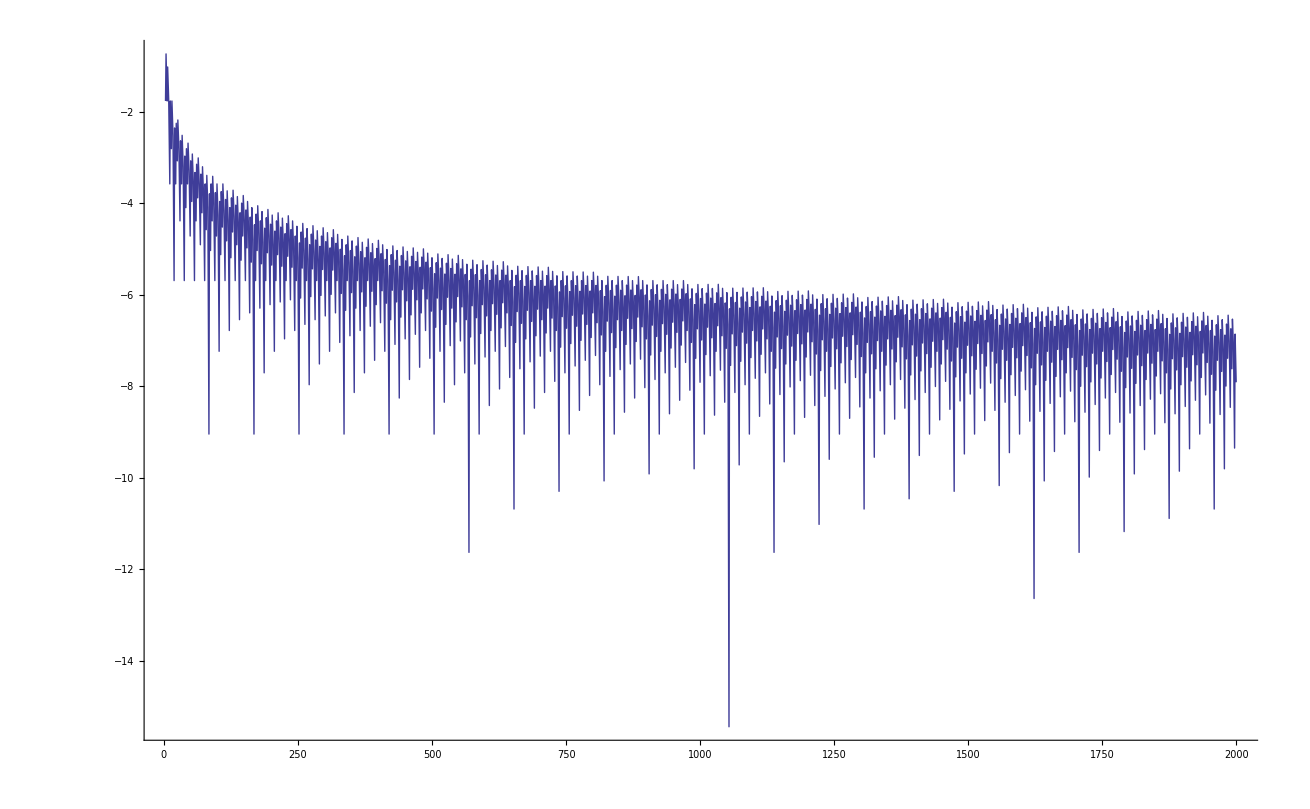

```mathematica
ListLinePlot[
Map[
{#[[1]],N[Log[3-#[[2]]]]}&,With[
{values=ReadList["c:\\temp\\roots.txt",Expression]},
Select[values,Length[FactorList[#[[3]]]]==2&]]],
PlotRange->All
]
```

```mathematica
TableForm[
Select[
Map[
{#[[2]],#[[1]],Factor[#[[3]]],N[Exponent[First[Factor[#[[3]]]],x]/#[[1]]]}&,
Sort[
ReadList["c:\\temp\\roots.txt",Expression]
,#1[[2]]>#2[[2]]&]],
#[[1]]<3&
 ]
]
```

First::normal: Nonatomic expression expected at position 1 in First[x].

3. | 1690 | x^1045 (1+x+x^2+x^6+x^8+x^10+x^13+x^15+x^17+x^20+x^21) | 0.618343
3. | 606 | x^365 (1+x+x^2+x^4+x^6+x^7+x^9+x^11+x^13+x^15+x^16+x^17) | 0.60231
3. | 1165 | x^719 (1+x^2) (1+x^6+x^7-x^8-x^9+x^10+x^11-x^12+x^14) | 0.617167
3. | 522 | x^315 (1+x) (1+x^3+x^7-x^8+2 x^9-x^10+x^11+x^13) | 0.603448
3. | 867 | x^533 (1+x+x^2+x^3+x^8+x^9+x^10+x^14) | 0.614764
3. | 1511 | x^940 (1+x+x^3+x^4+x^5+x^11+x^12+x^13) | 0.622105
3. | 568 | x^345 (1+x+x^6+x^8+x^9+x^10+x^11+x^12+x^13) | 0.607394
3. | 1205 | x^748 (1+x+x^2+x^3+x^4) (1-x+x^4-x^6+x^8) | 0.620747
3. | 1937 | x^1211 (1+x^2+x^3+x^4+x^5+x^6+x^7+x^9+x^11) | 0.625194
3. | 1912 | x^1198 (1+x) (1+x^3-x^4+x^5+x^7) | 0.626569
3. | 1604 | x^1001 (1+x+x^3+x^7+x^11) | 0.624065
3. | 1330 | x^829 (1+x^4+x^6+x^7+x^8+x^10) | 0.623308
3. | 1899 | x^1190 (1+x^4+x^5+x^6+x^8) | 0.626646
3. | 1706 | x^1066 (1-x+x^2) (1+x-x^3+x^5+2 x^6+2 x^7+x^8) | 0.624853
3. | 970 | x^602 (1+x^2) (1+x+x^4-x^6+x^8) | 0.620619
3. | 636 | x^391 (1-x+x^2) (1+2 x+2 x^2-x^4-x^5+x^6+2 x^7+x^8) | 0.61478
3. | 612 | x^375 (1+x^6+x^8+x^9+x^11) | 0.612745
3. | 845 | x^524 (1+x+x^5+x^6+x^7+x^9) | 0.620118
3. | 1175 | x^737 (1+x^2+x^3+x^4) | 0.627234
3. | 1053 | x^654 (1+x^2) (1+x^3+x^4+x^7+x^8) | 0.621083
3. | 1007 | x^627 (1+x+x^2+x^3+x^4+x^6+x^7+x^8) | 0.622642
3. | 550 | x^337 (1+x+x^2+x^6+x^10) | 0.612727
3. | 121 | x^64 (1+x+x^3+x^8+x^10+x^11+x^12) | 0.528926
3. | 858 | x^531 (1+x) (1+x^2+x^5-x^6+x^7+x^9) | 0.618881
3. | 276 | x^164 (1+x+x^4+x^6+x^7+x^8+x^10) | 0.594203
3. | 1146 | x^714 (1+x) (1-x+x^2) (1+x^2+x^6) | 0.623037
3. | 1872 | x^1173 (1+x^2+x^3+x^6+x^8) | 0.626603
3. | 1652 | x^1034 (1+x^2+x^4+x^5+x^7+x^8) | 0.625908
3. | 1389 | x^867 (1+x^2+x^3+x^4+x^6+x^7+x^8+x^9) | 0.62419
3. | 1482 | x^929 (1+x) (1+x^2) (1-x^2+x^3) | 0.626856
3. | 1942 | x^1219 (1+x)^2 (1-x+x^2-x^3+x^4) | 0.627703
3. | 1940 | x^1219 (1+x) (1-x+x^2-x^3+x^4) | 0.628351
3. | 113 | x^63 (1+x^4+x^5+x^7+x^8) | 0.557522
3. | 988 | x^617 (1+x^3+x^4+x^5+x^6) | 0.624494
3. | 1457 | x^914 (1+x+x^2) (1-x+x^3) | 0.627316
3. | 598 | x^368 (1+x+x^3+x^5+x^6+x^8+x^9) | 0.615385
3. | 1265 | x^789 (1+x^2+x^6+x^7+x^9) | 0.623715
3. | 487 | x^301 (1+x^5+x^6) | 0.61807
3. | 888 | x^551 (1-x^2+x^4) (1+x^2+x^3+x^4+x^5) | 0.620495
3. | 1660 | x^1039 (1+x+x^2) (1-x+x^2+x^6) | 0.625904
3. | 1576 | x^987 (1+x) (1-x+2 x^2-x^3+x^4+x^6) | 0.626269
3. | 1921 | x^1206 (1+x+x^2+x^6) | 0.627798
3. | 818 | x^507 (1+x+x^3+x^4+x^7+x^9) | 0.619804
3. | 403 | x^245 (1+x^4+x^8+x^9) | 0.60794
3. | 1666 | x^1046 (1+x) (1+x^2) (1-x+x^2) | 0.627851
3. | 1051 | x^655 (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4) | 0.623216
3. | 1622 | x^1016 (1+x^2+x^3+x^4+x^5+x^6+x^7) | 0.626387
3. | 886 | x^550 (1+x^4+x^9) | 0.620767
3. | 1541 | x^966 (1+x^5+x^6) | 0.626866
3. | 151 | x^85 (1+x+x^2+x^6+x^9+x^10) | 0.562914
3. | 1167 | x^728 (1+x^4+x^5+x^7+x^8) | 0.623822
3. | 1062 | x^665 (1+x) (1+x^2-x^3+x^4) | 0.626177
3. | 1056 | x^665 (1+x) | 0.629735
3. | 1054 | x^665 | 0.000948767
3. | 428 | x^261 (1+x^3+x^4+x^6+x^9) | 0.609813
3. | 1996 | x^1252 (1+x+x^5+x^6+x^7) | 0.627255
3. | 999 | x^623 (1+x+x^2+x^3+x^4+x^6+x^7) | 0.623624
3. | 942 | x^587 (1+x+x^5+x^6+x^7) | 0.623142
3. | 1387 | x^868 (1+x) (1+x^2) (1-x+x^2-x^3+x^4) | 0.625811
3. | 1958 | x^1228 (1+x^2) (1+x+x^2) (1-x+x^3) | 0.627171
3. | 652 | x^403 (1+x^2+x^4+x^5+x^6+x^7+x^8) | 0.618098
3. | 1221 | x^766 (1+x+x^2+x^3+x^4) | 0.627355
3. | 1568 | x^982 (1+x^2+x^3) (1+x^4) | 0.626276
3. | 1750 | x^1097 (1+x+x^4+x^5+x^7) | 0.626857
3. | 904 | x^563 (1+x^2) (1+x+x^2) (1-x+x^3) | 0.622788
3. | 1620 | x^1015 (1+x^3+x^5+x^7) | 0.626543
3. | 1557 | x^979 (1+x) (1+x^2) | 0.628773
3. | 1555 | x^979 (1+x^2) | 0.629582
3. | 1606 | x^1006 (1+x^2+x^3+x^6+x^7) | 0.626401
3. | 1904 | x^1195 (1+x+x^3+x^5+x^6) | 0.627626
3. | 335 | x^203 (1+x)^2 (1+x^2) (1-x+x^2-x^3+x^4) | 0.60597
3. | 333 | x^203 (1+x) (1+x^2) (1-x+x^2-x^3+x^4) | 0.60961
3. | 1436 | x^899 (1+x) (1-x+2 x^2-x^3+x^4-x^5+x^6) | 0.626045
3. | 1037 | x^647 (1+x) (1+x^2+x^6) | 0.623915
3. | 1035 | x^647 (1+x^2+x^6) | 0.625121
3. | 1650 | x^1035 (1+x^3+x^6) | 0.627273
3. | 696 | x^432 (1+x+x^4+x^5+x^7) | 0.62069
3. | 1097 | x^686 (1+x+x^3+x^4+x^6) | 0.625342
3. | 997 | x^622 (1+x^2+x^4+x^7) | 0.623872
3. | 514 | x^317 (1+x^2+x^3) (1+x^4) | 0.616732
3. | 1419 | x^890 (1+x^2+x^4+x^5) | 0.627202
3. | 566 | x^350 (1+x^3+x^5+x^7) | 0.618375
3. | 850 | x^530 (1+x+x^3+x^5+x^6) | 0.623529
3. | 1246 | x^781 (1+x+x^2+x^3+x^5) | 0.626806
3. | 1547 | x^970 (1+x+x^2+x^3+x^6) | 0.62702
3. | 503 | x^314 (1+x) (1+x^2) | 0.624254
3. | 1503 | x^942 (1+x) (1+x^2) (1-x+x^3) | 0.626747
3. | 501 | x^314 (1+x^2) | 0.626747
3. | 552 | x^341 (1+x^2+x^3+x^6+x^7) | 0.617754
3. | 1371 | x^859 (1+x+x^6) | 0.62655
3. | 1731 | x^1086 (1+x^2) (1+x+x^4) | 0.627383
3. | 967 | x^605 (1+x+x^3+x^5) | 0.625646
3. | 1230 | x^772 (1+x+x^4) | 0.627642
3. | 1539 | x^965 (1+x^2) (1-x^2+x^4) | 0.627031
3. | 457 | x^281 (1+x) (1+x^2) (1-x+x^4) | 0.61488
3. | 211 | x^125 (1+x+x^5+x^6+x^8) | 0.592417
3. | 1452 | x^910 (1+x+x^2+x^4+x^6) | 0.626722
3. | 382 | x^234 (1+x) (1-x+2 x^2-x^3+x^4-x^5+x^6) | 0.612565
3. | 167 | x^101 (1+x+x^2+x^3+x^4) | 0.60479
3. | 596 | x^370 (1+x^3+x^6) | 0.620805
3. | 986 | x^616 (1+x^4+x^6) | 0.624746
3. | 1018 | x^639 (1+x^2+x^3) | 0.627701
3. | 111 | x^62 (1+x^5+x^8) | 0.558559
3. | 1715 | x^1076 (1+x^2+x^3+x^6) | 0.627405
3. | 1834 | x^1154 (1+x+x^3) | 0.629226
3. | 1956 | x^1229 (1+x^3+x^5) | 0.628323
3. | 1427 | x^895 (1+x) (1-x+x^2+x^4) | 0.62719
3. | 1566 | x^983 (1+x^2+x^5) | 0.627714
3. | 365 | x^225 (1+x^2+x^4+x^5) | 0.616438
3. | 1774 | x^1115 (1+x^3+x^4) | 0.628523
3. | 677 | x^421 (1+x^2) (1+x+x^4) | 0.621861
3. | 493 | x^305 (1+x+x^2+x^3+x^6) | 0.618661
3. | 1473 | x^924 (1+x^2+x^3+x^4+x^5) | 0.627291
3. | 1736 | x^1091 (1+x)^2 (1-x+x^2) | 0.628456
3. | 1734 | x^1091 (1+x) (1-x+x^2) | 0.629181
3. | 1744 | x^1096 (1+x^2+x^3+x^4) | 0.62844
3. | 449 | x^277 (1+x) (1+x^2) (1-x+x^3) | 0.616927
3. | 1414 | x^888 (1+x+x^2+x^4) | 0.628006
3. | 1790 | x^1125 (1+x+x^2+x^3+x^4) | 0.628492
3. | 1988 | x^1249 (1+x^2+x^4+x^5) | 0.62827
3. | 92 | x^50 (1+x+x^2+x^4+x^5+x^8) | 0.543478
3. | 1137 | x^712 (1+x) (1-x+x^2) (1+x+x^2) | 0.626209
3. | 1135 | x^712 (1-x+x^2) (1+x+x^2) | 0.627313
3. | 1091 | x^683 (1+x+x^3+x^4+x^5) | 0.626031
3. | 1631 | x^1024 (1+x) (1+x^2-x^3+x^4) | 0.627836
3. | 1625 | x^1024 (1+x) | 0.630154
3. | 1623 | x^1024 | 0.000616143
3. | 1455 | x^913 (1+x) (1-x+x^2-x^3+x^4) | 0.627491
3. | 485 | x^300 (1+x^2) (1-x^2+x^4) | 0.618557
3. | 1815 | x^1140 (1+x+x^2+x^3+x^5) | 0.628099
3. | 1083 | x^678 (1+x+x^2+x^4+x^5) | 0.626039
3. | 1121 | x^702 (1+x) (1+x^4) | 0.626227
3. | 1119 | x^702 (1+x^4) | 0.627346
3. | 1799 | x^1131 (1+x+x^4) | 0.628683
3. | 780 | x^489 (1+x+x^3) | 0.626923
3. | 902 | x^564 (1+x^3+x^5) | 0.625277
3. | 951 | x^595 (1+x+x^2) (1-x^2+x^3) | 0.625657
3. | 661 | x^411 (1+x^2+x^3+x^6) | 0.621785
3. | 1026 | x^645 (1+x+x^2) | 0.628655
3. | 1536 | x^964 (1+x+x^3+x^5) | 0.627604
3. | 317 | x^194 (1+x+x^6) | 0.611987
3. | 1587 | x^998 (1+x^2+x^3) | 0.628859
3. | 1181 | x^740 (1+x) (1+x^2) (1-x+x^2) | 0.626588
3. | 398 | x^245 (1+x+x^2+x^4+x^6) | 0.615578
3. | 1983 | x^1247 (1+x+x^2+x^4) | 0.628845
2.99999 | 972 | x^608 (1+x+x^2) (1-x+x^3) | 0.625514
2.99999 | 1704 | x^1071 (1-x+x^2) (1+x+x^2) | 0.628521
2.99999 | 1072 | x^673 (1+x) (1+x^2) | 0.627799
2.99999 | 1070 | x^673 (1+x^2) | 0.628972
2.99999 | 192 | x^116 (1+x+x^2+x^3+x^5) | 0.604167
2.99999 | 1688 | x^1061 (1+x^4) | 0.628555
2.99999 | 1520 | x^954 (1+x+x^2) (1-x^2+x^3) | 0.627632
2.99999 | 1471 | x^923 (1+x^3+x^5) | 0.627464
2.99999 | 1595 | x^1004 (1+x+x^2) | 0.629467
2.99999 | 1349 | x^848 (1+x+x^3) | 0.628614
2.99999 | 720 | x^450 (1+x^3+x^4) | 0.625
2.99999 | 934 | x^584 (1+x^2+x^4+x^5) | 0.625268
2.99999 | 1641 | x^1032 (1+x) (1+x^2) | 0.628885
2.99999 | 1639 | x^1032 (1+x^2) | 0.629652
2.99999 | 682 | x^426 (1+x)^2 (1-x+x^2) | 0.624633
2.99999 | 680 | x^426 (1+x) (1-x+x^2) | 0.626471
2.99999 | 1918 | x^1207 (1+x+x^3) | 0.629301
2.99999 | 512 | x^318 (1+x^2+x^5) | 0.621094
2.99999 | 690 | x^431 (1+x^2+x^3+x^4) | 0.624638
2.99999 | 176 | x^107 (1+x+x^4) | 0.607955
2.99999 | 373 | x^230 (1+x) (1-x+x^2+x^4) | 0.616622
2.99999 | 736 | x^460 (1+x+x^2+x^3+x^4) | 0.625
2.99999 | 1289 | x^809 (1+x^3+x^4) | 0.627618
2.99999 | 1251 | x^785 (1+x)^2 (1-x+x^2) | 0.627498
2.99999 | 1249 | x^785 (1+x) (1-x+x^2) | 0.628503
2.99999 | 1858 | x^1168 (1+x^3+x^4) | 0.628633
2.99999 | 1259 | x^790 (1+x^2+x^3+x^4) | 0.627482
2.99999 | 1081 | x^677 (1+x^2+x^5) | 0.626272
2.99999 | 1305 | x^819 (1+x+x^2+x^3+x^4) | 0.627586
2.99999 | 761 | x^475 (1+x+x^2+x^3+x^5) | 0.624179
2.99999 | 1820 | x^1144 (1+x)^2 (1-x+x^2) | 0.628571
2.99999 | 1818 | x^1144 (1+x) (1-x+x^2) | 0.629263
2.99999 | 1828 | x^1149 (1+x^2+x^3+x^4) | 0.628556
2.99999 | 1874 | x^1178 (1+x+x^2+x^3+x^4) | 0.628602
2.99999 | 745 | x^466 (1+x+x^4) | 0.625503
2.99999 | 1314 | x^825 (1+x+x^4) | 0.627854
2.99999 | 1883 | x^1184 (1+x+x^4) | 0.628784
2.99999 | 577 | x^359 (1+x) (1+x^2-x^3+x^4) | 0.622184
2.99999 | 571 | x^359 (1+x) | 0.628722
2.99999 | 1140 | x^718 (1+x) | 0.629825
2.99999 | 1709 | x^1077 (1+x) | 0.630193
2.99999 | 1707 | x^1077 | 0.000585823
2.99999 | 1138 | x^718 | 0.000878735
2.99999 | 569 | x^359 | 0.00175747
2.99999 | 419 | x^259 (1+x^2+x^3+x^4+x^5) | 0.618138
2.99999 | 1498 | x^941 (1+x+x^2+x^4) | 0.628171
2.99999 | 929 | x^582 (1+x+x^2+x^4) | 0.62648
2.99999 | 1671 | x^1051 (1+x^2+x^3) | 0.628965
2.99999 | 1788 | x^1124 (1-x+x^2) (1+x+x^2) | 0.628635
2.99999 | 1102 | x^692 (1+x^2+x^3) | 0.627949
2.99999 | 1772 | x^1114 (1+x^4) | 0.628668
2.99999 | 1219 | x^765 (1-x+x^2) (1+x+x^2) | 0.627564
2.99999 | 360 | x^223 (1+x+x^2+x^4) | 0.619444
2.99999 | 1679 | x^1057 (1+x+x^2) | 0.629541
2.99999 | 1203 | x^755 (1+x^4) | 0.627598
2.99999 | 401 | x^248 (1+x) (1-x+x^2-x^3+x^4) | 0.618454
2.99999 | 1725 | x^1085 (1+x) (1+x^2) | 0.628986
2.99999 | 1723 | x^1085 (1+x^2) | 0.629716
2.99999 | 533 | x^333 (1+x^2+x^3) | 0.624765
2.99999 | 1433 | x^901 (1+x+x^3) | 0.628751
2.99999 | 482 | x^299 (1+x+x^3+x^5) | 0.620332
2.99999 | 1110 | x^698 (1+x+x^2) | 0.628829
2.99999 | 1902 | x^1197 (1+x) (1-x+x^2) | 0.629338
2.99999 | 650 | x^406 (1-x+x^2) (1+x+x^2) | 0.624615
2.99999 | 1967 | x^1237 (1+x+x^4) | 0.628876
2.99999 | 1156 | x^726 (1+x) (1+x^2) | 0.628028
2.99999 | 1154 | x^726 (1+x^2) | 0.629116
2.99999 | 43 | x^21 (1+x+x^3+x^4+x^6) | 0.488372
2.99999 | 1793 | x^1130 (1+x) | 0.630229
2.99999 | 1791 | x^1130 | 0.000558347
2.99999 | 634 | x^396 (1+x^4) | 0.624606
2.99999 | 1373 | x^862 (1+x^3+x^4) | 0.627822
2.99999 | 1335 | x^838 (1+x)^2 (1-x+x^2) | 0.627715
2.99999 | 1333 | x^838 (1+x) (1-x+x^2) | 0.628657
2.99999 | 864 | x^542 (1+x+x^3) | 0.627315
2.99999 | 1343 | x^843 (1+x^2+x^3+x^4) | 0.627699
2.99998 | 1755 | x^1104 (1+x^2+x^3) | 0.62906
2.99998 | 1582 | x^994 (1+x+x^2+x^4) | 0.628319
2.99998 | 1398 | x^878 (1+x+x^4) | 0.62804
2.99998 | 1856 | x^1167 (1+x^4) | 0.628772
2.99998 | 1224 | x^771 (1+x) | 0.629902
2.99998 | 1222 | x^771 | 0.000818331
2.99998 | 1763 | x^1110 (1+x+x^2) | 0.629609
2.99998 | 541 | x^339 (1+x+x^2) | 0.626617
2.99998 | 1809 | x^1138 (1+x) (1+x^2) | 0.629077
2.99998 | 1807 | x^1138 (1+x^2) | 0.629773
2.99998 | 1986 | x^1250 (1+x) (1-x+x^2) | 0.629406
2.99998 | 804 | x^503 (1+x^3+x^4) | 0.625622
2.99998 | 587 | x^367 (1+x) (1+x^2) | 0.625213
2.99998 | 585 | x^367 (1+x^2) | 0.62735
2.99998 | 466 | x^289 (1+x+x^2) (1-x^2+x^3) | 0.620172
2.99998 | 1303 | x^818 (1-x+x^2) (1+x+x^2) | 0.627782
2.99998 | 1186 | x^745 (1+x^2+x^3) | 0.628162
2.99998 | 1517 | x^954 (1+x+x^3) | 0.628873
2.99998 | 1287 | x^808 (1+x^4) | 0.627817
2.99998 | 820 | x^513 (1+x+x^2+x^3+x^4) | 0.62561
2.99998 | 1877 | x^1183 (1+x) | 0.630261
2.99998 | 1875 | x^1183 | 0.000533333
2.99998 | 1013 | x^635 (1+x+x^2+x^4) | 0.626851
2.99998 | 766 | x^479 (1+x)^2 (1-x+x^2) | 0.625326
2.99998 | 764 | x^479 (1+x) (1-x+x^2) | 0.626963
2.99998 | 774 | x^484 (1+x^2+x^3+x^4) | 0.625323
2.99998 | 417 | x^258 (1+x^3+x^5) | 0.618705
2.99998 | 829 | x^519 (1+x+x^4) | 0.626055
2.99998 | 1839 | x^1157 (1+x^2+x^3) | 0.629146
2.99998 | 1194 | x^751 (1+x+x^2) | 0.628978
2.99998 | 1240 | x^779 (1+x) (1+x^2) | 0.628226
2.99998 | 1238 | x^779 (1+x^2) | 0.629241
2.99998 | 1417 | x^891 (1+x) (1-x+x^2) | 0.628793
2.99998 | 1847 | x^1163 (1+x+x^2) | 0.62967
2.99998 | 1893 | x^1191 (1+x) (1+x^2) | 0.62916
2.99998 | 1891 | x^1191 (1+x^2) | 0.629825
2.99998 | 655 | x^412 (1+x) | 0.629008
2.99998 | 1308 | x^824 (1+x) | 0.629969
2.99998 | 1961 | x^1236 (1+x) | 0.630291
2.99998 | 1959 | x^1236 | 0.000510465
2.99998 | 1306 | x^824 | 0.000765697
2.99998 | 653 | x^412 | 0.00153139
2.99998 | 1601 | x^1007 (1+x+x^3) | 0.628982
2.99998 | 948 | x^595 (1+x+x^3) | 0.627637
2.99998 | 1923 | x^1210 (1+x^2+x^3) | 0.629225
2.99998 | 1270 | x^798 (1+x^2+x^3) | 0.628346
2.99997 | 734 | x^459 (1-x+x^2) (1+x+x^2) | 0.625341
2.99997 | 1931 | x^1216 (1+x+x^2) | 0.629726
2.99997 | 1977 | x^1244 (1+x) (1+x^2) | 0.629236
2.99997 | 1975 | x^1244 (1+x^2) | 0.629873
2.99997 | 295 | x^183 (1+x+x^3) | 0.620339
2.99997 | 718 | x^449 (1+x^4) | 0.625348
2.99997 | 1501 | x^944 (1+x) (1-x+x^2) | 0.628914
2.99997 | 1278 | x^804 (1+x+x^2) | 0.629108
2.99997 | 617 | x^386 (1+x^2+x^3) | 0.625608
2.99997 | 1324 | x^832 (1+x) (1+x^2) | 0.628399
2.99997 | 1322 | x^832 (1+x^2) | 0.629349
2.99997 | 1685 | x^1060 (1+x+x^3) | 0.62908
2.99997 | 913 | x^572 (1+x+x^4) | 0.626506
2.99997 | 1392 | x^877 (1+x) | 0.630029
2.99997 | 1390 | x^877 | 0.000719424
2.99997 | 848 | x^532 (1+x) (1-x+x^2) | 0.627358
2.99997 | 625 | x^392 (1+x+x^2) | 0.6272
2.99997 | 671 | x^420 (1+x) (1+x^2) | 0.625931
2.99997 | 669 | x^420 (1+x^2) | 0.627803
2.99997 | 1354 | x^851 (1+x^2+x^3) | 0.628508
2.99997 | 1585 | x^997 (1+x) (1-x+x^2) | 0.629022
2.99997 | 444 | x^276 (1+x+x^2+x^4) | 0.621622
2.99997 | 1032 | x^648 (1+x+x^3) | 0.627907
2.99997 | 1408 | x^885 (1+x) (1+x^2) | 0.628551
2.99997 | 1362 | x^857 (1+x+x^2) | 0.629222
2.99997 | 1406 | x^885 (1+x^2) | 0.629445
2.99997 | 1769 | x^1113 (1+x+x^3) | 0.629169
2.99997 | 739 | x^465 (1+x) | 0.629229
2.99997 | 1476 | x^930 (1+x) | 0.630081
2.99997 | 1474 | x^930 | 0.000678426
2.99997 | 737 | x^465 | 0.00135685
2.99996 | 1669 | x^1050 (1+x) (1-x+x^2) | 0.629119
2.99996 | 1438 | x^904 (1+x^2+x^3) | 0.628651
2.99996 | 802 | x^502 (1+x^4) | 0.625935
2.99996 | 1853 | x^1166 (1+x+x^3) | 0.62925
2.99996 | 932 | x^585 (1+x) (1-x+x^2) | 0.627682
2.99996 | 1492 | x^938 (1+x) (1+x^2) | 0.628686
2.99996 | 1490 | x^938 (1+x^2) | 0.62953
2.99996 | 1446 | x^910 (1+x+x^2) | 0.629322
2.99996 | 701 | x^439 (1+x^2+x^3) | 0.626248
2.99996 | 1116 | x^701 (1+x+x^3) | 0.628136
2.99996 | 1560 | x^983 (1+x) | 0.630128
2.99996 | 1558 | x^983 | 0.000641849
2.99996 | 127 | x^75 (1+x) (1+x^2) (1-x+x^2) | 0.590551
2.99996 | 235 | x^144 (1+x^3+x^4) | 0.612766
2.99996 | 1753 | x^1103 (1+x) (1-x+x^2) | 0.629207
2.99996 | 755 | x^473 (1+x) (1+x^2) | 0.62649
2.99996 | 1522 | x^957 (1+x^2+x^3) | 0.628778
2.99996 | 753 | x^473 (1+x^2) | 0.628154
2.99996 | 709 | x^445 (1+x+x^2) | 0.627645
2.99996 | 251 | x^154 (1+x+x^2+x^3+x^4) | 0.613546
2.99996 | 1574 | x^991 (1+x^2) | 0.629606
2.99996 | 1530 | x^963 (1+x+x^2) | 0.629412
2.99996 | 83 | x^47 (1+x) (1-x+x^2) (1+x+x^2) | 0.566265
2.99996 | 81 | x^47 (1-x+x^2) (1+x+x^2) | 0.580247
2.99996 | 823 | x^518 (1+x) | 0.629405
2.99996 | 1644 | x^1036 (1+x) | 0.63017
2.99996 | 1642 | x^1036 | 0.000609013
2.99996 | 821 | x^518 | 0.00121803
2.99996 | 260 | x^160 (1+x+x^4) | 0.615385
2.99996 | 1837 | x^1156 (1+x) (1-x+x^2) | 0.629287
2.99996 | 1016 | x^638 (1+x) (1-x+x^2) | 0.627953
2.99996 | 1200 | x^754 (1+x+x^3) | 0.628333
2.99995 | 1658 | x^1044 (1+x^2) | 0.629674
2.99995 | 528 | x^329 (1+x+x^2+x^4) | 0.623106
2.99995 | 1614 | x^1016 (1+x+x^2) | 0.629492
2.99995 | 1728 | x^1089 (1+x) | 0.630208
2.99995 | 1726 | x^1089 | 0.000579374
2.99995 | 785 | x^492 (1+x^2+x^3) | 0.626752
2.99995 | 379 | x^236 (1+x+x^3) | 0.622691
2.99995 | 205 | x^125 (1+x^2+x^3+x^4) | 0.609756
2.99995 | 839 | x^526 (1+x) (1+x^2) | 0.626937
2.99995 | 197 | x^120 (1+x)^2 (1-x+x^2) | 0.609137
2.99995 | 837 | x^526 (1+x^2) | 0.628435
2.99995 | 195 | x^120 (1+x) (1-x+x^2) | 0.615385
2.99995 | 1284 | x^807 (1+x+x^3) | 0.628505
2.99995 | 1742 | x^1097 (1+x^2) | 0.629736
2.99995 | 793 | x^498 (1+x+x^2) | 0.627995
2.99995 | 1698 | x^1069 (1+x+x^2) | 0.629564
2.99995 | 1100 | x^691 (1+x) (1-x+x^2) | 0.628182
2.99995 | 907 | x^571 (1+x) | 0.629548
2.99995 | 1812 | x^1142 (1+x) | 0.630243
2.99995 | 1810 | x^1142 | 0.000552486
2.99995 | 905 | x^571 | 0.00110497
2.99995 | 1826 | x^1150 (1+x^2) | 0.629792
2.99995 | 1782 | x^1122 (1+x+x^2) | 0.62963
2.99995 | 1896 | x^1195 (1+x) | 0.630274
2.99995 | 1894 | x^1195 | 0.000527983
2.99995 | 1368 | x^860 (1+x+x^3) | 0.628655
2.99995 | 869 | x^545 (1+x^2+x^3) | 0.627158
2.99995 | 1184 | x^744 (1+x) (1-x+x^2) | 0.628378
2.99995 | 923 | x^579 (1+x) (1+x^2) | 0.627302
2.99995 | 921 | x^579 (1+x^2) | 0.628664
2.99995 | 1910 | x^1203 (1+x^2) | 0.629843
2.99994 | 991 | x^624 (1+x) | 0.629667
2.99994 | 1980 | x^1248 (1+x) | 0.630303
2.99994 | 1978 | x^1248 | 0.000505561
2.99994 | 989 | x^624 | 0.00101112
2.99994 | 1866 | x^1175 (1+x+x^2) | 0.629689
2.99994 | 877 | x^551 (1+x+x^2) | 0.628278
2.99994 | 1994 | x^1256 (1+x^2) | 0.62989
2.99994 | 67 | x^37 (1+x) (1+x^4) | 0.552239
2.99994 | 1950 | x^1228 (1+x+x^2) | 0.629744
2.99994 | 1268 | x^797 (1+x) (1-x+x^2) | 0.628549
2.99994 | 953 | x^598 (1+x^2+x^3) | 0.627492
2.99994 | 65 | x^37 (1+x^4) | 0.569231
2.99994 | 463 | x^289 (1+x+x^3) | 0.62419
2.99994 | 1005 | x^632 (1+x^2) | 0.628856
2.99994 | 319 | x^197 (1+x^3+x^4) | 0.617555
2.99994 | 1075 | x^677 (1+x) | 0.629767
2.99994 | 1073 | x^677 | 0.000931966
2.99994 | 961 | x^604 (1+x+x^2) | 0.628512
2.99994 | 344 | x^213 (1+x+x^4) | 0.619186
2.99994 | 1352 | x^850 (1+x) (1-x+x^2) | 0.628698
2.99994 | 1089 | x^685 (1+x^2) | 0.629017
2.99994 | 1159 | x^730 (1+x) | 0.629853
2.99994 | 1157 | x^730 | 0.000864304
2.99993 | 1045 | x^657 (1+x+x^2) | 0.628708
2.99993 | 1243 | x^783 (1+x) | 0.629928
2.99993 | 1241 | x^783 | 0.000805802
2.99993 | 1173 | x^738 (1+x^2) | 0.629156
2.99993 | 289 | x^178 (1+x^2+x^3+x^4) | 0.615917
2.99993 | 547 | x^342 (1+x+x^3) | 0.625229
2.99993 | 281 | x^173 (1+x)^2 (1-x+x^2) | 0.615658
2.99993 | 279 | x^173 (1+x) (1-x+x^2) | 0.620072
2.99993 | 1129 | x^710 (1+x+x^2) | 0.628875
2.99993 | 1327 | x^836 (1+x) | 0.629992
2.99993 | 1325 | x^836 | 0.000754717
2.99993 | 1257 | x^791 (1+x^2) | 0.629276
2.99993 | 1213 | x^763 (1+x+x^2) | 0.629019
2.99993 | 1411 | x^889 (1+x) | 0.63005
2.99993 | 1409 | x^889 | 0.000709723
2.99993 | 1341 | x^844 (1+x^2) | 0.629381
2.99992 | 631 | x^395 (1+x+x^3) | 0.62599
2.99992 | 1297 | x^816 (1+x+x^2) | 0.629144
2.99992 | 1495 | x^942 (1+x) | 0.6301
2.99992 | 1493 | x^942 | 0.000669792
2.99992 | 1425 | x^897 (1+x^2) | 0.629474
2.99992 | 1381 | x^869 (1+x+x^2) | 0.629254
2.99992 | 1579 | x^995 (1+x) | 0.630146
2.99992 | 1577 | x^995 | 0.000634115
2.99992 | 1509 | x^950 (1+x^2) | 0.629556
2.99992 | 715 | x^448 (1+x+x^3) | 0.626573
2.99992 | 363 | x^226 (1+x) (1-x+x^2) | 0.62259
2.99992 | 1663 | x^1048 (1+x) | 0.630186
2.99992 | 1465 | x^922 (1+x+x^2) | 0.629352
2.99992 | 1661 | x^1048 | 0.000602047
2.99992 | 165 | x^100 (1-x+x^2) (1+x+x^2) | 0.606061
2.99992 | 1593 | x^1003 (1+x^2) | 0.62963
2.99992 | 1747 | x^1101 (1+x) | 0.630223
2.99992 | 1745 | x^1101 | 0.000573066
2.99992 | 1549 | x^975 (1+x+x^2) | 0.629438
2.99992 | 1677 | x^1056 (1+x^2) | 0.629696
2.99992 | 1831 | x^1154 (1+x) | 0.630257
2.99992 | 1829 | x^1154 | 0.000546747
2.99992 | 799 | x^501 (1+x+x^3) | 0.627034
2.99992 | 1633 | x^1028 (1+x+x^2) | 0.629516
2.99992 | 1761 | x^1109 (1+x^2) | 0.629756
2.99991 | 1915 | x^1207 (1+x) | 0.630287
2.99991 | 1913 | x^1207 | 0.000522739
2.99991 | 1717 | x^1081 (1+x+x^2) | 0.629586
2.99991 | 1845 | x^1162 (1+x^2) | 0.62981
2.99991 | 1999 | x^1260 (1+x) | 0.630315
2.99991 | 1997 | x^1260 | 0.000500751
2.99991 | 883 | x^554 (1+x+x^3) | 0.627407
2.99991 | 447 | x^279 (1+x) (1-x+x^2) | 0.624161
2.99991 | 1801 | x^1134 (1+x+x^2) | 0.62965
2.99991 | 1929 | x^1215 (1+x^2) | 0.62986
2.99991 | 1885 | x^1187 (1+x+x^2) | 0.629708
2.99991 | 1969 | x^1240 (1+x+x^2) | 0.629761
2.99991 | 37 | x^18 (1+x+x^3+x^4+x^5) | 0.486486
2.99991 | 149 | x^90 (1+x^4) | 0.604027
2.99991 | 531 | x^332 (1+x) (1-x+x^2) | 0.625235
2.99991 | 249 | x^153 (1-x+x^2) (1+x+x^2) | 0.614458
2.9999 | 615 | x^385 (1+x) (1-x+x^2) | 0.626016
2.9999 | 699 | x^438 (1+x) (1-x+x^2) | 0.626609
2.9999 | 783 | x^491 (1+x) (1-x+x^2) | 0.627075
2.9999 | 233 | x^143 (1+x^4) | 0.613734
2.99988 | 86 | x^53 (1+x) | 0.616279
2.99988 | 170 | x^106 (1+x) | 0.623529
2.99988 | 254 | x^159 (1+x) | 0.625984
2.99988 | 338 | x^212 (1+x) | 0.627219
2.99988 | 422 | x^265 (1+x) | 0.627962
2.99988 | 506 | x^318 (1+x) | 0.628458
2.99988 | 590 | x^371 (1+x) | 0.628814
2.99988 | 674 | x^424 (1+x) | 0.62908
2.99988 | 758 | x^477 (1+x) | 0.629288
2.99988 | 842 | x^530 (1+x) | 0.629454
2.99988 | 926 | x^583 (1+x) | 0.62959
2.99988 | 1010 | x^636 (1+x) | 0.629703
2.99988 | 1094 | x^689 (1+x) | 0.629799
2.99988 | 1178 | x^742 (1+x) | 0.629881
2.99988 | 1262 | x^795 (1+x) | 0.629952
2.99988 | 1346 | x^848 (1+x) | 0.630015
2.99988 | 1430 | x^901 (1+x) | 0.63007
2.99988 | 1514 | x^954 (1+x) | 0.630119
2.99988 | 1598 | x^1007 (1+x) | 0.630163
2.99988 | 1682 | x^1060 (1+x) | 0.630202
2.99988 | 1766 | x^1113 (1+x) | 0.630238
2.99988 | 1850 | x^1166 (1+x) | 0.63027
2.99988 | 1934 | x^1219 (1+x) | 0.6303
2.99988 | 1932 | x^1219 | 0.000517598
2.99988 | 1848 | x^1166 | 0.000541126
2.99988 | 1764 | x^1113 | 0.000566893
2.99988 | 1680 | x^1060 | 0.000595238
2.99988 | 1596 | x^1007 | 0.000626566
2.99988 | 1512 | x^954 | 0.000661376
2.99988 | 1428 | x^901 | 0.00070028
2.99988 | 1344 | x^848 | 0.000744048
2.99988 | 1260 | x^795 | 0.000793651
2.99988 | 1176 | x^742 | 0.00085034
2.99988 | 1092 | x^689 | 0.000915751
2.99988 | 1008 | x^636 | 0.000992063
2.99988 | 924 | x^583 | 0.00108225
2.99988 | 840 | x^530 | 0.00119048
2.99988 | 756 | x^477 | 0.00132275
2.99988 | 672 | x^424 | 0.0014881
2.99988 | 588 | x^371 | 0.00170068
2.99988 | 504 | x^318 | 0.00198413
2.99988 | 420 | x^265 | 0.00238095
2.99988 | 336 | x^212 | 0.00297619
2.99988 | 252 | x^159 | 0.00396825
2.99988 | 168 | x^106 | 0.00595238
2.99988 | 84 | x^53 | 0.0119048
2.99988 | 1948 | x^1227 (1+x^2) | 0.629877
2.99988 | 1864 | x^1174 (1+x^2) | 0.629828
2.99988 | 1780 | x^1121 (1+x^2) | 0.629775
2.99988 | 1696 | x^1068 (1+x^2) | 0.629717
2.99988 | 1612 | x^1015 (1+x^2) | 0.629653
2.99988 | 1528 | x^962 (1+x^2) | 0.629581
2.99988 | 1444 | x^909 (1+x^2) | 0.629501
2.99988 | 1360 | x^856 (1+x^2) | 0.629412
2.99988 | 1276 | x^803 (1+x^2) | 0.62931
2.99988 | 1192 | x^750 (1+x^2) | 0.629195
2.99988 | 1108 | x^697 (1+x^2) | 0.629061
2.99988 | 1024 | x^644 (1+x^2) | 0.628906
2.99988 | 940 | x^591 (1+x^2) | 0.628723
2.99988 | 856 | x^538 (1+x^2) | 0.628505
2.99988 | 772 | x^485 (1+x^2) | 0.628238
2.99988 | 1484 | x^934 (1+x+x^2) | 0.62938
2.99988 | 688 | x^432 (1+x^2) | 0.627907
2.99988 | 1400 | x^881 (1+x+x^2) | 0.629286
2.99988 | 1316 | x^828 (1+x+x^2) | 0.629179
2.99988 | 604 | x^379 (1+x^2) | 0.627483
2.99988 | 1232 | x^775 (1+x+x^2) | 0.629058
2.99988 | 1148 | x^722 (1+x+x^2) | 0.62892
2.99988 | 520 | x^326 (1+x^2) | 0.626923
2.99987 | 1064 | x^669 (1+x+x^2) | 0.628759
2.99987 | 980 | x^616 (1+x+x^2) | 0.628571
2.99987 | 438 | x^273 (1+x) (1+x^2) | 0.623288
2.99987 | 436 | x^273 (1+x^2) | 0.626147
2.99987 | 896 | x^563 (1+x+x^2) | 0.628348
2.99987 | 812 | x^510 (1+x+x^2) | 0.628079
2.99987 | 354 | x^220 (1+x) (1+x^2) | 0.621469
2.99987 | 352 | x^220 (1+x^2) | 0.625
2.99987 | 728 | x^457 (1+x+x^2) | 0.627747
2.99987 | 644 | x^404 (1+x+x^2) | 0.627329
2.99987 | 468 | x^292 (1+x^2+x^3) | 0.623932
2.99987 | 270 | x^167 (1+x) (1+x^2) | 0.618519
2.99987 | 560 | x^351 (1+x+x^2) | 0.626786
2.99987 | 268 | x^167 (1+x^2) | 0.623134
2.99987 | 29 | x^13 (1+x+x^2+x^4+x^5) | 0.448276
2.99987 | 384 | x^239 (1+x^2+x^3) | 0.622396
2.99987 | 476 | x^298 (1+x+x^2) | 0.62605
2.99986 | 186 | x^114 (1+x) (1+x^2) | 0.612903
2.99986 | 392 | x^245 (1+x+x^2) | 0.625
2.99986 | 184 | x^114 (1+x^2) | 0.619565
2.99986 | 300 | x^186 (1+x^2+x^3) | 0.62
2.99986 | 308 | x^192 (1+x+x^2) | 0.623377
2.99985 | 216 | x^133 (1+x^2+x^3) | 0.615741
2.99985 | 1953 | x^1231 (1+x) | 0.630312
2.99985 | 1951 | x^1231 | 0.000512558
2.99985 | 224 | x^139 (1+x+x^2) | 0.620536
2.99985 | 1869 | x^1178 (1+x) | 0.630284
2.99985 | 1867 | x^1178 | 0.000535619
2.99985 | 102 | x^61 (1+x) (1+x^2) | 0.598039
2.99985 | 1785 | x^1125 (1+x) | 0.630252
2.99985 | 1783 | x^1125 | 0.000560852
2.99985 | 100 | x^61 (1+x^2) | 0.61
2.99985 | 1701 | x^1072 (1+x) | 0.630218
2.99985 | 1699 | x^1072 | 0.000588582
2.99984 | 1617 | x^1019 (1+x) | 0.630179
2.99984 | 1615 | x^1019 | 0.000619195
2.99984 | 1533 | x^966 (1+x) | 0.630137
2.99984 | 1531 | x^966 | 0.000653168
2.99984 | 1449 | x^913 (1+x) | 0.63009
2.99984 | 1447 | x^913 | 0.000691085
2.99984 | 132 | x^80 (1+x^2+x^3) | 0.606061
2.99984 | 1463 | x^921 (1+x^2) | 0.629528
2.99984 | 1365 | x^860 (1+x) | 0.630037
2.99984 | 1363 | x^860 | 0.000733676
2.99983 | 1379 | x^868 (1+x^2) | 0.629442
2.99983 | 1281 | x^807 (1+x) | 0.629977
2.99983 | 1279 | x^807 | 0.000781861
2.99983 | 1295 | x^815 (1+x^2) | 0.629344
2.99983 | 1197 | x^754 (1+x) | 0.629908
2.99983 | 1195 | x^754 | 0.00083682
2.99983 | 140 | x^86 (1+x+x^2) | 0.614286
2.99983 | 1211 | x^762 (1+x^2) | 0.629232
2.99983 | 1113 | x^701 (1+x) | 0.629829
2.99983 | 1111 | x^701 | 0.00090009
2.99982 | 1127 | x^709 (1+x^2) | 0.629104
2.99982 | 1029 | x^648 (1+x) | 0.629738
2.99982 | 1027 | x^648 | 0.00097371
2.99982 | 1972 | x^1243 (1+x) | 0.630325
2.99982 | 1043 | x^656 (1+x^2) | 0.628955
2.99982 | 1970 | x^1243 | 0.000507614
2.99982 | 945 | x^595 (1+x) | 0.62963
2.99982 | 1888 | x^1190 (1+x) | 0.630297
2.99982 | 1886 | x^1190 | 0.000530223
2.99982 | 943 | x^595 | 0.00106045
2.99981 | 959 | x^603 (1+x^2) | 0.62878
2.99981 | 1804 | x^1137 (1+x) | 0.630266
2.99981 | 1802 | x^1137 | 0.000554939
2.99981 | 861 | x^542 (1+x) | 0.629501
2.99981 | 1720 | x^1084 (1+x) | 0.630233
2.99981 | 1718 | x^1084 | 0.000582072
2.99981 | 859 | x^542 | 0.00116414
2.99981 | 875 | x^550 (1+x^2) | 0.628571
2.99981 | 1636 | x^1031 (1+x) | 0.630196
2.99981 | 915 | x^575 (1+x+x^2) | 0.628415
2.99981 | 1634 | x^1031 | 0.000611995
2.9998 | 777 | x^489 (1+x) | 0.629344
2.9998 | 1552 | x^978 (1+x) | 0.630155
2.9998 | 1550 | x^978 | 0.000645161
2.9998 | 775 | x^489 | 0.00129032
2.9998 | 791 | x^497 (1+x^2) | 0.628319
2.9998 | 831 | x^522 (1+x+x^2) | 0.628159
2.9998 | 1468 | x^925 (1+x) | 0.630109
2.9998 | 1466 | x^925 | 0.000682128
2.99979 | 693 | x^436 (1+x) | 0.629149
2.99979 | 1384 | x^872 (1+x) | 0.630058
2.99979 | 1382 | x^872 | 0.000723589
2.99979 | 691 | x^436 | 0.00144718
2.99979 | 707 | x^444 (1+x^2) | 0.628006
2.99979 | 747 | x^469 (1+x+x^2) | 0.627845
2.99979 | 1991 | x^1255 (1+x) | 0.630337
2.99979 | 1989 | x^1255 | 0.000502765
2.99979 | 1300 | x^819 (1+x) | 0.63
2.99979 | 1298 | x^819 | 0.000770416
2.99978 | 1907 | x^1202 (1+x) | 0.630309
2.99978 | 1905 | x^1202 | 0.000524934
2.99978 | 609 | x^383 (1+x) | 0.6289
2.99978 | 1216 | x^766 (1+x) | 0.629934
2.99978 | 1823 | x^1149 (1+x) | 0.63028
2.99978 | 1821 | x^1149 | 0.000549149
2.99978 | 1214 | x^766 | 0.000823723
2.99978 | 607 | x^383 | 0.00164745
2.99978 | 663 | x^416 (1+x+x^2) | 0.627451
2.99978 | 623 | x^391 (1+x^2) | 0.627608
2.99977 | 1739 | x^1096 (1+x) | 0.630247
2.99977 | 1737 | x^1096 | 0.000575705
2.99977 | 1132 | x^713 (1+x) | 0.629859
2.99977 | 1130 | x^713 | 0.000884956
2.99977 | 314 | x^195 (1+x+x^3) | 0.621019
2.99977 | 1655 | x^1043 (1+x) | 0.630211
2.99977 | 1653 | x^1043 | 0.000604961
2.99976 | 525 | x^330 (1+x) | 0.628571
2.99976 | 1048 | x^660 (1+x) | 0.629771
2.99976 | 1571 | x^990 (1+x) | 0.630172
2.99976 | 1569 | x^990 | 0.000637349
2.99976 | 1046 | x^660 | 0.000956023
2.99976 | 523 | x^330 | 0.00191205
2.99976 | 579 | x^363 (1+x+x^2) | 0.626943
2.99976 | 539 | x^338 (1+x^2) | 0.627087
2.99976 | 48 | x^27 (1+x^2+x^3) | 0.5625
2.99976 | 1487 | x^937 (1+x) | 0.630128
2.99976 | 1485 | x^937 | 0.000673401
2.99975 | 964 | x^607 (1+x) | 0.629668
2.99975 | 1926 | x^1214 (1+x) | 0.630322
2.99975 | 1924 | x^1214 | 0.000519751
2.99975 | 962 | x^607 | 0.0010395
2.99975 | 978 | x^615 (1+x^2) | 0.628834
2.99975 | 1403 | x^884 (1+x) | 0.630078
2.99975 | 1401 | x^884 | 0.000713776
2.99975 | 56 | x^33 (1+x+x^2) | 0.589286
2.99975 | 1842 | x^1161 (1+x) | 0.630293
2.99975 | 1840 | x^1161 | 0.000543478
2.99974 | 495 | x^310 (1+x+x^2) | 0.626263
2.99974 | 441 | x^277 (1+x) | 0.628118
2.99974 | 880 | x^554 (1+x) | 0.629545
2.99974 | 1319 | x^831 (1+x) | 0.630023
2.99974 | 1758 | x^1108 (1+x) | 0.630262
2.99974 | 1756 | x^1108 | 0.000569476
2.99974 | 1317 | x^831 | 0.000759301
2.99974 | 878 | x^554 | 0.00113895
2.99974 | 439 | x^277 | 0.0022779
2.99974 | 894 | x^562 (1+x^2) | 0.628635
2.99974 | 455 | x^285 (1+x^2) | 0.626374
2.99973 | 1674 | x^1055 (1+x) | 0.630227
2.99973 | 1672 | x^1055 | 0.000598086
2.99973 | 1235 | x^778 (1+x) | 0.62996
2.99973 | 1233 | x^778 | 0.00081103
2.99973 | 230 | x^142 (1+x+x^3) | 0.617391
2.99973 | 796 | x^501 (1+x) | 0.629397
2.99973 | 1590 | x^1002 (1+x) | 0.630189
2.99973 | 1588 | x^1002 | 0.000629723
2.99973 | 794 | x^501 | 0.00125945
2.99972 | 810 | x^509 (1+x^2) | 0.628395
2.99972 | 1945 | x^1226 (1+x) | 0.630334
2.99972 | 1943 | x^1226 | 0.000514668
2.99972 | 1151 | x^725 (1+x) | 0.629887
2.99972 | 1149 | x^725 | 0.000870322
2.99972 | 298 | x^185 (1+x) (1-x+x^2) | 0.620805
2.99972 | 1506 | x^949 (1+x) | 0.630146
2.99972 | 1504 | x^949 | 0.000664894
2.99971 | 1861 | x^1173 (1+x) | 0.630306
2.99971 | 1859 | x^1173 | 0.000537924
2.99971 | 411 | x^257 (1+x+x^2) | 0.625304
2.99971 | 357 | x^224 (1+x) | 0.627451
2.99971 | 712 | x^448 (1+x) | 0.629213
2.99971 | 1067 | x^672 (1+x) | 0.629803
2.99971 | 1422 | x^896 (1+x) | 0.630098
2.99971 | 1777 | x^1120 (1+x) | 0.630276
2.99971 | 1775 | x^1120 | 0.00056338
2.99971 | 1420 | x^896 | 0.000704225
2.99971 | 1065 | x^672 | 0.000938967
2.99971 | 710 | x^448 | 0.00140845
2.99971 | 355 | x^224 | 0.0028169
2.99971 | 726 | x^456 (1+x^2) | 0.628099
2.9997 | 371 | x^232 (1+x^2) | 0.625337
2.9997 | 1693 | x^1067 (1+x) | 0.630242
2.9997 | 1691 | x^1067 | 0.000591366
2.9997 | 1338 | x^843 (1+x) | 0.630045
2.9997 | 1336 | x^843 | 0.000748503
2.99969 | 983 | x^619 (1+x) | 0.629705
2.99969 | 1964 | x^1238 (1+x) | 0.630346
2.99969 | 1962 | x^1238 | 0.000509684
2.99969 | 981 | x^619 | 0.00101937
2.99969 | 1609 | x^1014 (1+x) | 0.630205
2.99969 | 1607 | x^1014 | 0.000622278
2.99969 | 27 | x^12 (1+x^2+x^5) | 0.444444
2.99968 | 628 | x^395 (1+x) | 0.628981
2.99968 | 1254 | x^790 (1+x) | 0.629984
2.99968 | 1880 | x^1185 (1+x) | 0.630319
2.99968 | 1878 | x^1185 | 0.000532481
2.99968 | 1252 | x^790 | 0.000798722
2.99968 | 626 | x^395 | 0.00159744
2.99968 | 642 | x^403 (1+x^2) | 0.627726
2.99968 | 18 | x^8 (1+x) (1+x^2) | 0.444444
2.99968 | 1525 | x^961 (1+x) | 0.630164
2.99968 | 1523 | x^961 | 0.000656599
2.99967 | 899 | x^566 (1+x) | 0.629588
2.99967 | 1796 | x^1132 (1+x) | 0.63029
2.99967 | 1794 | x^1132 | 0.000557414
2.99967 | 897 | x^566 | 0.00111483
2.99967 | 1170 | x^737 (1+x) | 0.629915
2.99967 | 1168 | x^737 | 0.000856164
2.99967 | 327 | x^204 (1+x+x^2) | 0.623853
2.99967 | 1441 | x^908 (1+x) | 0.630118
2.99967 | 1439 | x^908 | 0.000694927
2.99966 | 1712 | x^1079 (1+x) | 0.630257
2.99966 | 1710 | x^1079 | 0.000584795
2.99966 | 1981 | x^1250 | 0.000504796
2.99965 | 214 | x^132 (1+x) (1-x+x^2) | 0.616822
2.99965 | 16 | x^8 (1+x^2) | 0.5
2.99965 | 273 | x^171 (1+x) | 0.626374
2.99965 | 544 | x^342 (1+x) | 0.628676
2.99965 | 815 | x^513 (1+x) | 0.629448
2.99965 | 1086 | x^684 (1+x) | 0.629834
2.99965 | 1357 | x^855 (1+x) | 0.630066
2.99965 | 1628 | x^1026 (1+x) | 0.630221
2.99965 | 287 | x^179 (1+x^2) | 0.623693
2.99965 | 558 | x^350 (1+x^2) | 0.62724
2.99965 | 1897 | x^1197 | 0.000527148
2.99965 | 1626 | x^1026 | 0.000615006
2.99965 | 1355 | x^855 | 0.000738007
2.99965 | 1084 | x^684 | 0.000922509
2.99965 | 813 | x^513 | 0.00123001
2.99965 | 542 | x^342 | 0.00184502
2.99965 | 271 | x^171 | 0.00369004
2.99964 | 1813 | x^1144 | 0.000551572
2.99964 | 146 | x^89 (1+x+x^3) | 0.609589
2.99964 | 1544 | x^973 (1+x) | 0.630181
2.99964 | 1542 | x^973 | 0.000648508
2.99964 | 1273 | x^802 (1+x) | 0.630008
2.99964 | 1271 | x^802 | 0.000786782
2.99963 | 1002 | x^631 (1+x) | 0.629741
2.99963 | 2000 | x^1262 | 0.0005
2.99963 | 1000 | x^631 | 0.001
2.99963 | 1729 | x^1091 | 0.000578369
2.99963 | 731 | x^460 (1+x) | 0.629275
2.99963 | 1460 | x^920 (1+x) | 0.630137
2.99963 | 1458 | x^920 | 0.000685871
2.99963 | 729 | x^460 | 0.00137174
2.99962 | 1916 | x^1209 | 0.000521921
2.99962 | 1189 | x^749 (1+x) | 0.629941
2.99962 | 1187 | x^749 | 0.00084246
2.99962 | 1647 | x^1038 (1+x) | 0.630237
2.99962 | 1645 | x^1038 | 0.000607903
2.99961 | 474 | x^297 (1+x^2) | 0.626582
2.99961 | 460 | x^289 (1+x) | 0.628261
2.99961 | 918 | x^578 (1+x) | 0.62963
2.99961 | 1376 | x^867 (1+x) | 0.630087
2.99961 | 1832 | x^1156 | 0.000545852
2.99961 | 1374 | x^867 | 0.000727802
2.99961 | 916 | x^578 | 0.0010917
2.99961 | 458 | x^289 | 0.00218341
2.9996 | 1563 | x^985 (1+x) | 0.630198
2.9996 | 1561 | x^985 | 0.000640615
2.9996 | 1105 | x^696 (1+x) | 0.629864
2.9996 | 1103 | x^696 | 0.000906618
2.9996 | 1748 | x^1103 | 0.000572082
2.99959 | 243 | x^151 (1+x+x^2) | 0.621399
2.99959 | 647 | x^407 (1+x) | 0.629057
2.99959 | 1292 | x^814 (1+x) | 0.630031
2.99959 | 1935 | x^1221 | 0.000516796
2.99959 | 1290 | x^814 | 0.000775194
2.99959 | 645 | x^407 | 0.00155039
2.99959 | 1479 | x^932 (1+x) | 0.630156
2.99959 | 1477 | x^932 | 0.000677048
2.99958 | 834 | x^525 (1+x) | 0.629496
2.99958 | 1664 | x^1050 | 0.000600962
2.99958 | 832 | x^525 | 0.00120192
2.99958 | 1851 | x^1168 | 0.000540249
2.99958 | 1021 | x^643 (1+x) | 0.629775
2.99958 | 1019 | x^643 | 0.000981354
2.99957 | 430 | x^269 (1+x+x^2) | 0.625581
2.99957 | 1208 | x^761 (1+x) | 0.629967
2.99957 | 1206 | x^761 | 0.000829187
2.99957 | 1395 | x^879 (1+x) | 0.630108
2.99957 | 1393 | x^879 | 0.000717875
2.99957 | 1580 | x^997 | 0.000632911
2.99957 | 1767 | x^1115 | 0.000565931
2.99956 | 1954 | x^1233 | 0.000511771
2.99956 | 203 | x^126 (1+x^2) | 0.62069
2.99955 | 390 | x^244 (1+x^2) | 0.625641
2.99955 | 189 | x^118 (1+x) | 0.624339
2.99955 | 376 | x^236 (1+x) | 0.62766
2.99955 | 563 | x^354 (1+x) | 0.628774
2.99955 | 750 | x^472 (1+x) | 0.629333
2.99955 | 937 | x^590 (1+x) | 0.629669
2.99955 | 1124 | x^708 (1+x) | 0.629893
2.99955 | 1311 | x^826 (1+x) | 0.630053
2.99955 | 1870 | x^1180 | 0.000534759
2.99955 | 1683 | x^1062 | 0.000594177
2.99955 | 1496 | x^944 | 0.000668449
2.99955 | 1309 | x^826 | 0.000763942
2.99955 | 1122 | x^708 | 0.000891266
2.99955 | 935 | x^590 | 0.00106952
2.99955 | 748 | x^472 | 0.0013369
2.99955 | 561 | x^354 | 0.00178253
2.99955 | 374 | x^236 | 0.0026738
2.99955 | 187 | x^118 | 0.00534759
2.99954 | 1973 | x^1245 | 0.000506842
2.99953 | 1786 | x^1127 | 0.00055991
2.99953 | 1599 | x^1009 | 0.000625391
2.99953 | 1412 | x^891 | 0.000708215
2.99953 | 1227 | x^773 (1+x) | 0.629992
2.99953 | 1225 | x^773 | 0.000816327
2.99952 | 1040 | x^655 (1+x) | 0.629808
2.99952 | 1038 | x^655 | 0.000963391
2.99952 | 1889 | x^1192 | 0.000529381
2.99952 | 853 | x^537 (1+x) | 0.629543
2.99952 | 1702 | x^1074 | 0.000587544
2.99952 | 851 | x^537 | 0.00117509
2.99951 | 1515 | x^956 | 0.000660066
2.99951 | 666 | x^419 (1+x) | 0.629129
2.99951 | 130 | x^79 (1+x) (1-x+x^2) | 0.607692
2.99951 | 1992 | x^1257 | 0.000502008
2.99951 | 1328 | x^838 | 0.000753012
2.99951 | 664 | x^419 | 0.00150602
2.9995 | 1805 | x^1139 | 0.000554017
2.9995 | 1143 | x^720 (1+x) | 0.629921
2.9995 | 1141 | x^720 | 0.000876424
2.9995 | 346 | x^216 (1+x+x^2) | 0.624277
2.9995 | 1618 | x^1021 | 0.000618047
2.99949 | 479 | x^301 (1+x) | 0.628392
2.99949 | 956 | x^602 (1+x) | 0.629707
2.99949 | 1908 | x^1204 | 0.000524109
2.99949 | 1431 | x^903 | 0.000698812
2.99949 | 954 | x^602 | 0.00104822
2.99949 | 477 | x^301 | 0.00209644
2.99948 | 1721 | x^1086 | 0.000581058
2.99948 | 1244 | x^785 | 0.000803859
2.99948 | 769 | x^484 (1+x) | 0.629389
2.99948 | 1534 | x^968 | 0.00065189
2.99948 | 767 | x^484 | 0.00130378
2.99947 | 1824 | x^1151 | 0.000548246
2.99947 | 1059 | x^667 (1+x) | 0.629839
2.99947 | 1057 | x^667 | 0.000946074
2.99947 | 1347 | x^850 | 0.00074239
2.99946 | 1637 | x^1033 | 0.000610874
2.99946 | 306 | x^191 (1+x^2) | 0.624183
2.99946 | 1927 | x^1216 | 0.000518941
2.99946 | 292 | x^183 (1+x) | 0.626712
2.99945 | 582 | x^366 (1+x) | 0.628866
2.99945 | 872 | x^549 (1+x) | 0.629587
2.99945 | 1162 | x^732 (1+x) | 0.629948
2.99945 | 1740 | x^1098 | 0.000574713
2.99945 | 1450 | x^915 | 0.000689655
2.99945 | 1160 | x^732 | 0.000862069
2.99945 | 870 | x^549 | 0.00114943
2.99945 | 580 | x^366 | 0.00172414
2.99945 | 290 | x^183 | 0.00344828
2.99944 | 1843 | x^1163 | 0.000542594
2.99944 | 1553 | x^980 | 0.000643915
2.99944 | 159 | x^98 (1+x+x^2) | 0.616352
2.99944 | 1263 | x^797 | 0.000791766
2.99944 | 975 | x^614 (1+x) | 0.629744
2.99943 | 1946 | x^1228 | 0.000513875
2.99943 | 973 | x^614 | 0.00102775
2.99943 | 1656 | x^1045 | 0.000603865
2.99943 | 685 | x^431 (1+x) | 0.629197
2.99943 | 1366 | x^862 | 0.000732064
2.99943 | 683 | x^431 | 0.00146413
2.99942 | 1759 | x^1110 | 0.000568505
2.99942 | 1078 | x^679 (1+x) | 0.62987
2.99942 | 1076 | x^679 | 0.000929368
2.99942 | 409 | x^256 (1+x^2) | 0.625917
2.99942 | 1469 | x^927 | 0.000680735
2.99941 | 1862 | x^1175 | 0.000537057
2.99941 | 395 | x^248 (1+x) | 0.627848
2.99941 | 788 | x^496 (1+x) | 0.629442
2.99941 | 1965 | x^1240 | 0.000508906
2.99941 | 1572 | x^992 | 0.000636132
2.99941 | 1179 | x^744 | 0.000848176
2.99941 | 786 | x^496 | 0.00127226
2.99941 | 393 | x^248 | 0.00254453
2.9994 | 1675 | x^1057 | 0.000597015
2.9994 | 1282 | x^809 | 0.000780031
2.99939 | 891 | x^561 (1+x) | 0.62963
2.99939 | 1778 | x^1122 | 0.00056243
2.99939 | 889 | x^561 | 0.00112486
2.99939 | 1385 | x^874 | 0.000722022
2.99939 | 1881 | x^1187 | 0.000531632
2.99938 | 498 | x^313 (1+x) | 0.628514
2.99938 | 994 | x^626 (1+x) | 0.629779
2.99938 | 1984 | x^1252 | 0.000504032
2.99938 | 1488 | x^939 | 0.000672043
2.99938 | 992 | x^626 | 0.00100806
2.99938 | 496 | x^313 | 0.00201613
2.99938 | 262 | x^163 (1+x+x^2) | 0.622137
2.99937 | 1591 | x^1004 | 0.000628536
2.99937 | 1095 | x^691 | 0.000913242
2.99937 | 1694 | x^1069 | 0.000590319
2.99936 | 601 | x^378 (1+x) | 0.628952
2.99936 | 1797 | x^1134 | 0.000556483
2.99936 | 1198 | x^756 | 0.000834725
2.99936 | 599 | x^378 | 0.00166945
2.99936 | 1900 | x^1199 | 0.000526316
2.99936 | 1301 | x^821 | 0.00076864
2.99935 | 704 | x^443 (1+x) | 0.629261
2.99935 | 1404 | x^886 | 0.000712251
2.99935 | 702 | x^443 | 0.0014245
2.99935 | 1507 | x^951 | 0.00066357
2.99934 | 807 | x^508 (1+x) | 0.629492
2.99934 | 1610 | x^1016 | 0.000621118
2.99934 | 805 | x^508 | 0.00124224
2.99934 | 1713 | x^1081 | 0.000583771
2.99933 | 910 | x^573 (1+x) | 0.62967
2.99933 | 1816 | x^1146 | 0.000550661
2.99933 | 908 | x^573 | 0.00110132
2.99933 | 1919 | x^1211 | 0.000521105
2.99933 | 1011 | x^638 | 0.00098912
2.99933 | 119 | x^73 (1+x^2) | 0.613445
2.99932 | 1114 | x^703 | 0.000897666
2.99932 | 1217 | x^768 | 0.000821693
2.99932 | 1320 | x^833 | 0.000757576
2.99931 | 1423 | x^898 | 0.000702741
2.99931 | 1526 | x^963 | 0.000655308
2.99931 | 62 | x^36 (1+x+x^3) | 0.580645
2.99931 | 1629 | x^1028 | 0.000613874
2.99931 | 1732 | x^1093 | 0.000577367
2.99931 | 1835 | x^1158 | 0.000544959
2.9993 | 222 | x^138 (1+x^2) | 0.621622
2.9993 | 1938 | x^1223 | 0.000515996
2.9993 | 325 | x^203 (1+x^2) | 0.624615
2.99929 | 105 | x^65 (1+x) | 0.619048
2.99928 | 208 | x^130 (1+x) | 0.625
2.99928 | 311 | x^195 (1+x) | 0.62701
2.99928 | 414 | x^260 (1+x) | 0.628019
2.99928 | 517 | x^325 (1+x) | 0.628627
2.99928 | 620 | x^390 (1+x) | 0.629032
2.99928 | 723 | x^455 (1+x) | 0.629322
2.99928 | 826 | x^520 (1+x) | 0.62954
2.99928 | 1957 | x^1235 | 0.000510986
2.99928 | 1854 | x^1170 | 0.000539374
2.99928 | 1751 | x^1105 | 0.000571102
2.99928 | 1648 | x^1040 | 0.000606796
2.99928 | 1545 | x^975 | 0.000647249
2.99928 | 1442 | x^910 | 0.000693481
2.99928 | 1339 | x^845 | 0.000746826
2.99928 | 1236 | x^780 | 0.000809061
2.99928 | 1133 | x^715 | 0.000882613
2.99928 | 1030 | x^650 | 0.000970874
2.99928 | 927 | x^585 | 0.00107875
2.99928 | 824 | x^520 | 0.00121359
2.99928 | 721 | x^455 | 0.00138696
2.99928 | 618 | x^390 | 0.00161812
2.99928 | 515 | x^325 | 0.00194175
2.99928 | 412 | x^260 | 0.00242718
2.99928 | 309 | x^195 | 0.00323625
2.99928 | 206 | x^130 | 0.00485437
2.99928 | 103 | x^65 | 0.00970874
2.99925 | 1976 | x^1247 | 0.000506073
2.99925 | 1873 | x^1182 | 0.000533903
2.99925 | 1770 | x^1117 | 0.000564972
2.99925 | 1667 | x^1052 | 0.00059988
2.99925 | 1564 | x^987 | 0.000639386
2.99924 | 1461 | x^922 | 0.000684463
2.99924 | 1358 | x^857 | 0.000736377
2.99924 | 1255 | x^792 | 0.000796813
2.99923 | 1152 | x^727 | 0.000868056
2.99923 | 1049 | x^662 | 0.000953289
2.99923 | 1995 | x^1259 | 0.000501253
2.99922 | 1892 | x^1194 | 0.000528541
2.99922 | 946 | x^597 | 0.00105708
2.99922 | 1789 | x^1129 | 0.000558971
2.99922 | 1686 | x^1064 | 0.00059312
2.99922 | 843 | x^532 | 0.00118624
2.99921 | 1583 | x^999 | 0.000631712
2.99921 | 742 | x^467 (1+x) | 0.62938
2.99921 | 1480 | x^934 | 0.000675676
2.99921 | 740 | x^467 | 0.00135135
2.9992 | 1377 | x^869 | 0.000726216
2.9992 | 639 | x^402 (1+x) | 0.629108
2.9992 | 1911 | x^1206 | 0.000523286
2.9992 | 1274 | x^804 | 0.000784929
2.9992 | 637 | x^402 | 0.00156986
2.99919 | 1808 | x^1141 | 0.000553097
2.99919 | 1171 | x^739 | 0.000853971
2.99919 | 1705 | x^1076 | 0.00058651
2.99919 | 536 | x^337 (1+x) | 0.628731
2.99918 | 1602 | x^1011 | 0.00062422
2.99918 | 1068 | x^674 | 0.00093633
2.99918 | 534 | x^337 | 0.00187266
2.99918 | 1499 | x^946 | 0.000667111
2.99917 | 1930 | x^1218 | 0.000518135
2.99917 | 965 | x^609 | 0.00103627
2.99917 | 1396 | x^881 | 0.000716332
2.99917 | 1827 | x^1153 | 0.000547345
2.99916 | 433 | x^272 (1+x) | 0.628176
2.99916 | 1724 | x^1088 | 0.000580046
2.99916 | 1293 | x^816 | 0.000773395
2.99916 | 862 | x^544 | 0.00116009
2.99916 | 431 | x^272 | 0.00232019
2.99915 | 1621 | x^1023 | 0.000616903
2.99915 | 1190 | x^751 | 0.000840336
2.99915 | 1949 | x^1230 | 0.000513084
2.99914 | 1518 | x^958 | 0.000658762
2.99914 | 759 | x^479 | 0.00131752
2.99914 | 1846 | x^1165 | 0.000541712
2.99914 | 1087 | x^686 | 0.000919963
2.99914 | 178 | x^110 (1+x+x^2) | 0.617978
2.99914 | 1415 | x^893 | 0.000706714
2.99913 | 1743 | x^1100 | 0.000573723
2.99913 | 330 | x^207 (1+x) | 0.627273
2.99913 | 658 | x^414 (1+x) | 0.629179
2.99912 | 1968 | x^1242 | 0.00050813
2.99912 | 1640 | x^1035 | 0.000609756
2.99912 | 1312 | x^828 | 0.000762195
2.99912 | 984 | x^621 | 0.00101626
2.99912 | 656 | x^414 | 0.00152439
2.99912 | 328 | x^207 | 0.00304878
2.99912 | 1865 | x^1177 | 0.000536193
2.99911 | 1537 | x^970 | 0.000650618
2.99911 | 1209 | x^763 | 0.00082713
2.99911 | 1762 | x^1112 | 0.000567537
2.99911 | 881 | x^556 | 0.00113507
2.9991 | 1434 | x^905 | 0.00069735
2.9991 | 1987 | x^1254 | 0.000503271
2.9991 | 555 | x^349 (1+x) | 0.628829
2.99909 | 1659 | x^1047 | 0.000602773
2.99909 | 1106 | x^698 | 0.000904159
2.99909 | 553 | x^349 | 0.00180832
2.99909 | 241 | x^150 (1+x^2) | 0.622407
2.99909 | 1884 | x^1189 | 0.000530786
2.99909 | 1331 | x^840 | 0.000751315
2.99908 | 1556 | x^982 | 0.000642674
2.99908 | 778 | x^491 | 0.00128535
2.99908 | 1781 | x^1124 | 0.000561482
2.99908 | 1003 | x^633 | 0.000997009
2.99907 | 1228 | x^775 | 0.000814332
2.99907 | 1453 | x^917 | 0.000688231
2.99907 | 1678 | x^1059 | 0.000595948
2.99907 | 1903 | x^1201 | 0.000525486
2.99906 | 227 | x^142 (1+x) | 0.625551
2.99906 | 452 | x^284 (1+x) | 0.628319
2.99905 | 1800 | x^1136 | 0.000555556
2.99905 | 1575 | x^994 | 0.000634921
2.99905 | 1350 | x^852 | 0.000740741
2.99905 | 1125 | x^710 | 0.000888889
2.99905 | 900 | x^568 | 0.00111111
2.99905 | 675 | x^426 | 0.00148148
2.99905 | 450 | x^284 | 0.00222222
2.99905 | 225 | x^142 | 0.00444444
2.99904 | 1922 | x^1213 | 0.000520291
2.99904 | 1697 | x^1071 | 0.000589275
2.99904 | 1472 | x^929 | 0.000679348
2.99903 | 1247 | x^787 | 0.000801925
2.99903 | 1022 | x^645 | 0.000978474
2.99903 | 1819 | x^1148 | 0.000549753
2.99902 | 1594 | x^1006 | 0.000627353
2.99902 | 797 | x^503 | 0.00125471
2.99902 | 1369 | x^864 | 0.00073046
2.99902 | 1941 | x^1225 | 0.000515198
2.99901 | 574 | x^361 (1+x) | 0.62892
2.99901 | 1716 | x^1083 | 0.000582751
2.99901 | 1144 | x^722 | 0.000874126
2.99901 | 572 | x^361 | 0.00174825
2.99901 | 1491 | x^941 | 0.000670691
2.999 | 1838 | x^1160 | 0.00054407
2.999 | 919 | x^580 | 0.00108814
2.999 | 1266 | x^799 | 0.000789889
2.999 | 1613 | x^1018 | 0.000619963
2.99899 | 1960 | x^1237 | 0.000510204
2.99899 | 349 | x^219 (1+x) | 0.627507
2.99899 | 1735 | x^1095 | 0.000576369
2.99899 | 1388 | x^876 | 0.000720461
2.99899 | 1041 | x^657 | 0.000960615
2.99899 | 694 | x^438 | 0.00144092
2.99899 | 347 | x^219 | 0.00288184
2.99898 | 1857 | x^1172 | 0.000538503
2.99898 | 1510 | x^953 | 0.000662252
2.99897 | 1163 | x^734 | 0.000859845
2.99897 | 1979 | x^1249 | 0.000505306
2.99897 | 1632 | x^1030 | 0.000612745
2.99897 | 816 | x^515 | 0.00122549
2.99896 | 1285 | x^811 | 0.00077821
2.99896 | 1754 | x^1107 | 0.000570125
2.99896 | 471 | x^296 (1+x) | 0.62845
2.99895 | 1876 | x^1184 | 0.000533049
2.99895 | 1407 | x^888 | 0.000710732
2.99895 | 938 | x^592 | 0.0010661
2.99895 | 469 | x^296 | 0.0021322
2.99895 | 138 | x^85 (1+x^2) | 0.615942
2.99895 | 1998 | x^1261 | 0.000500501
2.99895 | 1529 | x^965 | 0.000654022
2.99894 | 1060 | x^669 | 0.000943396
2.99894 | 1651 | x^1042 | 0.000605694
2.99894 | 75 | x^45 (1+x+x^2) | 0.6
2.99894 | 593 | x^373 (1+x) | 0.629005
2.99894 | 1773 | x^1119 | 0.000564016
2.99894 | 1182 | x^746 | 0.000846024
2.99894 | 591 | x^373 | 0.00169205
2.99893 | 1895 | x^1196 | 0.000527704
2.99893 | 1304 | x^823 | 0.000766871
2.99892 | 1426 | x^900 | 0.000701262
2.99892 | 713 | x^450 | 0.00140252
2.99892 | 1548 | x^977 | 0.000645995
2.99891 | 1670 | x^1054 | 0.000598802
2.99891 | 835 | x^527 | 0.0011976
2.99891 | 1792 | x^1131 | 0.000558036
2.99891 | 1914 | x^1208 | 0.000522466
2.99891 | 957 | x^604 | 0.00104493
2.9989 | 1079 | x^681 | 0.000926784
2.9989 | 1201 | x^758 | 0.000832639
2.9989 | 1323 | x^835 | 0.000755858
2.99889 | 1445 | x^912 | 0.000692042
2.99889 | 1567 | x^989 | 0.000638162
2.99889 | 1689 | x^1066 | 0.000592066
2.99889 | 1811 | x^1143 | 0.000552181
2.99889 | 1933 | x^1220 | 0.000517331
2.99887 | 124 | x^77 (1+x) | 0.620968
2.99887 | 246 | x^154 (1+x) | 0.626016
2.99887 | 368 | x^231 (1+x) | 0.627717
2.99887 | 490 | x^308 (1+x) | 0.628571
2.99886 | 1952 | x^1232 | 0.000512295
2.99886 | 1830 | x^1155 | 0.000546448
2.99886 | 1708 | x^1078 | 0.00058548
2.99886 | 1586 | x^1001 | 0.000630517
2.99886 | 1464 | x^924 | 0.00068306
2.99886 | 1342 | x^847 | 0.000745156
2.99886 | 1220 | x^770 | 0.000819672
2.99886 | 1098 | x^693 | 0.000910747
2.99886 | 976 | x^616 | 0.00102459
2.99886 | 854 | x^539 | 0.00117096
2.99886 | 732 | x^462 | 0.00136612
2.99886 | 610 | x^385 | 0.00163934
2.99886 | 488 | x^308 | 0.00204918
2.99886 | 366 | x^231 | 0.00273224
2.99886 | 244 | x^154 | 0.00409836
2.99886 | 122 | x^77 | 0.00819672
2.99884 | 1971 | x^1244 | 0.000507357
2.99884 | 1849 | x^1167 | 0.000540833
2.99884 | 1727 | x^1090 | 0.000579039
2.99884 | 1605 | x^1013 | 0.000623053
2.99883 | 1483 | x^936 | 0.000674309
2.99883 | 1361 | x^859 | 0.000734754
2.99883 | 1239 | x^782 | 0.000807103
2.99882 | 1117 | x^705 | 0.000895255
2.99882 | 46 | x^26 (1+x) (1-x+x^2) | 0.565217
2.99882 | 1990 | x^1256 | 0.000502513
2.99882 | 995 | x^628 | 0.00100503
2.99882 | 1868 | x^1179 | 0.000535332
2.99881 | 1746 | x^1102 | 0.000572738
2.99881 | 873 | x^551 | 0.00114548
2.99881 | 1624 | x^1025 | 0.000615764
2.99881 | 1502 | x^948 | 0.000665779
2.99881 | 751 | x^474 | 0.00133156
2.9988 | 1380 | x^871 | 0.000724638
2.99879 | 1887 | x^1191 | 0.000529942
2.99879 | 1258 | x^794 | 0.000794913
2.99879 | 629 | x^397 | 0.00158983
2.99879 | 1765 | x^1114 | 0.000566572
2.99879 | 1136 | x^717 | 0.000880282
2.99878 | 1643 | x^1037 | 0.000608643
2.99878 | 509 | x^320 (1+x) | 0.628684
2.99878 | 1521 | x^960 | 0.000657462
2.99878 | 1014 | x^640 | 0.000986193
2.99878 | 507 | x^320 | 0.00197239
2.99877 | 1906 | x^1203 | 0.000524659
2.99877 | 1399 | x^883 | 0.000714796
2.99877 | 1784 | x^1126 | 0.000560538
2.99877 | 892 | x^563 | 0.00112108
2.99876 | 1277 | x^806 | 0.000783085
2.99876 | 1662 | x^1049 | 0.000601685
2.99876 | 387 | x^243 (1+x) | 0.627907
2.99875 | 1925 | x^1215 | 0.000519481
2.99875 | 1540 | x^972 | 0.000649351
2.99875 | 1155 | x^729 | 0.000865801
2.99875 | 770 | x^486 | 0.0012987
2.99875 | 385 | x^243 | 0.0025974
2.99874 | 1803 | x^1138 | 0.000554631
2.99874 | 1418 | x^895 | 0.000705219
2.99874 | 1033 | x^652 | 0.000968054
2.99874 | 1681 | x^1061 | 0.000594884
2.99873 | 1944 | x^1227 | 0.000514403
2.99873 | 1296 | x^818 | 0.000771605
2.99873 | 648 | x^409 | 0.00154321
2.99873 | 1559 | x^984 | 0.000641437
2.99872 | 1822 | x^1150 | 0.000548847
2.99872 | 911 | x^575 | 0.00109769
2.99872 | 1174 | x^741 | 0.000851789
2.99871 | 1437 | x^907 | 0.000695894
2.99871 | 1700 | x^1073 | 0.000588235
2.99871 | 1963 | x^1239 | 0.000509424
2.99871 | 265 | x^166 (1+x) | 0.626415
2.9987 | 1841 | x^1162 | 0.000543183
2.9987 | 1578 | x^996 | 0.000633714
2.9987 | 1315 | x^830 | 0.000760456
2.9987 | 1052 | x^664 | 0.00095057
2.9987 | 789 | x^498 | 0.00126743
2.9987 | 526 | x^332 | 0.00190114
2.9987 | 263 | x^166 | 0.00380228
2.99869 | 1982 | x^1251 | 0.000504541
2.99869 | 1719 | x^1085 | 0.000581734
2.99869 | 1456 | x^919 | 0.000686813
2.99868 | 1193 | x^753 | 0.000838223
2.99868 | 1860 | x^1174 | 0.000537634
2.99868 | 930 | x^587 | 0.00107527
2.99868 | 1597 | x^1008 | 0.000626174
2.99867 | 1334 | x^842 | 0.000749625
2.99867 | 667 | x^421 | 0.00149925
2.99867 | 157 | x^97 (1+x^2) | 0.617834
2.99867 | 1738 | x^1097 | 0.000575374
2.99866 | 1071 | x^676 | 0.000933707
2.99866 | 1475 | x^931 | 0.000677966
2.99866 | 1879 | x^1186 | 0.000532198
2.99866 | 406 | x^255 (1+x) | 0.628079
2.99865 | 1616 | x^1020 | 0.000618812
2.99865 | 1212 | x^765 | 0.000825083
2.99865 | 808 | x^510 | 0.00123762
2.99865 | 404 | x^255 | 0.00247525
2.99864 | 1757 | x^1109 | 0.000569152
2.99864 | 1353 | x^854 | 0.000739098
2.99864 | 1898 | x^1198 | 0.00052687
2.99864 | 949 | x^599 | 0.00105374
2.99863 | 1494 | x^943 | 0.000669344
2.99863 | 1635 | x^1032 | 0.000611621
2.99863 | 1090 | x^688 | 0.000917431
2.99863 | 545 | x^344 | 0.00183486
2.99862 | 1776 | x^1121 | 0.000563063
2.99862 | 1231 | x^777 | 0.000812348
2.99862 | 1917 | x^1210 | 0.000521648
2.99861 | 1372 | x^866 | 0.000728863
2.99861 | 686 | x^433 | 0.00145773
2.99861 | 1513 | x^955 | 0.000660939
2.9986 | 1654 | x^1044 | 0.000604595
2.9986 | 827 | x^522 | 0.00120919
2.9986 | 1795 | x^1133 | 0.000557103
2.9986 | 1936 | x^1222 | 0.000516529
2.9986 | 968 | x^611 | 0.00103306
2.99859 | 1109 | x^700 | 0.000901713
2.99859 | 1250 | x^789 | 0.0008
2.99859 | 1391 | x^878 | 0.000718907
2.99858 | 1532 | x^967 | 0.000652742
2.99858 | 1673 | x^1056 | 0.000597729
2.99858 | 1814 | x^1145 | 0.000551268
2.99858 | 1955 | x^1234 | 0.000511509
2.99857 | 143 | x^89 (1+x) | 0.622378
2.99857 | 284 | x^178 (1+x) | 0.626761
2.99856 | 425 | x^267 (1+x) | 0.628235
2.99856 | 1974 | x^1246 | 0.000506586
2.99856 | 1833 | x^1157 | 0.000545554
2.99856 | 1692 | x^1068 | 0.000591017
2.99856 | 1551 | x^979 | 0.000644745
2.99856 | 1410 | x^890 | 0.00070922
2.99856 | 1269 | x^801 | 0.000788022
2.99856 | 1128 | x^712 | 0.000886525
2.99856 | 987 | x^623 | 0.00101317
2.99856 | 846 | x^534 | 0.00118203
2.99856 | 705 | x^445 | 0.00141844
2.99856 | 564 | x^356 | 0.00177305
2.99856 | 423 | x^267 | 0.00236407
2.99856 | 282 | x^178 | 0.0035461
2.99856 | 141 | x^89 | 0.0070922
2.99854 | 1993 | x^1258 | 0.000501756
2.99854 | 1852 | x^1169 | 0.000539957
2.99854 | 1711 | x^1080 | 0.000584454
2.99854 | 1570 | x^991 | 0.000636943
2.99853 | 1429 | x^902 | 0.00069979
2.99853 | 1288 | x^813 | 0.000776398
2.99853 | 1147 | x^724 | 0.00087184
2.99852 | 1006 | x^635 | 0.000994036
2.99852 | 1871 | x^1181 | 0.000534474
2.99852 | 1730 | x^1092 | 0.000578035
2.99852 | 865 | x^546 | 0.00115607
2.99851 | 1589 | x^1003 | 0.000629327
2.99851 | 1448 | x^914 | 0.000690608
2.99851 | 724 | x^457 | 0.00138122
2.9985 | 1307 | x^825 | 0.000765111
2.9985 | 1890 | x^1193 | 0.000529101
2.9985 | 1749 | x^1104 | 0.000571755
2.9985 | 1166 | x^736 | 0.000857633
2.9985 | 583 | x^368 | 0.00171527
2.99849 | 1608 | x^1015 | 0.000621891
2.99849 | 1025 | x^647 | 0.00097561
2.99848 | 1467 | x^926 | 0.000681663
2.99848 | 1909 | x^1205 | 0.000523834
2.99848 | 1768 | x^1116 | 0.000565611
2.99848 | 1326 | x^837 | 0.000754148
2.99848 | 884 | x^558 | 0.00113122
2.99848 | 442 | x^279 | 0.00226244
2.99847 | 1627 | x^1027 | 0.000614628
2.99847 | 1185 | x^748 | 0.000843882
2.99846 | 94 | x^57 (1+x+x^2) | 0.606383
2.99846 | 1928 | x^1217 | 0.000518672
2.99846 | 1486 | x^938 | 0.000672948
2.99846 | 743 | x^469 | 0.0013459
2.99846 | 1787 | x^1128 | 0.000559597
2.99845 | 1044 | x^659 | 0.000957854
2.99845 | 1345 | x^849 | 0.000743494
2.99845 | 1646 | x^1039 | 0.000607533
2.99845 | 1947 | x^1229 | 0.000513611
2.99844 | 303 | x^190 (1+x) | 0.627063
2.99844 | 1806 | x^1140 | 0.00055371
2.99844 | 1505 | x^950 | 0.000664452
2.99844 | 1204 | x^760 | 0.000830565
2.99844 | 903 | x^570 | 0.00110742
2.99844 | 602 | x^380 | 0.00166113
2.99844 | 301 | x^190 | 0.00332226
2.99843 | 1966 | x^1241 | 0.000508647
2.99843 | 1665 | x^1051 | 0.000600601
2.99842 | 1364 | x^861 | 0.000733138
2.99842 | 1063 | x^671 | 0.000940734
2.99842 | 1825 | x^1152 | 0.000547945
2.99841 | 1524 | x^962 | 0.000656168
2.99841 | 762 | x^481 | 0.00131234
2.99841 | 1985 | x^1253 | 0.000503778
2.99841 | 1223 | x^772 | 0.000817661
2.99841 | 1684 | x^1063 | 0.000593824
2.9984 | 1844 | x^1164 | 0.000542299
2.9984 | 1383 | x^873 | 0.000723066
2.9984 | 922 | x^582 | 0.0010846
2.9984 | 461 | x^291 | 0.0021692
2.99839 | 1543 | x^974 | 0.000648088
2.99839 | 1082 | x^683 | 0.000924214
2.99839 | 1703 | x^1075 | 0.000587199
2.99838 | 1863 | x^1176 | 0.000536769
2.99838 | 1242 | x^784 | 0.000805153
2.99838 | 621 | x^392 | 0.00161031
2.99837 | 1402 | x^885 | 0.000713267
2.99837 | 1562 | x^986 | 0.000640205
2.99837 | 781 | x^493 | 0.00128041
2.99837 | 1722 | x^1087 | 0.00058072
2.99836 | 1882 | x^1188 | 0.00053135
2.99836 | 941 | x^594 | 0.0010627
2.99836 | 1101 | x^695 | 0.000908265
2.99835 | 1261 | x^796 | 0.000793021
2.99835 | 1421 | x^897 | 0.00070373
2.99835 | 1581 | x^998 | 0.000632511
2.99835 | 1741 | x^1099 | 0.000574383
2.99835 | 1901 | x^1200 | 0.000526039
2.99834 | 162 | x^101 (1+x) | 0.623457
2.99833 | 322 | x^202 (1+x) | 0.627329
2.99833 | 1920 | x^1212 | 0.000520833
2.99833 | 1760 | x^1111 | 0.000568182
2.99833 | 1600 | x^1010 | 0.000625
2.99833 | 1440 | x^909 | 0.000694444
2.99833 | 1280 | x^808 | 0.00078125
2.99833 | 1120 | x^707 | 0.000892857
2.99833 | 960 | x^606 | 0.00104167
2.99833 | 800 | x^505 | 0.00125
2.99833 | 640 | x^404 | 0.0015625
2.99833 | 480 | x^303 | 0.00208333
2.99833 | 320 | x^202 | 0.003125
2.99833 | 160 | x^101 | 0.00625
2.99831 | 1939 | x^1224 | 0.00051573
2.99831 | 1779 | x^1123 | 0.000562114
2.99831 | 1619 | x^1022 | 0.000617665
2.99831 | 1459 | x^921 | 0.000685401
2.9983 | 1299 | x^820 | 0.000769823
2.9983 | 1139 | x^719 | 0.000877963
2.9983 | 979 | x^618 | 0.00102145
2.99829 | 1798 | x^1135 | 0.000556174
2.99829 | 1638 | x^1034 | 0.000610501
2.99829 | 819 | x^517 | 0.001221
2.99828 | 1478 | x^933 | 0.00067659
2.99828 | 1318 | x^832 | 0.000758725
2.99828 | 659 | x^416 | 0.00151745
2.99827 | 1817 | x^1147 | 0.000550358
2.99827 | 1158 | x^731 | 0.000863558
2.99827 | 1657 | x^1046 | 0.0006035
2.99826 | 1497 | x^945 | 0.000668003
2.99826 | 998 | x^630 | 0.001002
2.99826 | 499 | x^315 | 0.00200401
2.99826 | 1836 | x^1159 | 0.000544662
2.99826 | 1337 | x^844 | 0.000747943
2.99825 | 1676 | x^1058 | 0.000596659
2.99825 | 838 | x^529 | 0.00119332
2.99825 | 1177 | x^743 | 0.000849618
2.99824 | 1516 | x^957 | 0.000659631
2.99824 | 1855 | x^1171 | 0.000539084
2.99824 | 341 | x^214 (1+x) | 0.627566
2.99823 | 1695 | x^1070 | 0.000589971
2.99823 | 1356 | x^856 | 0.000737463
2.99823 | 1017 | x^642 | 0.000983284
2.99823 | 678 | x^428 | 0.00147493
2.99823 | 339 | x^214 | 0.00294985
2.99822 | 1535 | x^969 | 0.000651466
2.99822 | 1196 | x^755 | 0.00083612
2.99821 | 1714 | x^1082 | 0.000583431
2.99821 | 857 | x^541 | 0.00116686
2.99821 | 1375 | x^868 | 0.000727273
2.9982 | 1554 | x^981 | 0.000643501
2.9982 | 1036 | x^654 | 0.000965251
2.9982 | 518 | x^327 | 0.0019305
2.9982 | 1733 | x^1094 | 0.000577034
2.99819 | 1215 | x^767 | 0.000823045
2.99819 | 1394 | x^880 | 0.00071736
2.99819 | 697 | x^440 | 0.00143472
2.99818 | 1573 | x^993 | 0.000635728
2.99818 | 1752 | x^1106 | 0.000570776
2.99818 | 876 | x^553 | 0.00114155
2.99817 | 1055 | x^666 | 0.000947867
2.99817 | 1234 | x^779 | 0.000810373
2.99817 | 1413 | x^892 | 0.000707714
2.99816 | 1592 | x^1005 | 0.000628141
2.99816 | 1771 | x^1118 | 0.000564653
2.99816 | 181 | x^113 (1+x) | 0.624309
2.99815 | 1611 | x^1017 | 0.000620732
2.99815 | 1432 | x^904 | 0.000698324
2.99815 | 1253 | x^791 | 0.000798085
2.99815 | 1074 | x^678 | 0.000931099
2.99815 | 895 | x^565 | 0.00111732
2.99815 | 716 | x^452 | 0.00139665
2.99815 | 537 | x^339 | 0.0018622
2.99815 | 358 | x^226 | 0.0027933
2.99815 | 179 | x^113 | 0.00558659
2.99813 | 1630 | x^1029 | 0.000613497
2.99813 | 1451 | x^916 | 0.00068918
2.99812 | 1272 | x^803 | 0.000786164
2.99812 | 1093 | x^690 | 0.000914913
2.99811 | 914 | x^577 | 0.00109409
2.99811 | 1649 | x^1041 | 0.000606428
2.99811 | 1470 | x^928 | 0.000680272
2.99811 | 735 | x^464 | 0.00136054
2.9981 | 1291 | x^815 | 0.000774593
2.99809 | 1668 | x^1053 | 0.00059952
2.99809 | 1112 | x^702 | 0.000899281
2.99809 | 556 | x^351 | 0.00179856
2.99809 | 1489 | x^940 | 0.000671592
2.99808 | 933 | x^589 | 0.00107181
2.99808 | 1310 | x^827 | 0.000763359
2.99808 | 1687 | x^1065 | 0.000592768
2.99807 | 1508 | x^952 | 0.00066313
2.99807 | 1131 | x^714 | 0.000884173
2.99807 | 754 | x^476 | 0.00132626
2.99807 | 377 | x^238 | 0.00265252
2.99806 | 1329 | x^839 | 0.000752445
2.99805 | 952 | x^601 | 0.00105042
2.99805 | 1527 | x^964 | 0.000654879
2.99805 | 1150 | x^726 | 0.000869565
2.99805 | 575 | x^363 | 0.00173913
2.99804 | 1348 | x^851 | 0.00074184
2.99803 | 1546 | x^976 | 0.000646831
2.99803 | 773 | x^488 | 0.00129366
2.99803 | 971 | x^613 | 0.00102987
2.99802 | 1169 | x^738 | 0.000855432
2.99802 | 1367 | x^863 | 0.000731529
2.99802 | 1565 | x^988 | 0.000638978
2.99801 | 200 | x^125 (1+x) | 0.625
2.998 | 1584 | x^1000 | 0.000631313
2.998 | 1386 | x^875 | 0.000721501
2.998 | 1188 | x^750 | 0.000841751
2.998 | 990 | x^625 | 0.0010101
2.998 | 792 | x^500 | 0.00126263
2.998 | 594 | x^375 | 0.0016835
2.998 | 396 | x^250 | 0.00252525
2.998 | 198 | x^125 | 0.00505051
2.99798 | 1603 | x^1012 | 0.00062383
2.99798 | 35 | x^20 (1+x^2) | 0.571429
2.99798 | 1405 | x^887 | 0.000711744
2.99798 | 1207 | x^762 | 0.0008285
2.99797 | 1009 | x^637 | 0.00099108
2.99797 | 811 | x^512 | 0.00123305
2.99796 | 1424 | x^899 | 0.000702247
2.99796 | 1226 | x^774 | 0.000815661
2.99796 | 613 | x^387 | 0.00163132
2.99795 | 1028 | x^649 | 0.000972763
2.99794 | 1443 | x^911 | 0.000693001
2.99794 | 1245 | x^786 | 0.000803213
2.99794 | 830 | x^524 | 0.00120482
2.99794 | 415 | x^262 | 0.00240964
2.99793 | 1462 | x^923 | 0.000683995
2.99792 | 1047 | x^661 | 0.00095511
2.99792 | 1264 | x^798 | 0.000791139
2.99792 | 632 | x^399 | 0.00158228
2.99791 | 1481 | x^935 | 0.000675219
2.99791 | 849 | x^536 | 0.00117786
2.9979 | 1066 | x^673 | 0.000938086
2.9979 | 1283 | x^810 | 0.000779423
2.99789 | 1500 | x^947 | 0.000666667
2.99789 | 219 | x^137 (1+x) | 0.625571
2.99788 | 1519 | x^959 | 0.000658328
2.99788 | 1302 | x^822 | 0.000768049
2.99788 | 1085 | x^685 | 0.000921659
2.99788 | 868 | x^548 | 0.00115207
2.99788 | 651 | x^411 | 0.0015361
2.99788 | 434 | x^274 | 0.00230415
2.99788 | 217 | x^137 | 0.00460829
2.99786 | 1538 | x^971 | 0.000650195
2.99786 | 1321 | x^834 | 0.000757002
2.99786 | 1104 | x^697 | 0.000905797
2.99785 | 887 | x^560 | 0.0011274
2.99784 | 1340 | x^846 | 0.000746269
2.99784 | 670 | x^423 | 0.00149254
2.99784 | 1123 | x^709 | 0.000890472
2.99782 | 1359 | x^858 | 0.000735835
2.99782 | 906 | x^572 | 0.00110375
2.99782 | 453 | x^286 | 0.00220751
2.99781 | 1142 | x^721 | 0.000875657
2.99781 | 1378 | x^870 | 0.000725689
2.99781 | 689 | x^435 | 0.00145138
2.9978 | 925 | x^584 | 0.00108108
2.9978 | 1161 | x^733 | 0.000861326
2.99779 | 1397 | x^882 | 0.00071582
2.99779 | 238 | x^149 (1+x) | 0.62605
2.99778 | 1416 | x^894 | 0.000706215
2.99778 | 1180 | x^745 | 0.000847458
2.99778 | 944 | x^596 | 0.00105932
2.99778 | 708 | x^447 | 0.00141243
2.99778 | 472 | x^298 | 0.00211864
2.99778 | 236 | x^149 | 0.00423729
2.99776 | 1435 | x^906 | 0.000696864
2.99776 | 1199 | x^757 | 0.000834028
2.99775 | 963 | x^608 | 0.00103842
2.99775 | 1454 | x^918 | 0.000687758
2.99775 | 727 | x^459 | 0.00137552
2.99774 | 1218 | x^769 | 0.000821018
2.99773 | 982 | x^620 | 0.00101833
2.99773 | 491 | x^310 | 0.00203666
2.99772 | 1237 | x^781 | 0.000808407
2.99772 | 746 | x^471 | 0.00134048
2.99771 | 1001 | x^632 | 0.000999001
2.99771 | 1256 | x^793 | 0.000796178
2.9977 | 257 | x^161 (1+x) | 0.626459
2.99769 | 1275 | x^805 | 0.000784314
2.99769 | 1020 | x^644 | 0.000980392
2.99769 | 765 | x^483 | 0.00130719
2.99769 | 510 | x^322 | 0.00196078
2.99769 | 255 | x^161 | 0.00392157
2.99767 | 1294 | x^817 | 0.000772798
2.99767 | 1039 | x^656 | 0.000962464
2.99766 | 784 | x^495 | 0.00127551
2.99766 | 1313 | x^829 | 0.000761615
2.99765 | 1058 | x^668 | 0.00094518
2.99765 | 529 | x^334 | 0.00189036
2.99764 | 1332 | x^841 | 0.000750751
2.99764 | 803 | x^507 | 0.00124533
2.99763 | 1077 | x^680 | 0.000928505
2.99763 | 1351 | x^853 | 0.000740192
2.99761 | 1370 | x^865 | 0.000729927
2.99761 | 1096 | x^692 | 0.000912409
2.99761 | 822 | x^519 | 0.00121655
2.99761 | 548 | x^346 | 0.00182482
2.99761 | 274 | x^173 | 0.00364964
2.9976 | 1115 | x^704 | 0.000896861
2.99759 | 841 | x^531 | 0.00118906
2.99758 | 1134 | x^716 | 0.000881834
2.99758 | 567 | x^358 | 0.00176367
2.99757 | 860 | x^543 | 0.00116279
2.99757 | 1153 | x^728 | 0.000867303
2.99755 | 1172 | x^740 | 0.000853242
2.99755 | 879 | x^555 | 0.00113766
2.99755 | 586 | x^370 | 0.00170648
2.99755 | 293 | x^185 | 0.00341297
2.99753 | 1191 | x^752 | 0.000839631
2.99753 | 898 | x^567 | 0.00111359
2.99752 | 1210 | x^764 | 0.000826446
2.99752 | 605 | x^382 | 0.00165289
2.99751 | 917 | x^579 | 0.00109051
2.99751 | 1229 | x^776 | 0.00081367
2.9975 | 54 | x^32 (1+x^2) | 0.592593
2.99749 | 1248 | x^788 | 0.000801282
2.99749 | 936 | x^591 | 0.00106838
2.99749 | 624 | x^394 | 0.00160256
2.99749 | 312 | x^197 | 0.00320513
2.99748 | 1267 | x^800 | 0.000789266
2.99748 | 955 | x^603 | 0.00104712
2.99747 | 1286 | x^812 | 0.000777605
2.99747 | 643 | x^406 | 0.00155521
2.99746 | 974 | x^615 | 0.00102669
2.99744 | 993 | x^627 | 0.00100705
2.99744 | 662 | x^418 | 0.00151057
2.99744 | 331 | x^209 | 0.00302115
2.99743 | 1012 | x^639 | 0.000988142
2.99742 | 681 | x^430 | 0.00146843
2.99741 | 1031 | x^651 | 0.000969932
2.9974 | 1050 | x^663 | 0.000952381
2.9974 | 700 | x^442 | 0.00142857
2.9974 | 350 | x^221 | 0.00285714
2.99738 | 1069 | x^675 | 0.000935454
2.99738 | 719 | x^454 | 0.00139082
2.99737 | 1088 | x^687 | 0.000919118
2.99736 | 1107 | x^699 | 0.000903342
2.99736 | 738 | x^466 | 0.00135501
2.99736 | 369 | x^233 | 0.00271003
2.99734 | 1126 | x^711 | 0.000888099
2.99734 | 757 | x^478 | 0.001321
2.99733 | 1145 | x^723 | 0.000873362
2.99732 | 1164 | x^735 | 0.000859107
2.99732 | 776 | x^490 | 0.00128866
2.99732 | 388 | x^245 | 0.00257732
2.99731 | 1183 | x^747 | 0.000845309
2.9973 | 795 | x^502 | 0.00125786
2.9973 | 1202 | x^759 | 0.000831947
2.99729 | 814 | x^514 | 0.0012285
2.99729 | 407 | x^257 | 0.002457
2.99727 | 833 | x^526 | 0.00120048
2.99726 | 73 | x^44 (1+x^2) | 0.60274
2.99726 | 852 | x^538 | 0.00117371
2.99726 | 426 | x^269 | 0.00234742
2.99724 | 871 | x^550 | 0.00114811
2.99723 | 890 | x^562 | 0.0011236
2.99723 | 445 | x^281 | 0.00224719
2.99722 | 909 | x^574 | 0.00110011
2.9972 | 928 | x^586 | 0.00107759
2.9972 | 464 | x^293 | 0.00215517
2.99719 | 947 | x^598 | 0.00105597
2.99718 | 966 | x^610 | 0.0010352
2.99718 | 483 | x^305 | 0.00207039
2.99717 | 985 | x^622 | 0.00101523
2.99716 | 1004 | x^634 | 0.000996016
2.99716 | 502 | x^317 | 0.00199203
2.99715 | 1023 | x^646 | 0.000977517
2.99714 | 1042 | x^658 | 0.000959693
2.99714 | 521 | x^329 | 0.00191939
2.99713 | 1061 | x^670 | 0.000942507
2.99712 | 1080 | x^682 | 0.000925926
2.99712 | 540 | x^341 | 0.00185185
2.99711 | 1099 | x^694 | 0.000909918
2.9971 | 1118 | x^706 | 0.000894454
2.9971 | 559 | x^353 | 0.00178891
2.99709 | 578 | x^365 | 0.0017301
2.99707 | 597 | x^377 | 0.00167504
2.99706 | 616 | x^389 | 0.00162338
2.99705 | 635 | x^401 | 0.0015748
2.99703 | 654 | x^413 | 0.00152905
2.99702 | 673 | x^425 | 0.00148588
2.99701 | 692 | x^437 | 0.00144509
2.997 | 711 | x^449 | 0.00140647
2.99699 | 730 | x^461 | 0.00136986
2.99698 | 749 | x^473 | 0.00133511
2.99697 | 768 | x^485 | 0.00130208
2.99696 | 787 | x^497 | 0.00127065
2.99695 | 806 | x^509 | 0.00124069
2.99695 | 825 | x^521 | 0.00121212
2.99694 | 844 | x^533 | 0.00118483
2.99693 | 863 | x^545 | 0.00115875
2.99692 | 882 | x^557 | 0.00113379
2.99692 | 901 | x^569 | 0.00110988
2.99691 | 920 | x^581 | 0.00108696
2.99691 | 939 | x^593 | 0.00106496
2.9969 | 958 | x^605 | 0.00104384
2.99689 | 977 | x^617 | 0.00102354
2.99689 | 996 | x^629 | 0.00100402
2.99688 | 1015 | x^641 | 0.000985222
2.99688 | 1034 | x^653 | 0.000967118
2.99681 | 21 | x^12 (1+x) | 0.571429
2.99672 | 40 | x^24 (1+x) | 0.6
2.99668 | 59 | x^36 (1+x) | 0.610169
2.99667 | 78 | x^48 (1+x) | 0.615385
2.99666 | 97 | x^60 (1+x) | 0.618557
2.99665 | 116 | x^72 (1+x) | 0.62069
2.99664 | 135 | x^84 (1+x) | 0.622222
2.99664 | 154 | x^96 (1+x) | 0.623377
2.99664 | 173 | x^108 (1+x) | 0.624277
2.99661 | 969 | x^612 | 0.00103199
2.99661 | 950 | x^600 | 0.00105263
2.99661 | 931 | x^588 | 0.00107411
2.99661 | 912 | x^576 | 0.00109649
2.99661 | 893 | x^564 | 0.00111982
2.99661 | 874 | x^552 | 0.00114416
2.99661 | 855 | x^540 | 0.00116959
2.99661 | 836 | x^528 | 0.00119617
2.99661 | 817 | x^516 | 0.00122399
2.99661 | 798 | x^504 | 0.00125313
2.99661 | 779 | x^492 | 0.0012837
2.99661 | 760 | x^480 | 0.00131579
2.99661 | 741 | x^468 | 0.00134953
2.99661 | 722 | x^456 | 0.00138504
2.99661 | 703 | x^444 | 0.00142248
2.99661 | 684 | x^432 | 0.00146199
2.99661 | 665 | x^420 | 0.00150376
2.99661 | 646 | x^408 | 0.00154799
2.99661 | 627 | x^396 | 0.0015949
2.99661 | 608 | x^384 | 0.00164474
2.99661 | 589 | x^372 | 0.00169779
2.99661 | 570 | x^360 | 0.00175439
2.99661 | 551 | x^348 | 0.00181488
2.99661 | 532 | x^336 | 0.0018797
2.99661 | 513 | x^324 | 0.00194932
2.99661 | 494 | x^312 | 0.00202429
2.99661 | 475 | x^300 | 0.00210526
2.99661 | 456 | x^288 | 0.00219298
2.99661 | 437 | x^276 | 0.00228833
2.99661 | 418 | x^264 | 0.00239234
2.99661 | 399 | x^252 | 0.00250627
2.99661 | 380 | x^240 | 0.00263158
2.99661 | 361 | x^228 | 0.00277008
2.99661 | 342 | x^216 | 0.00292398
2.99661 | 323 | x^204 | 0.00309598
2.99661 | 304 | x^192 | 0.00328947
2.99661 | 285 | x^180 | 0.00350877
2.99661 | 266 | x^168 | 0.0037594
2.99661 | 247 | x^156 | 0.00404858
2.99661 | 228 | x^144 | 0.00438596
2.99661 | 209 | x^132 | 0.00478469
2.99661 | 190 | x^120 | 0.00526316
2.99661 | 171 | x^108 | 0.00584795
2.99661 | 152 | x^96 | 0.00657895
2.99661 | 133 | x^84 | 0.0075188
2.99661 | 114 | x^72 | 0.00877193
2.99661 | 95 | x^60 | 0.0105263
2.99661 | 76 | x^48 | 0.0131579
2.99661 | 57 | x^36 | 0.0175439
2.99661 | 38 | x^24 | 0.0263158
2.99661 | 19 | x^12 | 0.0526316
2.9963 | 885 | x^559 | 0.00112994
2.9963 | 866 | x^547 | 0.00115473
2.99629 | 847 | x^535 | 0.00118064
2.99628 | 828 | x^523 | 0.00120773
2.99628 | 809 | x^511 | 0.00123609
2.99627 | 790 | x^499 | 0.00126582
2.99626 | 771 | x^487 | 0.00129702
2.99625 | 752 | x^475 | 0.00132979
2.99624 | 733 | x^463 | 0.00136426
2.99623 | 714 | x^451 | 0.00140056
2.99622 | 695 | x^439 | 0.00143885
2.99621 | 676 | x^427 | 0.00147929
2.9962 | 657 | x^415 | 0.00152207
2.99618 | 638 | x^403 | 0.0015674
2.99617 | 619 | x^391 | 0.00161551
2.99616 | 600 | x^379 | 0.00166667
2.99614 | 581 | x^367 | 0.00172117
2.99613 | 562 | x^355 | 0.00177936
2.99611 | 543 | x^343 | 0.00184162
2.99609 | 524 | x^331 | 0.0019084
2.99607 | 505 | x^319 | 0.0019802
2.99605 | 486 | x^307 | 0.00205761
2.99603 | 467 | x^295 | 0.00214133
2.996 | 448 | x^283 | 0.00223214
2.99598 | 429 | x^271 | 0.002331
2.99595 | 410 | x^259 | 0.00243902
2.99593 | 801 | x^506 | 0.00124844
2.99591 | 782 | x^494 | 0.00127877
2.99591 | 391 | x^247 | 0.00255754
2.9959 | 763 | x^482 | 0.00131062
2.99588 | 744 | x^470 | 0.00134409
2.99588 | 372 | x^235 | 0.00268817
2.99586 | 725 | x^458 | 0.00137931
2.99584 | 706 | x^446 | 0.00141643
2.99584 | 353 | x^223 | 0.00283286
2.99582 | 687 | x^434 | 0.0014556
2.99579 | 668 | x^422 | 0.00149701
2.99579 | 334 | x^211 | 0.00299401
2.99577 | 649 | x^410 | 0.00154083
2.99574 | 630 | x^398 | 0.0015873
2.99574 | 315 | x^199 | 0.0031746
2.99572 | 611 | x^386 | 0.00163666
2.99569 | 592 | x^374 | 0.00168919
2.99569 | 296 | x^187 | 0.00337838
2.99566 | 573 | x^362 | 0.0017452
2.99563 | 554 | x^350 | 0.00180505
2.99563 | 277 | x^175 | 0.00361011
2.99559 | 535 | x^338 | 0.00186916
2.99555 | 516 | x^326 | 0.00193798
2.99555 | 258 | x^163 | 0.00387597
2.99551 | 497 | x^314 | 0.00201207
2.99547 | 717 | x^453 | 0.0013947
2.99547 | 478 | x^302 | 0.00209205
2.99547 | 239 | x^151 | 0.0041841
2.99544 | 698 | x^441 | 0.00143266
2.99542 | 459 | x^290 | 0.00217865
2.9954 | 679 | x^429 | 0.00147275
2.99537 | 660 | x^417 | 0.00151515
2.99537 | 440 | x^278 | 0.00227273
2.99537 | 220 | x^139 | 0.00454545
2.99533 | 641 | x^405 | 0.00156006
2.99531 | 421 | x^266 | 0.0023753
2.99529 | 622 | x^393 | 0.00160772
2.99525 | 603 | x^381 | 0.00165837
2.99525 | 402 | x^254 | 0.00248756
2.99525 | 201 | x^127 | 0.00497512
2.99521 | 584 | x^369 | 0.00171233
2.99518 | 383 | x^242 | 0.00261097
2.99516 | 565 | x^357 | 0.00176991
2.99511 | 546 | x^345 | 0.0018315
2.99511 | 364 | x^230 | 0.00274725
2.99511 | 182 | x^115 | 0.00549451
2.99506 | 527 | x^333 | 0.00189753
2.99503 | 345 | x^218 | 0.00289855
2.995 | 508 | x^321 | 0.0019685
2.99493 | 489 | x^309 | 0.00204499
2.99493 | 326 | x^206 | 0.00306748
2.99493 | 163 | x^103 | 0.00613497
2.99488 | 633 | x^400 | 0.00157978
2.99487 | 470 | x^297 | 0.00212766
2.99483 | 614 | x^388 | 0.00162866
2.99483 | 307 | x^194 | 0.00325733
2.99479 | 451 | x^285 | 0.00221729
2.99477 | 595 | x^376 | 0.00168067
2.99471 | 576 | x^364 | 0.00173611
2.99471 | 432 | x^273 | 0.00231481
2.99471 | 288 | x^182 | 0.00347222
2.99471 | 144 | x^91 | 0.00694444
2.99465 | 557 | x^352 | 0.00179533
2.99463 | 413 | x^261 | 0.00242131
2.99458 | 538 | x^340 | 0.00185874
2.99458 | 269 | x^170 | 0.00371747
2.99453 | 394 | x^249 | 0.00253807
2.9945 | 519 | x^328 | 0.00192678
2.99442 | 500 | x^316 | 0.002
2.99442 | 375 | x^237 | 0.00266667
2.99442 | 250 | x^158 | 0.004
2.99442 | 125 | x^79 | 0.008
2.99434 | 481 | x^304 | 0.002079
2.99431 | 356 | x^225 | 0.00280899
2.99424 | 462 | x^292 | 0.0021645
2.99424 | 231 | x^146 | 0.004329
2.99418 | 337 | x^213 | 0.00296736
2.99414 | 443 | x^280 | 0.00225734
2.99412 | 549 | x^347 | 0.00182149
2.9941 | 108 | x^67 (1+x) | 0.62037
2.99403 | 530 | x^335 | 0.00188679
2.99403 | 424 | x^268 | 0.00235849
2.99403 | 318 | x^201 | 0.00314465
2.99403 | 212 | x^134 | 0.00471698
2.99403 | 106 | x^67 | 0.00943396
2.99394 | 511 | x^323 | 0.00195695
2.99391 | 405 | x^256 | 0.00246914
2.99387 | 299 | x^189 | 0.00334448
2.99383 | 492 | x^311 | 0.00203252
2.99378 | 386 | x^244 | 0.00259067
2.99378 | 193 | x^122 | 0.00518135
2.99372 | 473 | x^299 | 0.00211416
2.99368 | 280 | x^177 | 0.00357143
2.99363 | 367 | x^232 | 0.0027248
2.9936 | 454 | x^287 | 0.00220264
2.99356 | 89 | x^55 (1+x) | 0.617978
2.99347 | 435 | x^275 | 0.00229885
2.99347 | 348 | x^220 | 0.00287356
2.99347 | 261 | x^165 | 0.00383142
2.99347 | 174 | x^110 | 0.00574713
2.99347 | 87 | x^55 | 0.0114943
2.99333 | 416 | x^263 | 0.00240385
2.99329 | 329 | x^208 | 0.00303951
2.99322 | 484 | x^306 | 0.00206612
2.99322 | 242 | x^153 | 0.00413223
2.99317 | 397 | x^251 | 0.00251889
2.99308 | 465 | x^294 | 0.00215054
2.99308 | 310 | x^196 | 0.00322581
2.99308 | 155 | x^98 | 0.00645161
2.993 | 378 | x^239 | 0.0026455
2.99293 | 446 | x^282 | 0.00224215
2.99293 | 223 | x^141 | 0.0044843
2.99285 | 291 | x^184 | 0.00343643
2.9928 | 359 | x^227 | 0.00278552
2.99277 | 427 | x^270 | 0.00234192
2.99272 | 70 | x^43 (1+x) | 0.614286
2.99259 | 408 | x^258 | 0.00245098
2.99259 | 340 | x^215 | 0.00294118
2.99259 | 272 | x^172 | 0.00367647
2.99259 | 204 | x^129 | 0.00490196
2.99259 | 136 | x^86 | 0.00735294
2.99259 | 68 | x^43 | 0.0147059
2.9924 | 389 | x^246 | 0.00257069
2.99235 | 321 | x^203 | 0.00311526
2.99229 | 253 | x^160 | 0.00395257
2.99218 | 370 | x^234 | 0.0027027
2.99218 | 185 | x^117 | 0.00540541
2.99209 | 302 | x^191 | 0.00331126
2.99194 | 351 | x^222 | 0.002849
2.99194 | 234 | x^148 | 0.0042735
2.99194 | 117 | x^74 | 0.00854701
2.99183 | 400 | x^253 | 0.0025
2.99178 | 283 | x^179 | 0.00353357
2.99167 | 332 | x^210 | 0.00301205
2.99167 | 166 | x^105 | 0.0060241
2.99159 | 381 | x^241 | 0.00262467
2.99153 | 215 | x^136 | 0.00465116
2.99144 | 264 | x^167 | 0.00378788
2.99137 | 313 | x^198 | 0.00319489
2.99133 | 362 | x^229 | 0.00276243
2.99125 | 51 | x^31 (1+x) | 0.607843
2.99104 | 343 | x^217 | 0.00291545
2.99104 | 294 | x^186 | 0.00340136
2.99104 | 245 | x^155 | 0.00408163
2.99104 | 196 | x^124 | 0.00510204
2.99104 | 147 | x^93 | 0.00680272
2.99104 | 98 | x^62 | 0.0102041
2.99104 | 49 | x^31 | 0.0204082
2.99071 | 324 | x^205 | 0.00308642
2.99065 | 275 | x^174 | 0.00363636
2.99057 | 226 | x^143 | 0.00442478
2.99044 | 177 | x^112 | 0.00564972
2.99034 | 305 | x^193 | 0.00327869
2.99021 | 256 | x^162 | 0.00390625
2.99021 | 128 | x^81 | 0.0078125
2.99001 | 207 | x^131 | 0.00483092
2.98993 | 286 | x^181 | 0.0034965
2.9897 | 316 | x^200 | 0.00316456
2.9897 | 237 | x^150 | 0.00421941
2.9897 | 158 | x^100 | 0.00632911
2.9897 | 79 | x^50 | 0.0126582
2.98945 | 267 | x^169 | 0.00374532
2.98935 | 188 | x^119 | 0.00531915
2.98926 | 297 | x^188 | 0.003367
2.9891 | 218 | x^138 | 0.00458716
2.9891 | 109 | x^69 | 0.00917431
2.98891 | 248 | x^157 | 0.00403226
2.98876 | 278 | x^176 | 0.00359712
2.98876 | 139 | x^88 | 0.00719424
2.98854 | 169 | x^107 | 0.00591716
2.98838 | 199 | x^126 | 0.00502513
2.98827 | 229 | x^145 | 0.00436681
2.98818 | 259 | x^164 | 0.003861
2.98799 | 32 | x^19 (1+x) | 0.59375
2.98752 | 240 | x^152 | 0.00416667
2.98752 | 210 | x^133 | 0.0047619
2.98752 | 180 | x^114 | 0.00555556
2.98752 | 150 | x^95 | 0.00666667
2.98752 | 120 | x^76 | 0.00833333
2.98752 | 90 | x^57 | 0.0111111
2.98752 | 60 | x^38 | 0.0166667
2.98752 | 30 | x^19 | 0.0333333
2.98674 | 221 | x^140 | 0.00452489
2.98662 | 191 | x^121 | 0.0052356
2.98645 | 161 | x^102 | 0.00621118
2.98621 | 131 | x^83 | 0.00763359
2.98604 | 232 | x^147 | 0.00431034
2.98582 | 202 | x^128 | 0.0049505
2.98582 | 101 | x^64 | 0.00990099
2.98552 | 172 | x^109 | 0.00581395
2.98511 | 10 | x^4 (1+x+x^2) | 0.4
2.9851 | 213 | x^135 | 0.00469484
2.9851 | 142 | x^90 | 0.00704225
2.9851 | 71 | x^45 | 0.0140845
2.9847 | 183 | x^116 | 0.00546448
2.98445 | 112 | x^71 | 0.00892857
2.98415 | 153 | x^97 | 0.00653595
2.98398 | 194 | x^123 | 0.00515464
2.98333 | 164 | x^104 | 0.00609756
2.98333 | 123 | x^78 | 0.00813008
2.98333 | 82 | x^52 | 0.0121951
2.98333 | 41 | x^26 | 0.0243902
2.98261 | 175 | x^111 | 0.00571429
2.98239 | 134 | x^85 | 0.00746269
2.98198 | 93 | x^59 | 0.0107527
2.9816 | 145 | x^92 | 0.00689655
2.98092 | 156 | x^99 | 0.00641026
2.98092 | 104 | x^66 | 0.00961538
2.98092 | 52 | x^33 | 0.0192308
2.98006 | 115 | x^73 | 0.00869565
2.97935 | 126 | x^80 | 0.00793651
2.97935 | 63 | x^40 | 0.015873
2.97876 | 137 | x^87 | 0.00729927
2.97826 | 148 | x^94 | 0.00675676
2.97826 | 74 | x^47 | 0.0135135
2.97744 | 85 | x^54 | 0.0117647
2.97682 | 96 | x^61 | 0.0104167
2.97632 | 107 | x^68 | 0.00934579
2.97592 | 118 | x^75 | 0.00847458
2.97558 | 129 | x^82 | 0.00775194
2.97469 | 13 | x^7 (1+x) | 0.538462
2.97341 | 24 | x^14 (1+x) | 0.583333
2.97199 | 110 | x^70 | 0.00909091
2.97199 | 99 | x^63 | 0.010101
2.97199 | 88 | x^56 | 0.0113636
2.97199 | 77 | x^49 | 0.012987
2.97199 | 66 | x^42 | 0.0151515
2.97199 | 55 | x^35 | 0.0181818
2.97199 | 44 | x^28 | 0.0227273
2.97199 | 33 | x^21 | 0.030303
2.97199 | 22 | x^14 | 0.0454545
2.97199 | 11 | x^7 | 0.0909091
2.96692 | 91 | x^58 | 0.010989
2.96622 | 80 | x^51 | 0.0125
2.96531 | 69 | x^44 | 0.0144928
2.96405 | 58 | x^37 | 0.0172414
2.9622 | 47 | x^30 | 0.0212766
2.95922 | 72 | x^46 | 0.0138889
2.95922 | 36 | x^23 | 0.0277778
2.95694 | 61 | x^39 | 0.0163934
2.95365 | 50 | x^32 | 0.02
2.95365 | 25 | x^16 | 0.04
2.95053 | 64 | x^41 | 0.015625
2.94854 | 39 | x^25 | 0.025641
2.94613 | 53 | x^34 | 0.0188679
2.93947 | 42 | x^27 | 0.0238095
2.93947 | 28 | x^18 | 0.0357143
2.93947 | 14 | x^9 | 0.0714286
2.93167 | 45 | x^29 | 0.0222222
2.92817 | 31 | x^20 | 0.0322581
2.91896 | 34 | x^22 | 0.0294118
2.91896 | 17 | x^11 | 0.0588235
2.90485 | 20 | x^13 | 0.05
2.89454 | 23 | x^15 | 0.0434783
2.88668 | 26 | x^17 | 0.0384615
2.87404 | 5 | x^2 (1+x) | 0.4
2.82843 | 15 | x^10 | 0.0666667
2.82843 | 12 | x^8 | 0.0833333
2.82843 | 9 | x^6 | 0.111111
2.82843 | 6 | x^4 | 0.166667
2.82843 | 3 | x^2 | 0.333333
2.63902 | 7 | x^5 | 0.142857
2.51984 | 4 | x^3 | 0.25
2. | 1 | x | 0.

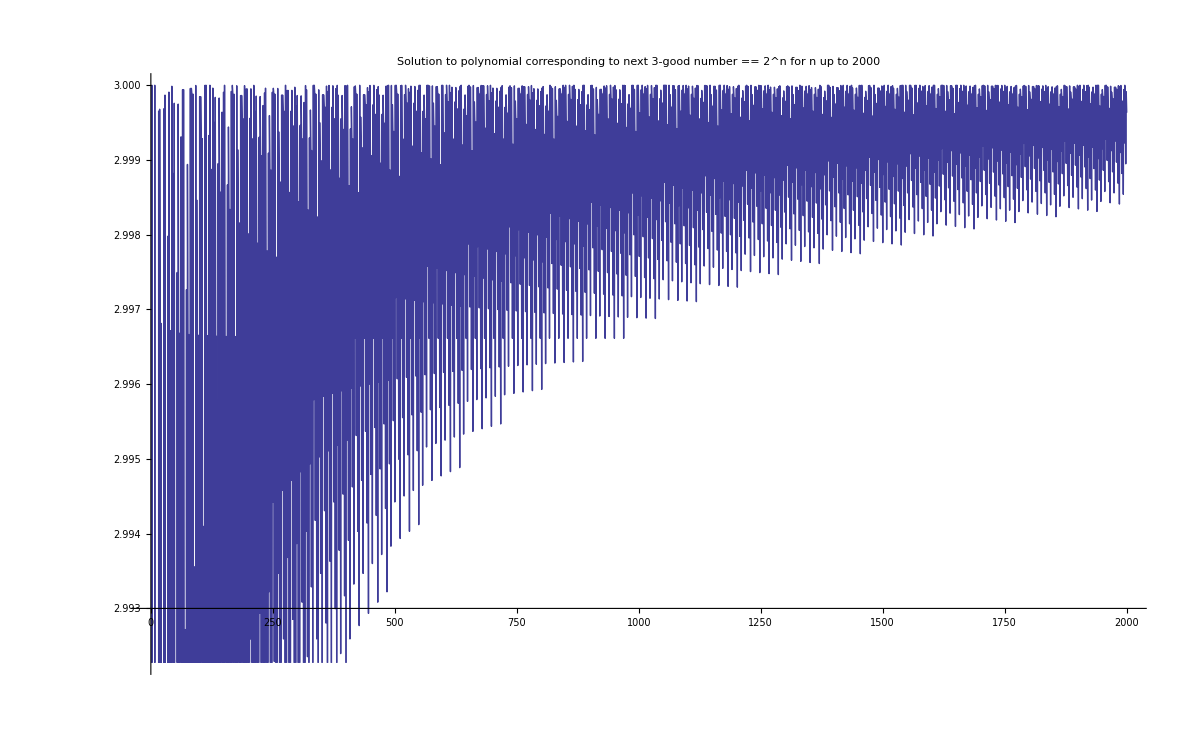

```mathematica
ListLinePlot[
Map[
{#[[1]],#[[2]]}&,ReadList["c:\\temp\\roots.txt",Expression]],
PlotLabel->"Solution to polynomial corresponding to next 3-good number == 2^n for n up to 2000"
]
```

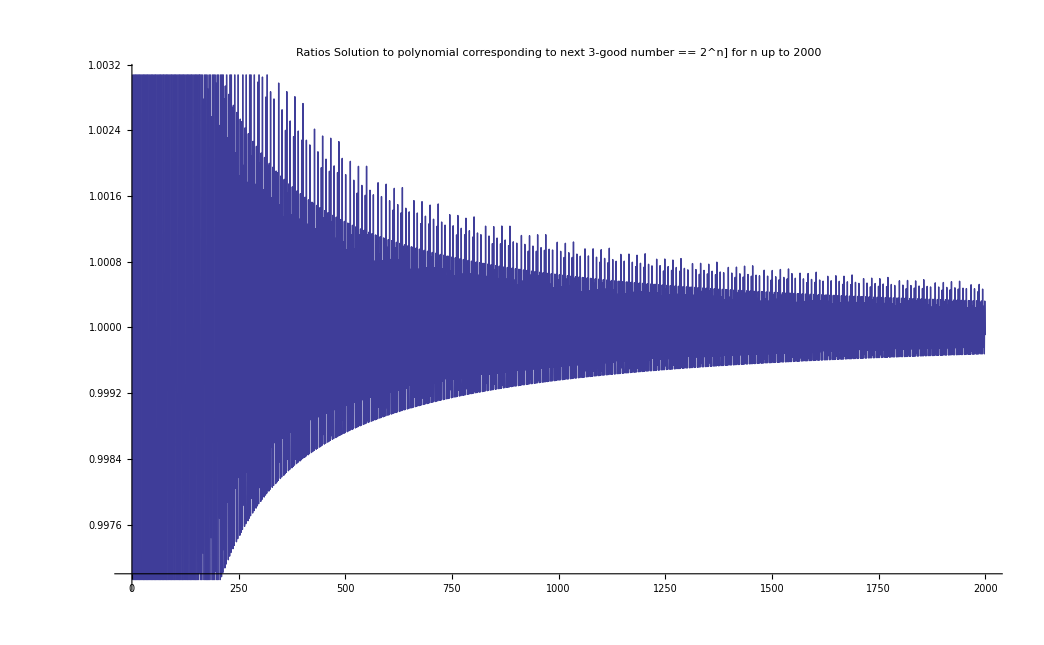

```mathematica
ListLinePlot[
Ratios[
Prepend[Map[
#[[2]]&,ReadList["c:\\temp\\roots.txt",Expression]],3]
],
PlotLabel->"Ratios Solution to polynomial corresponding to next 3-good number == 2^n] for n up to 2000",
PlotRange->Automatic
]
```

```mathematica
FactorInteger[642]
```

{{2,1},{3,1},{107,1}}

```mathematica
LHS
```

```mathematica
(a==1)[[1]]
```

a

```mathematica
RealSol[Flatten[N[Solve[Eq[IntegerDigits[2^100+Distance[2^100,3],3]]==2^99]]]]
```

{2.96692}

```mathematica
RealSol[sols_]:=Module[
{pure},
pure=Flatten[Map[#[[2]]&,Flatten[sols]]];
Select[pure,Im[#]==0 &&#>0&][[1]]
]
```

```mathematica
RealSol[{x->1,x->2}]
```

{1,2}

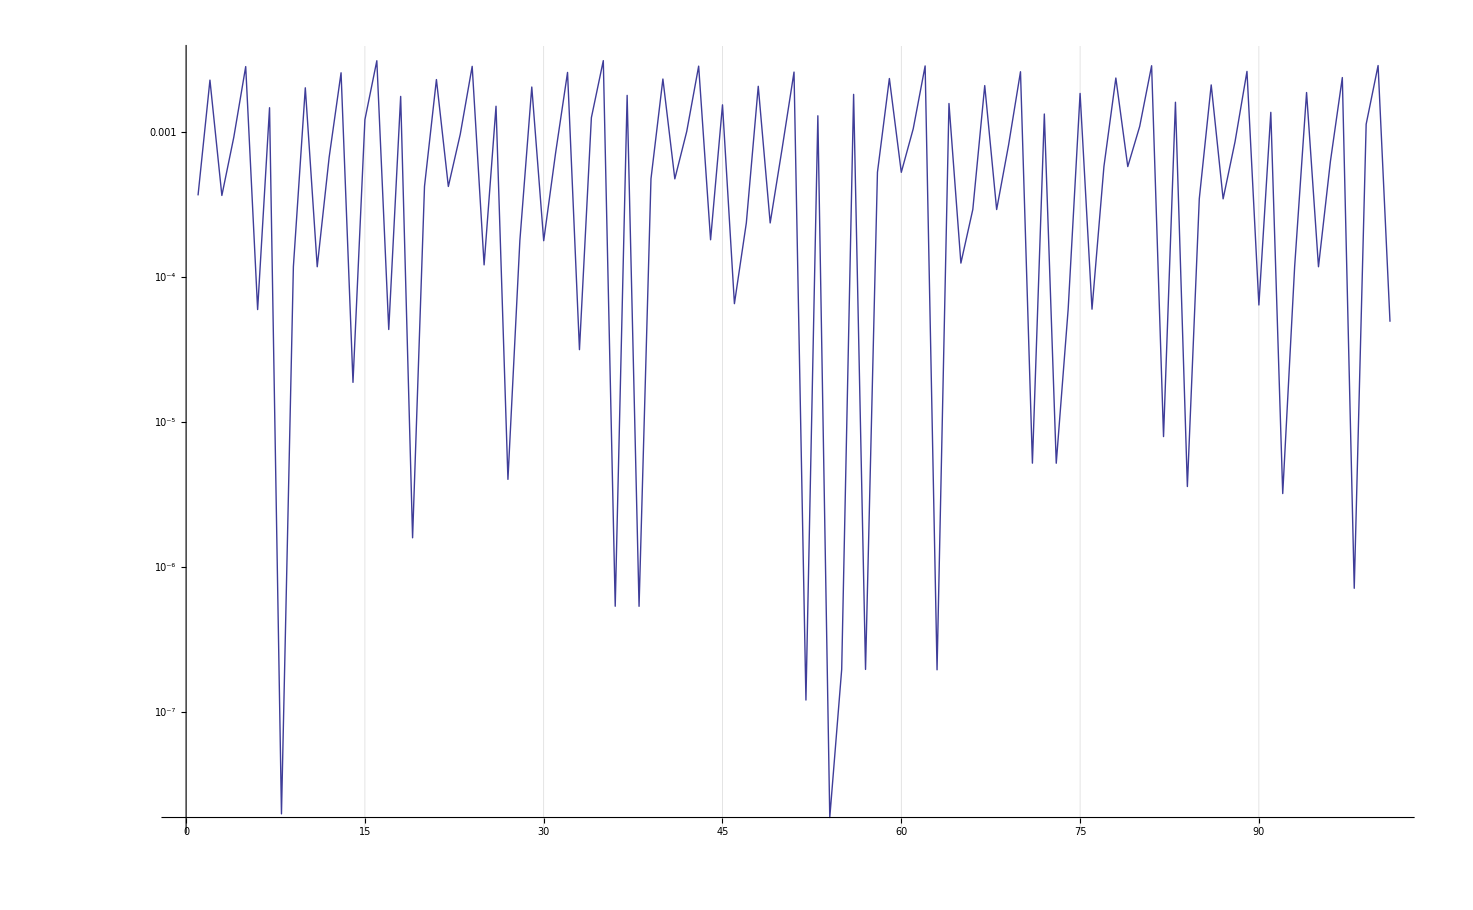

```mathematica
With[
{min=1000,max=1100},
ListLogPlot[
Module[
{probes=Table[IntegerDigits[2^i+Distance[2^i,3],3],{i,min,max,1}], eqs},
eqs=Map[Eq,probes];
Monitor[
3-
Flatten[
Table[
Select[
Flatten[
Map[Solutions,
N[Solve[eqs[[i]]==2^(i-1+min)]]
]
],
Im[#]==0&&#>0&],{i,1,Length[eqs]}]
],
{i+min}
]
],GridLines->{Automatic,{{3,Directive[Red,Thick]}}},PlotRange->Automatic,Joined->True]
]
```

```mathematica
Expand[(1+x) *(1+x^2-x^3+x^4)]
```

1+x+x^2+x^5

```mathematica
IntegerString[2^9,3]
```

200222

```mathematica
Eq[IntegerDigits[2^9+Distance[2^9,3],3]]
```

x^6

```mathematica
Solve[x^6==2^9,x]
```

{{x→-2 √2},{x→2 √2},{x→-2 (-1)^(1/3) √2},{x→2 (-1)^(1/3) √2},{x→-2 (-1)^(2/3) √2},{x→2 (-1)^(2/3) √2}}

```mathematica
N[%]
```

{{x→-2.82843},{x→2.82843},{x→-1.41421-2.44949 ⅈ},{x→1.41421+2.44949 ⅈ},{x→1.41421-2.44949 ⅈ},{x→-1.41421+2.44949 ⅈ}}

```mathematica
RealDigits[2^9,N[2 Sqrt[2]],10]
```

{{1,0,0,0,0,0,0,0,0,0},7}

```mathematica
Solve[x^4 (1+x+x^2)==2^10]
```

{{x→Root[-1024+#1^4+#1^5+#1^6&,1]},{x→Root[-1024+#1^4+#1^5+#1^6&,2]},{x→Root[-1024+#1^4+#1^5+#1^6&,3]},{x→Root[-1024+#1^4+#1^5+#1^6&,4]},{x→Root[-1024+#1^4+#1^5+#1^6&,5]},{x→Root[-1024+#1^4+#1^5+#1^6&,6]}}

```mathematica
Series[a/.%[[1]],{a,0,100}]
```

a+O[a]^101

```mathematica
Series[Root[-1024+#1^4+#1^5+#1^6&,1],x]
```

Series::sspec: Series specification x is not a list with three elements.

```mathematica
Series[Root[-1024+#1^4+#1^5+#1^6&,1],x,10]
```

Series::sspec: Series specification x is not a list with three elements.

Series::sspec: Series specification 10 is not a list with three elements.

```mathematica
Series[x/.x->Root[-1024+a^4+a^5+a^6,1],{a,0,100}]
```

Root[-1024+#1^4+#1^5+#1^6&,1]

{{-√2},{-ⅈ √2},{ⅈ √2},{√2},{-√(1/2+(√5)/2-ⅈ √(1/2 (5-√5)))},{√(1/2+(√5)/2-ⅈ √(1/2 (5-√5)))},{-√(1/2+(√5)/2+ⅈ √(1/2 (5-√5)))},{√(1/2+(√5)/2+ⅈ √(1/2 (5-√5)))},{-√(1/2 (-1-√5-ⅈ √(2 (5-√5))))},{√(1/2 (-1-√5-ⅈ √(2 (5-√5))))},{-√(1/2 (-1-√5+ⅈ √(2 (5-√5))))},{√(1/2 (-1-√5+ⅈ √(2 (5-√5))))},{-√(-1/2+(√5)/2-ⅈ √(1/2 (5+√5)))},{√(-1/2+(√5)/2-ⅈ √(1/2 (5+√5)))},{-√(-1/2+(√5)/2+ⅈ √(1/2 (5+√5)))},{√(-1/2+(√5)/2+ⅈ √(1/2 (5+√5)))},{-√(1/2 (1-√5-ⅈ √(2 (5+√5))))},{√(1/2 (1-√5-ⅈ √(2 (5+√5))))},{-√(1/2 (1-√5+ⅈ √(2 (5+√5))))},{√(1/2 (1-√5+ⅈ √(2 (5+√5))))}}

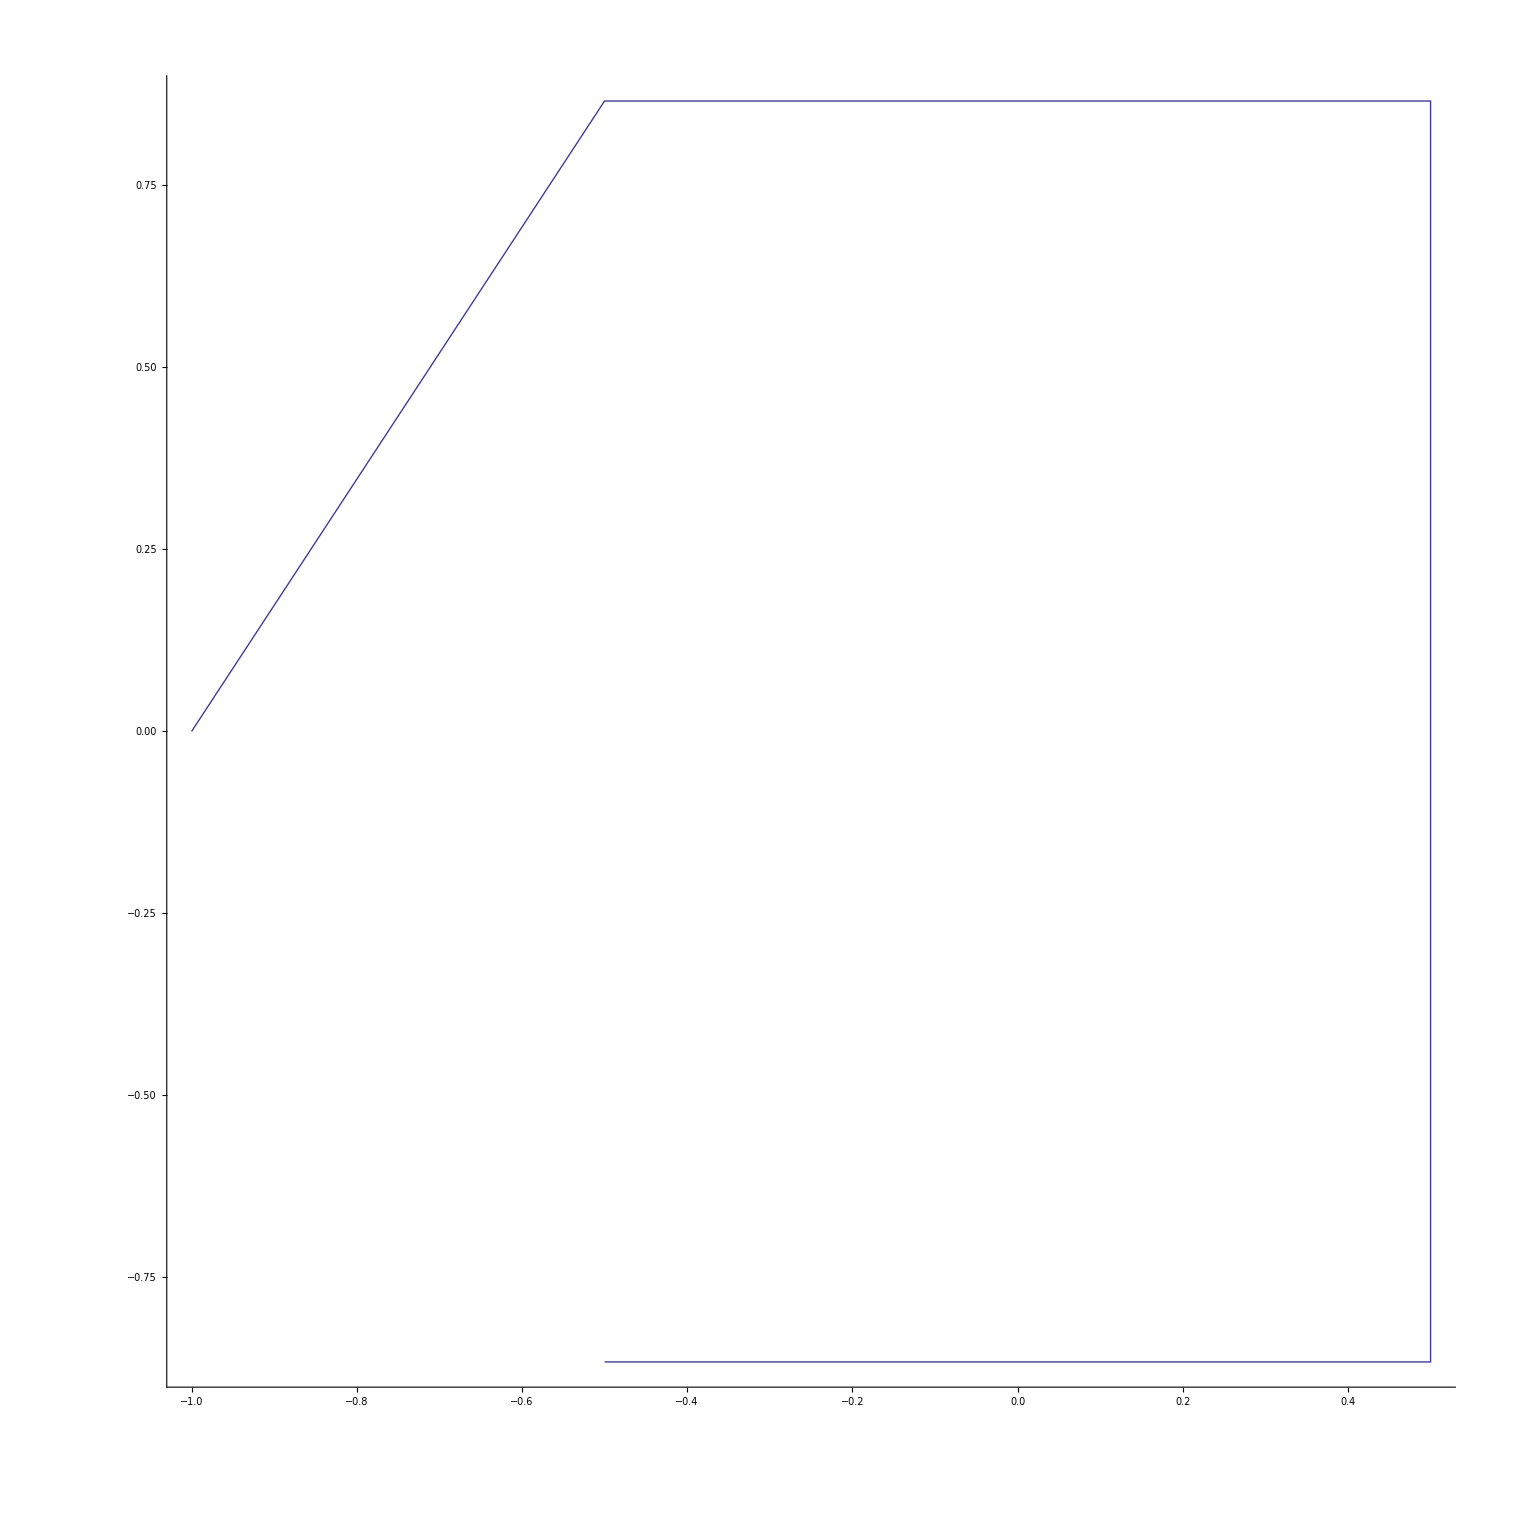

```mathematica
ListPlot[Map[{Re[#],Im[#]}&,Sort[Flatten[Map[Solutions,NSolve[x^5+x^4+x^3+x^2+x+1==0]]],Arg[#1]<Arg[#2]&]],AspectRatio->1,Joined->True]
```

```mathematica
Solve[Limit[x^Log[3,n]==2^n,n->Infinity],x]
```

Solve::eqf: Limit[x^Log[n]/Log[3] == 2^n, n → Solve`DirInf[1]] is not a well-formed equation.

Solve[Limit[x^(Log[n]/Log[3])==2^n,n→∞],x]

```mathematica
Solve[x^5+x^4+x^3+x^2+x+1==0]
```

{{x→-1},{x→-(-1)^(1/3)},{x→(-1)^(1/3)},{x→-(-1)^(2/3)},{x→(-1)^(2/3)}}

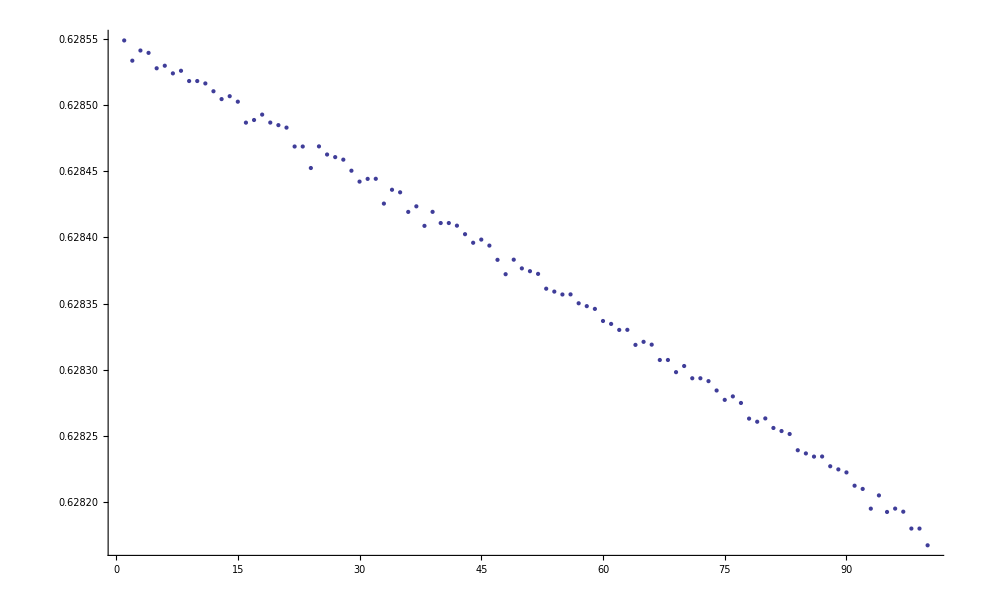

```mathematica
ListPlot[
Take[
Map[
N[Log[3,2]- #[[2]]/Exponent[First[Factor[#[[3]]]],x]]&,
Select[
Sort[ReadList["c:\\temp\\roots.txt",Expression],#1[[1]]>#2[[1]]&],
Length[FactorList[#[[3]]]]>2&]]
,
100
]
]
```

```mathematica
Monitor[
ListPlot3D[Flatten[Table[{i,j,Select[Solutions[Flatten[Solve[x^i == 2^j, x]]],Im[#]==0&][[1]]},{j,1,200},{i,IntegerPart[Floor[Log[3,2]*j]],IntegerPart[Ceiling[Log[3,2]*j]]}],1]],
{i,j}
]
```

Part::partw: Part 1 of {} does not exist.

-Graphics3D-

```mathematica
N[1054/389]
```

2.70951

```mathematica
Select[Solutions[Flatten[NSolve[1+x+x^2+x^6+x^8+x^10+x^13+x^15+x^17+x^20+x^21==2^1690]]],Im[#]==0&]
```

{1.6817×10^24}

```mathematica
Solve[3^a==2^b,{a,b}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a -> (b*Log[2])/Log[3]}}

```mathematica
N[Log[2]/Log[3]]
```

0.63093

```mathematica
N[1045 /1690]
```

0.618343

```mathematica
N[Log[3,2]]
```

0.63093

```mathematica
NSolve[1+x^2-x^3+x^4==2^8]
```

{{x→-3.71285},{x→0.25587-4.03519 ⅈ},{x→0.25587+4.03519 ⅈ},{x→4.20111}}

```mathematica
NSolve[(1+x) (1+x^2-x^3+x^4)==256]
```

{{x→-2.45949-1.76656 ⅈ},{x→-2.45949+1.76656 ⅈ},{x→0.959485-2.88945 ⅈ},{x→0.959485+2.88945 ⅈ},{x→3.}}

```mathematica
NSolve[(1+x+x^2+x^6+x^8+x^10+x^13+x^15+x^17+x^20+x^21) ==2^1690]
```

{{x→-1.66291×10^24-2.50644×10^23 ⅈ},{x→-1.66291×10^24+2.50644×10^23 ⅈ},{x→-1.51515×10^24-7.2966×10^23 ⅈ},{x→-1.51515×10^24+7.2966×10^23 ⅈ},{x→-1.23277×10^24-1.14384×10^24 ⅈ},{x→-1.23277×10^24+1.14384×10^24 ⅈ},{x→-8.40848×10^23-1.45639×10^24 ⅈ},{x→-8.40848×10^23+1.45639×10^24 ⅈ},{x→-3.74212×10^23-1.63953×10^24 ⅈ},{x→-3.74212×10^23+1.63953×10^24 ⅈ},{x→1.25673×10^23-1.67699×10^24 ⅈ},{x→1.25673×10^23+1.67699×10^24 ⅈ},{x→6.14392×10^23-1.56545×10^24 ⅈ},{x→6.14392×10^23+1.56545×10^24 ⅈ},{x→1.04852×10^24-1.3148×10^24 ⅈ},{x→1.04852×10^24+1.3148×10^24 ⅈ},{x→1.38948×10^24-9.47333×10^23 ⅈ},{x→1.38948×10^24+9.47333×10^23 ⅈ},{x→1.60698×10^24-4.95688×10^23 ⅈ},{x→1.60698×10^24+4.95688×10^23 ⅈ},{x→1.6817×10^24}}

```mathematica
Select[Solutions[Flatten[NSolve[x^1045 (1+x+x^2+x^6+x^8+x^10+x^13+x^15+x^17+x^20+x^21)==2^1690]]],Im[#]==0&]
```

{-3.00192,3.}

```mathematica
Select[Solutions[Flatten[NSolve[x^1045 ==2^1690]]],Im[#]==0&]
```

{3.06784}

```mathematica
Select[Solutions[Flatten[NSolve[(1+x+x^2+x^6+x^8+x^10+x^13+x^15+x^17+x^20+x^21) ==2^1690]]],Im[#]==0&]
```

{1.6817×10^24}

```mathematica
MatrixForm[Solutions[Flatten[NSolve[ (1+x)-2^8==0]]]*Transpose[Solutions[Flatten[NSolve[(1+x^2-x^3+x^4) -2^8==0]]]]]
```

Transpose::nmtx: The first two levels of the one-dimensional list {-3.712845667269717`, 0.2558703127070877`  - 4.035185606357978` ⅈ, 0.2558703127070877`  + 4.035185606357978` ⅈ, 4.201105041855541`} cannot be transposed.

(255. Transpose[{-3.71285,0.25587-4.03519 ⅈ,0.25587+4.03519 ⅈ,4.20111}])

```mathematica
Map[255*#&,{-3.712845667269717,0.2558703127070877-4.035185606357978 ⅈ,0.2558703127070877+4.035185606357978 ⅈ,4.201105041855541}]
```

{-946.776,65.2469-1028.97 ⅈ,65.2469+1028.97 ⅈ,1071.28}

```mathematica
Plot[(1+x+x^2+x^6+x^8+x^10+x^13+x^15+x^17+x^20+x^21)*x^1045-2^1690,{x,-3,3},PlotRange->All,GridLines->None,Axes->None]
```

-Graphics-